# Solving x-Space RGEs of Track Functions Numerically: The Moment Method

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/liirba/Desktop/draft_x-space

```mathematica
(* We use the RGEs of up to nmax-th moments of track functions. nmax≤28 due to the NLO evolution equations of the track function moments we have in the directory EvolutionEquations4Moments/ . *)
nmax:=28
```

## α_s(μ)

```mathematica
betafunction={β0-> (11 ca)/3-(4 tf nf)/3,
β1-> 34/3 ca^2-20/3 ca tf nf-4 cf tf nf,
β2-> (158/27 ca+44/9 cf) nf^2 tf^2+(-205/9 ca cf-1415/27 ca^2+2 cf^2) nf tf+2857/54 ca^3,β3->1093/729 nf^3+(50065/162+6472/81 Zeta[3]) nf^2+(-1078361/162-6508/27 Zeta[3]) nf+3564 Zeta[3]+149753/6}/.{nf->Nf,ca->CA,cf->CF,tf->TF};
```

```mathematica
colorfactor={Nf->5,CA->3,CF->4/3,TF->1/2};
```

```mathematica
alphas[mu_]:=Module[{ll},(4 Pi)/β0*(1/ll-β1/(β0^2 ll^2) Log[ll]+β1^2/(β0^4 ll^3) (Log[ll]^2-Log[ll]-1)+β2/(β0^3 ll^3)+β1^3/(β0^6 ll^4) (-Log[ll]^3+5/2 Log[ll]^2+2 Log[ll]-1/2)-3 (β1 β2)/(β0^5 ll^4) Log[ll]+β3/(2 β0^4 ll^4))/.ll->Log[mu^2/(213/1000)^2]/.betafunction/.colorfactor];
```

```mathematica
alphas[10]//N[#,200]&
```

0.17927784197950593970782556625434294730631124811398790077047796986886243234213856259707746848581962196582961984434474711014445302800420286202617393181767327817548000635709792377612875464520906856386741

## RGEs for T_i(n) (i=q,g)

### RHS of the order-a_s evolution equations of track function moments, with generic n

```mathematica
(*quark*)
DT[0,q,n_]:=3 CF T[q,n]+CF(  (4/n-(2 (3+n))/((1+n)(2+n)))T[g,n]+(-4 HarmonicNumber[n]-(2 (3+2 n))/((1+n)(2+n)))T[q,n]+Sum[T[q,k]T[g,n-k] Binomial[n,k]((4 Gamma[1+k] Gamma[-k+n])/Gamma[1+n]-(2 (3+k+n) Gamma[1+k] Gamma[1-k+n])/Gamma[3+n]),{k,1,n-1}]  )//Collect[#,{T[_,_],Nf,TF,CA,CF},Expand]&;
```

```mathematica
(*gluon*)
DT[0,g,n_]:=((11 CA)/3-(4 Nf TF)/3) T[g,n]+  (-(2 CA (-6+n^2 (3+n)))/(n (1+n) (2+n) (3+n))-2 CA HarmonicNumber[n]+2 CA (-2/(1+n)+1/(2+n)-1/(3+n))-2 CA (EulerGamma+PolyGamma[0,n]))T[g,n]+Sum[T[g,k]T[g,n-k] Binomial[n,k](2 CA Gamma[k] (1/Gamma[n]+(k (k-n) (11+k^2-k n+n (9+2 n)))/Gamma[4+n]) Gamma[-k+n]),{k,1,n-1}] +sumq Sum[T[q,k]T[qbar,n-k] Binomial[n,k](1/Gamma[4+n] 2 (4+2 k^2-2 k n+n (3+n)) TF Gamma[1+k] Gamma[1-k+n]),{k,0,n}] /.T[p_,0]->1 //Collect[#,{sumq,T[_,_],Nf,TF,CA,CF},Expand]&;
```

### RHS of the order-a_s^2 evolution equations for the first nmax moments

```mathematica
(*gluon*)
Table[DT[1,g,iii]=(<<("EvolutionEquations4Moments/kernels_gluon/gluon_n"<>ToString[iii]<>"_ana.m"))/.{tt->T,fq->sumq,fQ->sumQ},{iii,1,nmax}];
```

```mathematica
(*quark*)
Table[DT[1,q,iii]=(<<("EvolutionEquations4Moments/kernels_quark/quark_n"<>ToString[iii]<>"_ana.m"))/.{tt->T,fq->sumq,fQ->sumQ},{iii,1,nmax}];
```

## Processing...

```mathematica
(*For simplicity, here we assume all (anti-)quark flavors have the same track function.*)
```

### order-a_s

```mathematica
kklist[0,g]=Table[DT[0,g,ii]/.{sumQ->Nf-1,sumq->Nf,qbar->q,Q->q,Qbar->q}/.colorfactor//Expand,{ii,1,nmax}];
```

```mathematica
kklist[0,q]=Table[DT[0,q,ii]/.{sumQ->Nf-1,sumq->Nf,qbar->q,Q->q,Qbar->q}/.colorfactor//Expand,{ii,1,nmax}];
```

### order-a_s^2

```mathematica
kklist[1,g]=Table[DT[1,g,ii]/.{sumQ->Nf-1,sumq->Nf,qbar->q,Q->q,Qbar->q}/.colorfactor//Expand,{ii,1,nmax}];
```

```mathematica
kklist[1,q]=Table[DT[1,q,ii]/.{sumQ->Nf-1,sumq->Nf,qbar->q,Q->q,Qbar->q}/.colorfactor//Expand,{ii,1,nmax}];
```

## Evolution

### up to order- a_s

```mathematica
evoLO::usage="evoLO[initialT, initialmu, finalmu, steps, digitprecision] is for the LO evolution, requiring as the first argument the initial track function moments (a list with as first entry an array of gluon and as second entry an array of quark track function moments), as the second and third arguments the initial and final scales, as the fourth argument the number of steps, and as the last argument the working precision. The Runge–Kutta fourth-order method is applied. ";
```

```mathematica
evoLO[initialT_,initmu_,finalmu_,steps_,digitprecision_]:=Module[{lmu=Log[initmu],stepsize=(Log[finalmu]-Log[initmu])/steps,asvalue,ii,ttnew,grad},
(* the initial condition for the moments *)
Table[tt[g,ii]=initialT⟦1,ii⟧;tt[q,ii]=initialT⟦2,ii⟧,{ii,1,nmax}];
(*evolving...*)
Monitor[Do[
(*1*)
asvalue=alphas[initmu*E^((rr-1)stepsize)]/(4 Pi)//N[#,digitprecision]&;
grad[g,1]=2*(asvalue*kklist[0,g]/.T[p_,n_]:>tt[p,n])//N[#,digitprecision]&;
grad[q,1]=2*(asvalue*kklist[0,q]/.T[p_,n_]:>tt[p,n])//N[#,digitprecision]&;
(*2*)
asvalue=alphas[initmu*E^((rr-1/2)stepsize)]/(4 Pi)//N[#,digitprecision]&;
grad[g,2]=2*(asvalue*kklist[0,g]/.T[p_,n_]:>(tt[p,n]+stepsize/2*grad[p,1]⟦n⟧) )//N[#,digitprecision]&;
grad[q,2]=2*(asvalue*kklist[0,q]/.T[p_,n_]:>(tt[p,n]+stepsize/2*grad[p,1]⟦n⟧) )//N[#,digitprecision]&;
(*3*)
grad[g,3]=2*(asvalue*kklist[0,g]/.T[p_,n_]:>(tt[p,n]+stepsize/2*grad[p,2]⟦n⟧) )//N[#,digitprecision]&;
grad[q,3]=2*(asvalue*kklist[0,q]/.T[p_,n_]:>(tt[p,n]+stepsize/2*grad[p,2]⟦n⟧) )//N[#,digitprecision]&;
(*4*)
asvalue=alphas[initmu*E^(rr*stepsize)]/(4 Pi)//N[#,digitprecision]&;
grad[g,4]=2*(asvalue*kklist[0,g]/.T[p_,n_]:>(tt[p,n]+stepsize*grad[p,3]⟦n⟧) )//N[#,digitprecision]&;
grad[q,4]=2*(asvalue*kklist[0,q]/.T[p_,n_]:>(tt[p,n]+stepsize*grad[p,3]⟦n⟧) )//N[#,digitprecision]&;
(*final*)
Table[tt[g,ii]=tt[g,ii]+1/6*stepsize*(grad[g,1]⟦ii⟧+2 grad[g,2]⟦ii⟧+2 grad[g,3]⟦ii⟧+grad[g,4]⟦ii⟧)//N[#,digitprecision]&;
tt[q,ii]=tt[q,ii]+1/6*stepsize*(grad[q,1]⟦ii⟧+2 grad[q,2]⟦ii⟧+2 grad[q,3]⟦ii⟧+grad[q,4]⟦ii⟧)//N[#,digitprecision]&,{ii,1,nmax}]
,{rr,1,steps}],rr];
{Table[tt[g,ii],{ii,1,nmax}],Table[tt[q,ii],{ii,1,nmax}]}
]
```

### up to order- a_s^2

```mathematica
evoNLO::usage="evoNLO[initialT, initialmu, finalmu, steps, digitprecision] is for the evolution up to NLO, requiring as the first argument the initial track function moments (a list with as first entry an array of gluon and as second entry an array of quark track function moments), as the second and third arguments the initial and final scales, as the fourth argument the number of steps, and as the last argument the working precision. The Runge–Kutta fourth-order method is applied. ";
```

```mathematica
evoNLO[initialT_,initmu_,finalmu_,steps_,digitprecision_]:=Module[{lmu=Log[initmu],stepsize=(Log[finalmu]-Log[initmu])/steps,asvalue,ii,ttnew,grad},
(* the initial condition for the moments *)
Table[tt[g,ii]=initialT⟦1,ii⟧;tt[q,ii]=initialT⟦2,ii⟧,{ii,1,nmax}];
(*evolving...*)
Monitor[Do[
(*1*)
asvalue=alphas[initmu*E^((rr-1)stepsize)]/(4 Pi)//N[#,digitprecision]&;
grad[g,1]=2*(asvalue*kklist[0,g]+asvalue^2*kklist[1,g]/.T[p_,n_]:>tt[p,n])//Expand;
grad[q,1]=2*(asvalue*kklist[0,q]+asvalue^2*kklist[1,q]/.T[p_,n_]:>tt[p,n])//Expand;
(*2*)
asvalue=alphas[initmu*E^((rr-1/2)stepsize)]/(4 Pi)//N[#,digitprecision]&;
grad[g,2]=2*(asvalue*kklist[0,g]+asvalue^2*kklist[1,g]/.T[p_,n_]:>(tt[p,n]+stepsize/2*grad[p,1]⟦n⟧) )//Expand;
grad[q,2]=2*(asvalue*kklist[0,q]+asvalue^2*kklist[1,q]/.T[p_,n_]:>(tt[p,n]+stepsize/2*grad[p,1]⟦n⟧) )//Expand;
(*3*)
grad[g,3]=2*(asvalue*kklist[0,g]+asvalue^2*kklist[1,g]/.T[p_,n_]:>(tt[p,n]+stepsize/2*grad[p,2]⟦n⟧) )//Expand;
grad[q,3]=2*(asvalue*kklist[0,q]+asvalue^2*kklist[1,q]/.T[p_,n_]:>(tt[p,n]+stepsize/2*grad[p,2]⟦n⟧) )//Expand;
(*4*)
asvalue=alphas[initmu*E^(rr*stepsize)]/(4 Pi)//N[#,digitprecision]&;
grad[g,4]=2*(asvalue*kklist[0,g]+asvalue^2*kklist[1,g]/.T[p_,n_]:>(tt[p,n]+stepsize*grad[p,3]⟦n⟧) )//Expand;
grad[q,4]=2*(asvalue*kklist[0,q]+asvalue^2*kklist[1,q]/.T[p_,n_]:>(tt[p,n]+stepsize*grad[p,3]⟦n⟧) )//Expand;
(*final*)
Table[tt[g,ii]=tt[g,ii]+1/6*stepsize*(grad[g,1]⟦ii⟧+2 grad[g,2]⟦ii⟧+2 grad[g,3]⟦ii⟧+grad[g,4]⟦ii⟧)//Expand;
tt[q,ii]=tt[q,ii]+1/6*stepsize*(grad[q,1]⟦ii⟧+2 grad[q,2]⟦ii⟧+2 grad[q,3]⟦ii⟧+grad[q,4]⟦ii⟧)//Expand,{ii,1,nmax}]
,{rr,1,steps}],rr];
{Table[tt[g,ii],{ii,1,nmax}],Table[tt[q,ii],{ii,1,nmax}]}
]
```

# Examples

## Initial condition: Toy model

### Initial Conditions: μ_0=10 GeV, toy model

#### To get the initial moments

```mathematica
μ0=10;
```

```mathematica
trackfunction["LO","g",μ0]=12 x^2(1-x);
```

```mathematica
trackfunction["LO","q",μ0]=12 x^2(1-x);
```

```mathematica
temp1=Table[Integrate[trackfunction["LO","g",μ0]*x^ii,{x,0,1}],{ii,1,nmax}]
```

{3/5,2/5,2/7,3/14,1/6,2/15,6/55,1/11,1/13,6/91,2/35,1/20,3/68,2/51,2/57,3/95,1/35,2/77,6/253,1/46,1/50,6/325,2/117,1/63,3/203,2/145,2/155,3/248}

```mathematica
temp2=Table[Integrate[trackfunction["LO","q",μ0]*x^ii,{x,0,1}],{ii,1,nmax}]
```

{3/5,2/5,2/7,3/14,1/6,2/15,6/55,1/11,1/13,6/91,2/35,1/20,3/68,2/51,2/57,3/95,1/35,2/77,6/253,1/46,1/50,6/325,2/117,1/63,3/203,2/145,2/155,3/248}

```mathematica
initialT={(*gluon*)temp1,(*quark*)temp2};
```

```mathematica
Clear[temp1,tempg,tempq,temp2]
```

#### Check the initial condition

```mathematica
ll:=28
basischeck=Table[{Sum[(ll+1)^2/(k+m+1)If[m==0,1,Product[1-(ll+1)^2/j^2,{j,1,m}]]If[k==0,1,Product[1-(ll+1)^2/j^2,{j,1,k}]] x^k,{k,0,ll}]},{m,0,ll}];
```

```mathematica
(* check *)
Integrate[basischeck.{Table[x^k,{k,0,ll}]},{x,0,1}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 1)

```mathematica
tempplotg=Flatten[basischeck].Join[{1},Table[initialT⟦1,ii⟧,{ii,1,ll}]  ]//Expand
```

12 x^2-12 x^3

```mathematica
tempplotq=Flatten[basischeck].Join[{1},Table[initialT⟦2,ii⟧,{ii,1,ll}] ]//Expand
```

12 x^2-12 x^3

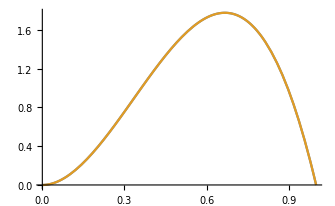

```mathematica
Plot[{tempplotg,tempplotq},{x,0,1}]
```

### Polynomial basis

```mathematica
(* mnum is the number of the moments that we use to restore T(x)'s, including the zeroth moment *)
(* the degree of the polynomial is mnum-1 *)
```

```mathematica
(* the polynomial basis we choose*)
basis[mnum_]:=Table[{Sum[mnum^2/(i+j-1)If[i>1,Product[1-mnum^2/(k-1)^2,{k,2,i}],1]If[j>1,Product[1-mnum^2/(k-1)^2,{k,2,j}],1] x^(j-1),{j,1,mnum}]},{i,1,mnum}];
```

### Evolving moments and restoring T(x) from the moments: LO

```mathematica
?evoLO
```

#### μ=100 GeV

```mathematica
(* Specify the final scale mu1: E.g., if Subscript[μ, 1]=91.2 GeV, then write it as 912/10 in order to ensure the working precision you set can be definitely achieved. *)
```

```mathematica
mu1=100;
```

```mathematica
(* evolving... *)
(* Fewer steps such as 100 and 1000 steps are okay. *)
```

```mathematica
TmulistLO[mu1]=evoLO[initialT,10,100,30000,200]
```

{{0.6,0.3848427392154187325187904988851559704810715024414719256880511369436515088331788566677373777542172199796603716737833143725803539697249295972809930270891039701172308519653753005320747872939464597287688,0.2596029554599886918256424989781099396421946246912501011490308480981687546592663154992285447998304674529669836890292624836878512926311289286984835599594837134646556849351576723000462719315595609009396,0.1822897724375383930772151732549654829686896387991020406959667183602126367548439162569393813353294053562304554578488379044240624707011937553244063259208091465713764906787327075395820052246302156197605,0.132297600568883579145685110966028415857906610750418175146336286286665747299164597468641825205689304454852555513934507986431593614934924422565564613258564419489218237087190606037833838217429188310141,0.0987197582353140130835128197523016128704475327071438134170337582767625807798988394136044520920620896560484520267734297115948399702356460184664778382740530437817479134958872113805913948404078527342088,0.0754342319466443871223422964992203742195030822261388979395165878165098263107388203083862702245848927397630227127392275263863484514161677630252610603496665237144331710074744727152719635709807506250468,0.058837611981794139162875852833960298418722461394493814326833545247024554488203192747817350506021735077378467893125376383476002776967236908685334741935221324264691020770007273096267545357405492963795,0.0467233161156128804633477777786202102247181270908807826358346267774174798295170169773368154362779903909469786796210192564125367930750955118490923508237024641479375640809938253527823323275028375236983,0.0376937525806156926936777972712526492078282409324910140538553587614648661288583959683945503795224782410651817579696458109304564783263394457260967589646312480066325739903999897674885093943941380832352,0.0308374337710796896679175507074511623723932670061160151516532062830857405324892232700798908159484011076861906467567842924437476200355990487123180182049756938537086054863323875802886679158817153397532,0.0255444099084356276151936391066261091932068159604174609003538935108308180959519910258104484801574293169011455390040916298637882239837705908919978725572534247612906201180079128991072214023534159895647,0.0213970779430410405885207154363043728150488861925579444658435577938698266900354505654787405424999217830821667736080373775420427976667239066101961619155611813219852753873103445014676349277059065511141,0.0181036092413496525750261847935259708593747186880396538385259310155334217562275846958265054413250038042636695526813093453315896723455072647995196207323568701910659576929561891227264557046826373775122,0.0154562645094989013842160614154041555509360499791363760878359370415419444072059142531352386557937846556261176567735927726370140422698397962238023002975586786886855541717444046010056662243928822798674,0.0133046620134184650731213083580275011936644475324610924836599123104760597617764912866435313874801524759425147462847600065983004642490317288693603763963372109926113459885266229841521553855615435145892,0.0115382622116932090993748159117641341468123589849251217092659418087207785676732900813446764676739106023621018179409358164861075222516633302235978576666187381855271253235009501857345853056596751563825,0.0100746647987669568383539463639734018067881966354659369885565857717550456897095491496315922376300556484994610790949085152307648109798126095194843943043339249092281329390924060285101606640092389527422,0.00885164855466051806008054652376470889638435617510933010015769353041571088038579031028656761179893238644240969327849102557383983936943842146916221667765962540747589026406837695144388314030723369304836,0.00782166758818014922578933107283253247722392563274434666274310733450996566113931305132992177709797608293278894527722419481509876114955159430734363051356989860515969336325264618028646804831217048677654,0.00694798808857139604069976136950411499292750121480892079515971071500619213622711848255581604892691979037574795447516295652610050008482197124302249407678048677882633274476064645400118288750723376004353,0.00620193846568532087360049461488609742021336068625217271067502413686383117841217029583958100306674603544519895475821598776883192521761579427567791986970127259964647037976186361402308277991464697364458,0.00556092646663309576191472435867538114810570661998083282342637021193141874822536873040531857335838653040572699758219036147796200165680563220340386966973825505509102565123862317357551971241799309943993,0.00500699199429449382301667057813270971859605648372967970502515440338647493091025041662304015833917784494476879035151382963585933318109727042782713991197132001919448092611717738974089826670676844012555,0.00452573894280063193547477804006448688124867124890715712542605031867739529377086389060640972706994286264350182908700522725591910121523247861504862243463121189351133931461953757921770999644328548472518,0.0041055384390739923851136296789968735579626826434656624332520336010555798623406848160612016704022837808105220003554628022141167456804180129875646860067556094406761912567928449174983505996509749938018,0.00373692863432955396085259829462505895548851873629354238801682831706505563711349744886257163970161027396739710442802324574920686861463014537762144640067338750916902458173332839106454851779154043687906,0.00341215834807210337588756131328060956916416964416455869921188176629170801822032963321001655125553875104081174934217469430459690724095907420528449998110032772714637297965187911895969085057057963195188},{0.6,0.3920942123578466416892100299579296662671019855213044038931576826457500809969260582160416011110875649633987363845186073033126463100040989412278090290610055175012196486588290304363641757625140905069339,0.272117290489503979187518975888582337002495728532773394995397966619665490337691019184221141618306030508060830418994084481678769375247937377771045629087781062415555344240985769945403576007393631804384,0.1975897598711333294300502944836203844804380057219827392751839636311687481893099034308151983571952270530120400163588821988830248930495090486678569717188455122169581749840188671264019093256958197842416,0.1486536922089539731614459329881740823738975289528481773346352689351528184737340210149923619244997458823273686537871771221666832727910753254249591676326004607859340282136381192046106729533103136412262,0.1150866407080738305325753635584702246238170383895260696276985734594290555372566030420896150487377483323804074348932628182628718008155421425634468590712784976922118595097576847818836218849425425549433,0.09123004471785069466295734167495454556725978675327214660171474264657781843152404118353789863768806580407049672791563241008180979187156350330026843392046601045489321126602589086556382096812299518247275,0.07376733184756561017563326441594950271910049058737263061837855495783415662489239551585366291440546831912878531986505712087959019893382999136845943035639112337171988716880809614770364443595358835843089,0.06066204100660865721205425900101045131917276786770560506939278389855124595234010657007122116844706264138318298339689489192792352384063048775597707411535221458386273193578631878509089172962897362097125,0.05061428458559200997504243278158879983143349395930070485346129392626740883997972106256544457982826973392409294421720834360308993256758777379962134331378950971796274795314334585233900691382437713100388,0.04276654197891166400176993758377590876472768016158961054670016686567754189227940708714626748048710422828353249315874318290259241085423772339488631582959987254819449914090872529347770336031565472988151,0.03653681419227618844248033735886153956915459445047280670110697241562541438294120834552708079593963245829047168429405532386344201180121971407141443986872165756932398925595890886927273917038982078667041,0.03152018167744931322386928554842721454971515466837180770185241121325832717759246524133735408661453575039242909585954150143413066644050442241980929869460128268048189225356940745131029998664198938286463,0.02742870090237568175860893128635439636543985676688963103418461341435945187285292128877007038003963801367416073419318768496567803151133465306897365047826924518437682455633826983344370992603824834933999,0.02405359507491768975703967062471996537235607741121334325019086130629898050766838573893036472301193349086594108442127186956904913919490526290285010035645134042772472845699956615726910661848284594971227,0.0212408332049883680592513733431972830907703998928263724771497919924599982009183405031544457204670257467300710739648015203215973966646400336424373230934780574165195389436245476422758947581018651325146,0.01887498128176213138293611525683542855699509543491083739362892919289124251398621610950820803375353962596093488448694262533003341101367087258305289557166670710735847920795230105681115619749616006843476,0.01686829571506285980473090609956588363896903677764561361987954069346831336431969298219868982446635690245385791519275538990059994604265106755991755404295593253203400623907397382024255876993850458891706,0.01515321546984371615967565496471443076900342133593046151234271740735141118886603985521672621898102005424015406688721389981427625316415615469432164693388617221911883218576904705490243624951724669509332,0.01367710349389847138592706271654403565356902057619040133286489173496798846052735770788970689177532503637329184850729040990353836731925535574665037412141323549365052909115722481484852080782459890301739,0.01239850487649211052629912077387727839327328621747729742895426384790961664793163609475017968356053179948736664544929588320606509128440187663915148393365448326566589580620429138875805280858558714889815,0.01128444539915610099119093146142078319930201665067711475991910846207765840059924493184887889539310556087386706147829432300552488249146408172570311117477768754570690403366266136612362468185610012215676,0.01030845502262475378133081080687551800034674066340054784735058611600169420045044123791997388316012491528962109323188082012291738678757586226168367215183598347942379580635923359747951932060559659164835,0.009449103856705111932212749101155174838338269796409168664686687750803411721067478995132729068070191918611721858965722388260764695261423008289167506986938195976318016002630054156158847446777663390507512,0.008688905295233869988566889674885729846313670844267141508306182718345325056834613951240756025061683738818233554949565314402179929985537793224630563026868490130148151117959194984016365952452715440447739,0.008013485483292116385462400347008133472098700216937611315260355827123274963669837078321308668857330671558168755917080668437646754550516476595749021505826397684270650218375262295147762594411925537916589,0.007410948213693638471829008455641916644384563951884512229722619149002658316405095281658482611615961117663654962739724273658191302044493136418330334342137655074569589928920600597067678508949300180287983,0.00687138477423424588267151884033188378619571269882226775532893850655129421389570147981148650655950277070162166820097633446578737384084015980281014439095651972519313188320631278226649956646980050234853}}

```mathematica
(* using 15 moments *)
```

```mathematica
mnum:=15
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.0012575517694750522215872570883161210368836511461718904054720311558583034805976934023950732927295865440470081140600475867143844455794486006207343799063810532995565363673366660158884171683-0.2975857956789784254420099582530328000459089482019832355957046852248964010851973978115600114207945743858047899035340244663309038211200883880585582540347822252782410434065125289684521417 x+17.582552238885663591809534690462981623597610608053982771242681105169476443066138007801858050722076427444223802902032905610077172732786538426531440165472732744597779420414109931751949267 x^2-406.51992453497041794614825548117606233962472028074381382270489754832172137361770295747274367975180445095279292263403859566901263129543698251881809756589073502260399576474692549920920298 x^3+5783.7772825250461511022830485581018095791282950899754979051397206822059548909440578661455669935776151815109919915014345819449702359973375346309594946972847583550568947766925333863798551 x^4-48370.089799099081556065495570714617184834946123244329141161004171352834214340463180088303511438636709062174035558239452805433568538308620962981229240344061669730198846584817506540761546 x^5+263493.30848315351572279568746287287409164971868331283207980043022964751623027641183407874278467399094272410225059240049556643144648298632417417323752858513378721628282395205742732490873 x^6-973927.79381736184571127944929518872016042240208361327778713490698318003785321889070436714535344206260888967098786335275781085073793869467737090735092716663180785932256829176613271985048 x^7+2.49840046095348048849893685042359762453139980446761904251120535894954767343229601621232999138619091600395889792888183099706586828367484441827907167505067097563662513776127477764440898136×10^6 x^8-4.48216037695749419921147479756170780662637477615767550149824936987404889471589752939754843064434001947448095291220130700415607837125108807250925046697529236292801006574571664391481943955×10^6 x^9+5.58682355809854903260311135903570701852554354011828615940264696315903559210938864903760492435851081804945010069727447138053221626426901769035466615675034538604912230200737189855962703465×10^6 x^10-4.72918532979662562209628409725131331098487725709182300366647198918076438782243729451914955377836946800382277761129383743850800039726773392345445843813428905952672250438382276868796237668×10^6 x^11+2.58921595020156995311858639235772486887649171745283573179996436081023273560537120957759154444179058686470612646837818197134338142439883684866929840084280095399788098615692795912580571258×10^6 x^12-826464.761085155843215777042574803763394347994300931143667519087316553448720564473239937089375830364316633594691284907953733244471561649168760235180766725803645950299883404894003334776895 x^13+116780.528936617258688925763417976236250807653375942276124827906146789286615181777802752790865390363211173296585637322279688741162001513780438624915980487778557770484947307141969819727241 x^14

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.00052509989283065639567390124619741181919060851988755697261830487016403422113115129236864554183837372809652577508861840518818033414643915473736781334280450170155790480304905873759621038395-0.12695982076923102511573240486621154865859045313823036735976580684100177356998331127072764708983087668684102045309393183273630783681987231347338196631401670137599066497890846307277384561 x+10.1132122799036095602078846798434936171967148278424328943124010099450952914657650552457768337994396820815946252566773440269218881829224001184126982207699704804505331888400957271983428079 x^2-123.13458170772833311698426659773693765831964605096256232891934538000887500864406409021644504659687948182557483708045648097852027467718296820535419542990607446063893449907343663361795687 x^3+1882.8704693340103956178730965076803467075997539344636574224283035412536987610370036905485881374371325991938425467395780117614970049341700302627157014490537238723209449818421753746646905 x^4-16045.942798155196251015562556199786745341949873650405415086949597324519860956405553404580308594686435795760332408751296102293738462302869398960176735362563455934616070032424029667530588 x^5+87636.7049621726772285246854203561064271012274978148307626012479825804946298590317959977379208979513611809675846472663014598585681874150825398939930894610496946919804297453146397558495619 x^6-324025.030442421745120952389874856169575217547510996076418039365722379972439584512995898407198073648438647908749379929005223800611391409869861124022975095083830383262855090689437608584549 x^7+832902.99754922271361083232936370703723898909125087585087865125729445870304224637091661547430106800172640727216653045758678299551199118796226372927395595503492936089952979058300373944264 x^8-1.50344766748905879701661200598164111108552366485958789246917696778879079422989382718618571274663017805475539009021573426433528975242803072629397096249888644590945626488287616923288287564×10^6 x^9+1.89578478386405308992146036660435760148792868716653693674061868651647943502434910824184313621493841631953422187987105264904575358706728590808963931888818527579886751701089446264234333903×10^6 x^10-1.63310794333069324201306636336595355735682350204907678457893486498019603686943286736976879246612474986790028876479846125066873210271702332831599395236612547094961988446609578434030864824×10^6 x^11+915407.314561047533145440113391386662909318509555160454700655528612098393359251713973754972872019863990086663472323396257642506600093161869651810072642604788797124026071750488372325503136 x^12-300904.736521274491779679602709397578984684020649269670586432394044568350329925267607434010033671614529107977963057031922111459977524711429627910734655471545467894082172750117357202074305 x^13+44029.7931920015986575247492156842942937402705467524141144755642213008897677866234353527562960429705512143511582618438542060369728980637094980377371038245766101191531286062052228012548713 x^14

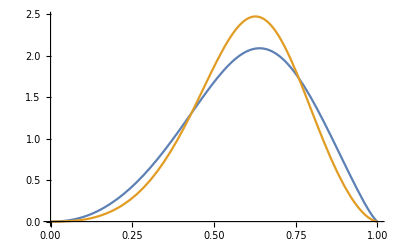

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1}]
```

```mathematica
(* 23 moments *)
```

```mathematica
mnum:=23
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.0000173511412248297380326867254756960978022922512978373263616130502053356805998764666170305662985326758541509536289574383489766769288306790009162668445695766283079432824171841628192-0.00945189304857113658814458040832220911662933979050927922697369430591480553891972953792726718353331929115386863252082848907750835266434092604878824486226421809995866258209705867883 x+1.42018602277625624578971813609317108257861118181454076020001354763049202296155717092499573431820146886526544099783649531609675102095720744834476446172178968402570151589914748982 x^2-33.1890518363088701542053557996571635117682680125367533308732741588191119755570998393982402918857540674603355056465944360068771078594673936525897788587344136000356200290206840293 x^3+1778.69104120717438339651304548470988183007999795027769936074135267500504944327868313479035195358690109053562600018487636524476457760949518372829920338401098637675985822955908548 x^4-37510.6160859544587713112509241571346583756292242081025988561625025184258684519645955743186017802884474248351475791727429891721667031064040968511038307655162255872766218041303353 x^5+519592.537766910840494752304617702082107432252454983752341248315933881369253758477829878424030425036031991980023355241367948908521291905870079795663482100944786956179354369694907 x^6-5.08510013632585007373970113788515772490418971019810616650336835726183512552829287497903086520091184582146285922724946080157511472902672527581399474759393628574578767619893445347×10^6 x^7+3.6693836025220736355440656815877580017916974287487740284854649632932867812788188911564677491162754635894826948145790751040142078266571553322332176989130648378479381433397117107×10^7 x^8-2.00822395407404344924378029552886762171575957375668669114620994845385299486888941133694485731666053360617034268749093077500588546306508714478795570217513306938149035248829142984×10^8 x^9+8.50283350566809864387614667796818303857872527576065951450785945280945472921542972313630978864010803694691645795513095872395760880705045241664039189039724583757897444322286897865×10^8 x^10-2.82415460253946957452438615412036119931794865088447582189678719149961271982547371966764095243664669570103104218081222626138586016058583389359840917713347575893223930085949781309×10^9 x^11+7.42704419289148350930411434724689171778921591880996540928975156446420194323250226986650165131798793838171825810842445773013613023040470615495221340600587196621057629479463889685×10^9 x^12-1.55471878752712214105470729177544982888342402424883272222260174852054344431288206758880841783147247943884241194431968069975528857370721737038026403664007829790775052750604070179×10^10 x^13+2.59461196725985063596784111437017374831863290633224515342173763878880490812420276227491393516823502164554149356311627674751045237897753320708259152171229696149853885154649755026×10^10 x^14-3.44387599741717602129814758778284121407465275094728923456638031779069359807228586725338673156206617834883076486468602725735210852973933959221944751027715651810310215050788475763×10^10 x^15+3.61042910459224556896254685294795422493422840200923616928843830197855576304496475805775832098323234947872347351459328549930348302414469515772191679738691504345379737624204594925×10^10 x^16-2.95133748079805619243651706602050878578385616772333525178221443746061884957073910806104707471343961629731912316471960695297462474449897143697200949524066310645308252288507425855×10^10 x^17+1.84148362103953443152874937550465359535556219246228673569981733913108576949911131067946581610612705619681998359673843064645497610141608914196849814011757579294077400463119975979×10^10 x^18-8.47038524411955092590349707072667950629344134391272931065527212947381655971119399383549879275208011711962097892114205773228278031278919665289667456069131482857471524242621411539×10^9 x^19+2.70713327994018633646428259713305523457703310554681518693571596246144095596933239199254710819128397203751031784199193422623975643038067304078377669180839271455230332972868047574×10^9 x^20-5.36869372547737478221728124349951319765239856203653907933547008412628714936567556521766747364651655437321880990934695084310973856044365239295318446033699176748245475021355053619×10^8 x^21+4.97539549993695621338727917787242905505638839450232146047196443642195070122571934266203943898565633391914937288196740082500463426721488504701792731714139259827780779133031200368×10^7 x^22

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.00007389421784939723215546323298002876992028061713877488046362817351113882492610627362845997964740280506337647245531064148737030404860595734095347815434577338277175876408921381481626-0.041325475477768041741108123688706278090900265926393222569173478229726588143628758209279693178278376007189429983060010231723949500838583129580064795759875260132801824087880989585571 x+7.743527155608931935582020931225075328817638878300624378617940469330078817767489057976545151308039859669537702825941543935565929285405729783888439268850487062209429761837792663295 x^2-213.9357317946759459155696113423463868964249858546902037606748472528126745181282972115038172424736771563916372633968426301567471879542732857088198842305409181011935780975499876068 x^3+8048.8154014783088792133803315204916512259254097767013071132476456320760745377417643089717840212978368030036186750670944339400196311100590105661909219500600468919510803530095155544 x^4-169827.21178593061416755238546502813725663856908480962867161521309232213350759421103107510263281705571677221906996124115758821665462394346967534505231820510793279922531720491205738 x^5+2.3788759090156934334995900509597228027946289393393815938546484079682421775262825977040171721087777092948859681343637604247658073692693679466395648320212658598223571725674554779143×10^6 x^6-2.3646017304577267878591036383261509065492953519307558132568822028334008946290634459831623974103095908991020786583802396367036448285435954609723925162802580396673229304408820720345×10^7 x^7+1.7368681358035112515552777549389894516751199813533108848595433428886044438609228220116974342238075698317874429217830526964499051665802790230919861377804527722554090064453077193733×10^8 x^8-9.6923128985860879839606033379247268542695710240176015553358381166203231119512470906893993412104147539103842211511723888238613442860611660992086863050303532804359447177139456677408×10^8 x^9+4.1901720079260790943138743678304129362920920282057122424637322365120667964997814323229650695678098209562754490147086894725495991271923422956646082075882062018007061007808710551858×10^9 x^10-1.4227245971746064661349054562454789298952263696320240206312256891930326455300977887456259743443491465199365126606084126924531834199584361818014332836546258781849447057892193975437×10^10 x^11+3.8283459694243989372096977954932959623695640684411696822442428823883748931263749900758086843989288250775132928308824165778925836173296980634539247215508425853078254795447016679566×10^10 x^12-8.2047929312993690207268636315972142047173440550905452994328342636259435263634015678928379421474055750374929851027638706211457913826360175145852534595483982621623433133682473383835×10^10 x^13+1.4021451116107464476811730807590692949748216540616062739135701008903672189449597109923224281221164294892160448267100435765737078937549415113411152404832114157382161959276335805422×10^11 x^14-1.9052506354241992595530617328739174489362976530943439494381370891084297457683688042991259160148751861406576113869635015854868957050115302287354947691222652653383201826786375847945×10^11 x^15+2.0431466640803322377760826458146777578876148655264580732788078597674200551625032131538261080662439480096968609447025020686780298025808335362617042345216498975556233633664913454731×10^11 x^16-1.7061380802130510890940160728680442717478070594079140153208021961306865393453873594471781210056078604381058805240303069867605497805921693830312199481567686336855681418375509587035×10^11 x^17+1.0854658966543259419329436888058016120490900563897416058014207770416388055602875583597222318425428129649547792608696376686508472042538658537785070911854148146092527607208431498972×10^11 x^18-5.0794335924657808219921140178268651043158147745347309876447323020079298643472658493583620549204621049695300932722808925455656394691250309504247493899997289998851795276773925812467×10^10 x^19+1.6472328345246936248490550088714182305831128986460586148237722521501213494062404611913858753724926708930441050464867127943863656061287572609614859390351841989738145514803066724584×10^10 x^20-3.3054362223048431055607623545652977772045662925278661727109936229165402457644577776459395375423954657494963011461786312771523130586446520986161837893709175487199841378846409182678×10^9 x^21+3.0906531577240532014099065370445609547877285508837951286538946733237225069854942671730480014925030274931101291293328939185912383099803808831245210192765311075923814652410859599541×10^8 x^22

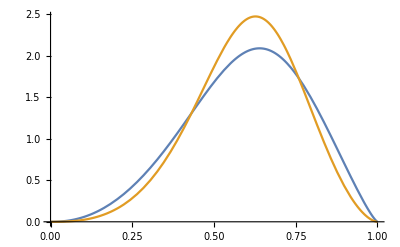

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1}]
```

```mathematica
(* 25 moments *)
```

```mathematica
mnum:=25
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.000012626368683821584714855726957389749714562778229484129862872917327855010085066875344334780102358104234657641587059224736252949899423393796091763731682531766226572171307071539004-0.0082007879690902196640283959118678610031535727934875891217472888254642731267100948344529066127043757439073941073283417683475233747906638384635921775016683594150175345061835671059 x+1.4517109566647955752383159216614687830514850747857301573091250250720858382539570576089252926765732971424765650538661022457735677303071014720442229880003057100676668826117601246 x^2-48.62515106003803638531108941529111227691542487643266190630419677879682087196655226841837660410556116175623403155392122590655506278083942631634422718846469720372650849324881807 x^3+2801.7542944107342736708854258510547731123184464264162988811765119512102026344054006023664650950605300561534144657663658692869396956763901055204139627142022798372391672035666276 x^4-71090.667978314651745552472910858051875737137858265769367418953294108103633095295930130615749286915216765378262430816214859910910670307060292481125872088232444890010773816824674 x^5+1.1967635388870471915763901114695594618904211871142830777332039151845317823428151933704921450208355807545598724227572953487129197961839926155188520484193180864611240133075766486×10^6 x^6-1.4346438003590242770637163940858313835995764873056073151647952159565550691951370449397946794805615471182744398196929311348754246303240369983983529915716599681700623015838990993×10^7 x^7+1.2776582211182797851076797983827308799993234064239113323149356358817192038446745814730133338910797561443246833013379917048436697918502199379300472520681750611961687706370333194×10^8 x^8-8.7010532181335023472555422382397291835288127711878656337319622004198532616304971124155995033843796310503461453884758719371933961009449621581509774607781119373762204296465076989×10^8 x^9+4.6266433284793361971818845189739947729467746283352684946123321962773349560958989178573703134617160445003284690098242654206685712773814685372300692053030067716562209830483592103×10^9 x^10-1.9502918228391419180433426675386251330607918792308779382755314664684263326836093911583007482690068211643164120584557404471926614945835697166726956976710620999675998845107566025×10^10 x^11+6.5887482637645125519276220424665416238045088420660694913172631583546650731981707801741945642106122713537196641801557741713536908098414961609895485335752261596813075078347859554×10^10 x^12-1.7970877341688804766334938038542139416514437964032966017033432569535488575187758402280988961349527850680422905608048212152473496316202887803097021360040774501273762911778101306×10^11 x^13+3.9740805467815604202474656537724425513400231613636854623564063521602316468021169166442048488716217657545632668663209930228256023050251618985961869455623122446803884619115323214×10^11 x^14-7.1343513806673949728386465885304051782233446402546896691367354319049923583334828994243983424908366508434940472122503298271812428511814512375799766355903570486250556865942788207×10^11 x^15+1.037873164741227692852920315087031276051662538223658549756565818091419856392088213589743064000511011650685376797892973673627628787764657762464673709419183824375903851367448314×10^12 x^16-1.217134236228605259770040418788659600297027179405515991917713748783016631955818877747584526147141591596805020064904044660227589125984417827038169769126118513804418759424769146×10^12 x^17+1.1398555601250814656370546021067116030117597072377954375146226218725403632895662066267861893041111159372615794861050550121877850099081996657910939530667519353453295609191356933×10^12 x^18-8.3977997988211373210126236610393013929389596752971889899486997387861335644432420919644623153945466575904272077022114594308733624085988858611797193424204196818392019952538761498×10^11 x^19+4.7559169855685674012982906989472278009760714088929918941482393604185988561964498798105196667193473045778425815606146871963464562555279052294061055808195663671749330203637537425×10^11 x^20-1.9966040838669132802058702131664392105295868976010938331840627825462018527224792346033389579038687550182332138375025629736218101870228950940258909726605931733210154458601841987×10^11 x^21+5.8490856478194978454638319300382152881117381008818882940498939579848934108984285312634470725113201077271413395202529747107638555795144430202126017085372291767635717050983620031×10^10 x^22-1.0668095516715983871456897137907054416281973186140438702440218497432792598015849695902732651740137653008742075837555403518061246673350860225477044633317059155023034069754653245×10^10 x^23+9.1164669076525241585466060926579329606877133020541550842992398590271268337431504173089024522053677231005357859583534653867538148118763705014561215455741997001214408466584657219×10^8 x^24

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.0000545510348365241125984084127749357634141257324529968463230547492574941606332550703715712366858630249844984381248347538133769694564107774859489492689946420632183457609547388119859-0.0358999416056992914982920755475391170886589317602489445326935067037752992264119993921761018744985103698479426177569786096527977015650369069084779398167254154000815287428398548369 x+7.78531567827759407611231031421651346841791506349870243785498493926534017591818268650236630295266828568848208944448353171921927211586104274392405458785702176118951164640030686459 x^2-268.814179500128193359379427069588757944778327885694672136530632361782653367261491267240445576089674605552887760439823899410474523624542887603509929187821850284358426909687914203 x^3+11844.2297605941259046222337717608055207060673607841967788414991391173748290805422645715372915241298329491080015515458692606015806935797922697722544260401055510900115702202550303 x^4-296299.319298763881223849941107667323623514283108590369623914821891529838055233181340094923290563955233335528399769567873025147631759904463518537078797796207685594455592869246042 x^5+4.94909104058337517780970736501920810210374042874228867598861584934181099216264198329549795424012193352070753396756196194363403668476736683268885317284987202844709453704351822903×10^6 x^6-5.89631681406759037278693162607746073309912434586972677608251134610501304521141959385874658811579591966321135713033736469970754249837639292439677686542274538745550170524993377304×10^7 x^7+5.22078953855677917631122237552079026291259531386470774050849613606858602395222660097604022701822044562301338100622908821340771137159862207443228261056870777345675396151476543302×10^8 x^8-3.53536022291233236795737669905129801872241302453783117108169830135554960893386356113858995801640940969790320401040214361838595253334090724429271711230972969670410698149904778915×10^9 x^9+1.86940454563874549805591163361235697983725924521017372282766446354718338716729496498462993483698713651827878269053951105095783962614594859475148718446744168319601739790973597921×10^10 x^10-7.83708370192855301661420852844522827538088538882132949437142892624408706486725405912500044138944321584715407089361149452790453679951813640061508978355042172743669594541322822105×10^10 x^11+2.63352438758025903071238466051753123294335065831775956174230290913836637789671918582479413558302978077452996611202226811842206316468612129723881606163149189866349765643749465989×10^11 x^12-7.14613585649720549421678658595448226598045021014502745978462874313279352242159534576785896834126149295976914447098982113982814014697035474250520191406640464513743624384906683977×10^11 x^13+1.57261998184062805340285324819581199368037122430496022068736120962218932664650038008696895079190322995614911456287734816131141677702423326243482980299983822268372467865200996209×10^12 x^14-2.81044602213500538024025752869845554344430177366122743942502551909178599682375903278259775459713630780906392920589053712643552427590284723652330718324961312293423915991439259597×10^12 x^15+4.07171524429674963032764151784616307577962710740077277583443154816895949658488251976059221352472539055480982522316595621464005014298131222520762198124855215652836339240384041915×10^12 x^16-4.75762434992987185678790683145349114161048392651339331921906334103028766350734933498933163110207184429575773042692967311850182835301603289607041962447982926332582747685970434021×10^12 x^17+4.44169581502480306999320678887937718314084513591470271373547395002163001522843431171685737685210763814034447655766787691627422353984964090017269676382925745613100850663010578889×10^12 x^18-3.26404785592678916650695033442221099269047650792016255817357335398895422705106117402876458255832143293124959300059694774867075736125684502109075736702175541525359465513209614845×10^12 x^19+1.84488866039433667517732854494031705277491579389798182514813274392759651035243559233163735019442922916677536888904354318561367201772340479667693213682723698526807574719744311841×10^12 x^20-7.73438690661166479266564448811704308517792689861577150886934261911178896557103176914166353848184943568689466408512139656674020283810313332336288219335765893767299335707154318673×10^11 x^21+2.26394569993854320874961044285045420981543661675794696365487579151342639809614489656035835389967115406623679516293313100404240306236283950058144292116653361476251948870711306812×10^11 x^22-4.12801936590922978396008636160930249588432805060708800096736181880681173495681983496846713834222753874547987944935189357337658141086129540302406215966058737913383249163728241121×10^10 x^23+3.52835927845615673034361032218228457154893804471421264216462398654523751823610895246388915650713196502688754097920376191439554281819662646535944686393409389394551726526486172036×10^9 x^24

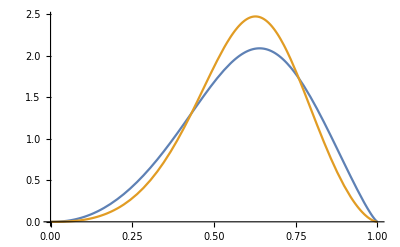

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1},WorkingPrecision->100]
```

```mathematica
(* 27 moments *)
```

```mathematica
mnum:=27
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

8.22804427814640041089677802982537369382550443726548264305687882386322418602920577608219526496899863533278473274404598712029421840448905223242026963747710465405646871592496191×10^-6-0.00620408701318816110240331449374923836032228762381741571474021076795380785929387525899526669301501095171035324542143887472891283690070318518798068970469491260673587796522395525 x+1.2795632406252474601639680419583398356615308378693888140447507730051667869337051068903854351065749010189583198162903914568002080046769396472799512893113779311573365731229369 x^2-48.07619084249812241068449858125183476635645196810320624044682532810210491091996094521602086173846372232689093610292487434769278783357282509091773309278357867079938802567566 x^3+3291.82319373244404555781358195230271424526163496937975387456042251650162645831675430027845173808545537753639189203354084054454189459285426823340305827252488864266197488853165 x^4-97570.4640299144800259575740954058700318022158475962222241289539220175604619276414861307212563007403606983630142363170880504181834663106260623700781945695211912292774501706168 x^5+1.92049060355039006928555510258796978477124109618465703597037412565672034525204974405711277843445549077837458752308962759782455353921006825291732149652951481601001864304690316×10^6 x^6-2.69976856865541244883754527351929763767016760502035743519592609106688686543622659387333180132054824473330523941329100291678988793763212315083344024062377227850669906294172914×10^7 x^7+2.83043682003183988096550239283646806147445097364089378382296183314579652844315112400545622964867168446758825550421080070417927162669404323337011705728150792655353288850098517×10^8 x^8-2.28007041952778538492895544809008432576679413398823216166505914050485310165812443786818392464349227910750697830734414807581075846659482292484081468870250966834165204056232313×10^9 x^9+1.44246255343874876536681921797853642586741530284595477822838631785293983119034702857294578785416213582676113610406851341272099611988707907598021870093223133158487388201522723×10^10 x^10-7.28503820161540500159303667534844383725002970888394057045051583881886975889319791404580421127212150683062765710982789523630999247355694120694554082532963608901458248002890962×10^10 x^11+2.9734288379407769495832874503905871883212434703264983739431281099685822971255642831418782192509161419731231362435851014008109520170249144924038238107549852012766352399220532×10^11 x^12-9.89673376704576171376574441359271391874928406253614330068037928226092378555185658700541014519433339087003840391581985837744983979611955179256030934085954144873136280057076132×10^11 x^13+2.70302686839269367784353423141251051399915796022379703540080250573909733636162563954888855686153130422962632255417102144744944526156434881834918239339148133081093127264997335×10^12 x^14-6.08105985762310275734764326208659071794511553601824872326314539910300172778259535072177919628056231897576094684885491158714536434864060232807694389112089711392037457704729033×10^12 x^15+1.12850793460092974190316132592352009530618973425446330674067580303589074268001993168386540935712951097876168311277134250066620228740080112729006005733050315665145351495013251×10^13 x^16-1.72587613831998339740350867488752097792144106902228551304852469232403899169300542987821780307278445252480615840418306537838909256781220002129871170872657826353137954730639339×10^13 x^17+2.16736942257461482870092448093976740962843288356323885902630845753916416803963674974493980471280663159195134610591516324905545102568586522053818568791783245855731618942995649×10^13 x^18-2.22004708574555055220167015290303790406024890092580448194241434135062912372834088953944046525425941690373416076763869895808187938128480251027126956178377438075351249332550891×10^13 x^19+1.83514219966347833718938171491186864391734440558746224256092851338834445559688894689754458786748700812649271059417255497980831421644405724507751965283930320790054603620566248×10^13 x^20-1.20470802775441489134981396690934336514621180535974036862073858680629624769557125424258195570615613485358473325144337634190008154545173329386153515983594558011415651914228144×10^13 x^21+6.13122357862982216125537326844970902313395971453240317231019800016515433073938717569924559064024759779215153033303445860129829406262186486147954790557721060070295358294062839×10^12 x^22-2.33103799784228088657992843723933240929470139171720858044322678566763587183446008405345902655725274608520419752499802942981172027951565503990886796801208040257547733556450376×10^12 x^23+6.22764464766925333843304912463602061138974793125433770991807842752158963296529163072677605475293002923541589704582903200694415226436143405261475628723463319851271215995119976×10^11 x^24-1.04244464106077325862854826039246070385527800717787791300265482512418707794054745133636066872481424324079443796141809023922845673211191758490553809264083718105667685700309733×10^11 x^25+8.22280524159529729817041153975105803805580256710841913000401686262434495560686456168395506614750585393794960416924563128730683658684781109087579232209211110021749987373119389×10^9 x^26

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.00004112364166659226122817994493913761146853954535314075876562250730626899420361378049674803356922938048430936025478796913107392541356124002781546888381132310556207796328128633212-0.03145259265653001995200975632089223695527670421012556720632424469124036327533101064412773947236444903149937070646273153693919684372015236729811279011333734649815973698625024269 x+7.816065283792940874300840043591865606594157558748145778319442010620810152889679126506500887762405580354908127408262107312098731781273496162002591502750658601429655948150404406 x^2-329.4427173499528033720237555787253669263799409744994319581422563754730295786254178666005765078996168055978488453382709708051779758383477971271723280746279532577678854373982601 x^3+16803.42083172248329726495779024105753911718437851685965788266824715301706404973172587365195697934147801282785116969911420936551623669861326196848102946863744844386934505396817 x^4-491419.8705237166770059700535426943351809196063599908912156138779875448045221898154779207855295956982044404545376230732818964425441026752187302311903639482352384923665214176788 x^5+9.638433159195823472682081651663546039840432355402367615100810912638136676409949202454570430596785264955582506412224048425939299852879317337837311627348922563813503947253738559×10^6 x^6-1.353746524736108723180373907979863069203503194796909889616893162869293888995762733828427337197321433922318200929443852408476934604191985504604307680535441590389794841801731097×10^8 x^7+1.419222085540856115406977197459244257577221919414475785601028239831165791166904857079605484531103760265309290264576861733370624390114502588999609655339088655758109400933965504×10^9 x^8-1.143614802181645686905223007589749272257849472621260082978431741762669840737610090248941135419109540989823676022284838638035277919113951726318443102453743346807810697658808419×10^10 x^9+7.23818523655884144524644363229889475988932555691280708698153374335035391756886165787079860232789256371848663185517532495761748972508798897970249438305634968662362407723241115×10^10 x^10-3.657326024324697435668251194310773797550009258124659047019536104859784189809437181596064338397237434102055180521204853007410822342613376365506956995525078026812517211287444509×10^11 x^11+1.493416752343391432104011975167460928790183412646249652116725350593505632562377006701593740919885182195150772366114130653973554001954696511200375666434139229503707393516708166×10^12 x^12-4.972466109252555610549216187792512698420856047854228922848432511041520155270939732326017546602445369624305656217150143682123657285805294989405032674292798061729415533496397942×10^12 x^13+1.358425168822344115364273352399761667152198561052731901977882598714098758488091772641153235077144655465553530869549203845750113193451394997432356009613281628551774785086532655×10^13 x^14-3.056368030170426099169464164637351128765924216866991835176004143164852972571954177564375047687678951679623906958759415270258747859736223637259998142634997229401006420032902153×10^13 x^15+5.6714785821394476130409898020911751385315555420553508675679417388726627775001765167873950896842157332100366620963414578191391605563932859992170967532981031370547970261004711385×10^13 x^16-8.6712482963455589696537028247559879698777060684161237383992082385648348182853792856528273870050610093966035334569457311627449050592291867423159441471318095591147971208863817124×10^13 x^17+1.0884117691442726852536028783756677206295622704662607392045098443199642692407384056502343298105377514996198267746976820511708556250876319709633883750941073541715537031634737698×10^14 x^18-1.114074542124157718749080430047628572402103082516344765085116374810919312074258077838924474376031034021985839072215089500147478133026592870673830962699359581165682651828221754×10^14 x^19+9.2005833558971510966593939066665489018145454486510652062854297024991755605877712435230974529757821677641059298017356093632067574842377298727129598001229611251484241125667690314×10^13 x^20-6.0328704478488195543191715278956274519370631530736606253172250464000938021376834790579841307533013221431613765009222579914974941486406976985053366896437146024879724845281162768×10^13 x^21+3.0661455071676697546913100575613967358021398457056829021120719274290690735167723949439554876373891343516133732399985995632501801261124493105478343451791626960494692143590752621×10^13 x^22-1.1638887609233507455294965168942473329356659073402601845837115364245375479982207754306387873163050020869910219266175361099456784155945470024048448784158658169966011346826997647×10^13 x^23+3.1040138905321644262860519003937374019010288177351402070806591814380254420361177848963050620562659383139476433948224349389559328716414290666993968786270855148013367571239256938×10^12 x^24-5.1858640053189802732839927702207044178252274995766130378236438708713361480488935443379712792192135175778771220396949208830126869626509605051581514485959131926323271502675428599×10^11 x^25+4.0822264673407306668523885516667596604154977333443161052045934754561464853894674077730122895227730798057919048872081992014897133751245888225300886586525146405688497656038853227×10^10 x^26

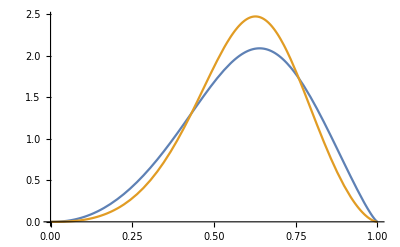

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1},WorkingPrecision->100]
```

#### μ=1000 GeV

```mathematica
(* Specify the final scale mu1: E.g., if Subscript[μ, 1]=91.2 GeV, then write it as 912/10 in order to ensure the working precision you set can be definitely achieved. *)
```

```mathematica
mu1=1000;
```

```mathematica
(* evolving... *)
(* Fewer steps such as 100 and 1000 steps are okay. *)
```

```mathematica
TmulistLO[mu1]=evoLO[initialT,μ0,mu1,30000,200]
```

{{0.6,0.3781865033401490319298654510112076049129476635162012207550402716788888285147723683634435000531832194213339112411574107785589213257876763083225265858159132517938267644867836403109374281465686532511421,0.24804153686439732260388456694419461222015238611133584911946328959856136185703751085512642228817812381863388337112748370082291505367795289378334624248927484427658992968493692109658590356364479073424,0.168218561882429555067359804150419080352038839544463921805738293037024362448489503335247621610859111573464498766710151408529058670745525944260190272646683863911959258995721756613068928656229194187075,0.117432540606515171057618982555013041490249795249452679972808830935507580454663023338840937113257239570720352292952590615539053263138758043538676201440239205850697996864190391712054809619205271866384,0.0840932395764947682314404316735807026310270047954409152516660288250673164250082563743727462690922927567282211790192167400760332909883371351596694980477108161534183942465039816394735629592968862793304,0.0616000570101386234311439862806237342323535962242568923117923907385494971576504869929252668631822500808075794229279106494065716047580519713856189686652344383239933997092119379668363873363519757631806,0.046051247302265100925316933597221176863511802943690011247277976316758273691673246978085736941939026573761163365782258166638306953865758685166936298576226797171842944588210799518123010049286444912859,0.035065700462726966846212310889298738678628539374947058645890624388410369968555477930679221847816685968521291974177040644421658897411199172194450305572215507410112134047956634246359151852110202669071,0.027149239320817417600999162039898704776036629834324321336184803319675694271903659634191454709097945272871296916877634501032619907232191418615593962792968689129664216687268685941925005329520841566189,0.021340744183286369268475514995614357431734182120494041521836429944489679498909059541798587388057457444879449523821114921469258644139647210221982413241634016111129843406053188677878028144417543768309,0.017008054788910690011528062510123014751251981674744073197509406265539587353125584361435566761314419302432841020579265398466906541897139750092847472842898566451254045441800893345429727740994036531457,0.013726877944741499317225306612470280295668425348811106698993706487086605564172123970540561565745326091983855608157407407883892462819435362338091753947544613112297018258333573315511445298051679634776,0.011207111536100383603892392082143491924334779753823915181839885564458366873433941059583224197568619975311502131808173207435617400399188942417439735289258767085416657104752402696744352779855334867304,0.0092469906576898133996790739979796301250715076617945925663081712095316030449671304245212283542536352086587219275029882898449235806237622385381586969259468156034876756935069899932452384056180946588093,0.0077039555196391893324652458177354547911164576167907516718087166893070909731643418551955863516693052750454456390246333937394491717282989591708904197071842483806486913215795696546808894705166944658651,0.0064757904639798390289589450601160412936012210962441068321550621155116151981193530140446251520500682790721719929877608769093582051981567128394392525991908788011173358752405370000886237118315366285995,0.005488198378540807796968024667322925344922900998633606319839804879019095936515366437201526897822298825700427169246677248380961874617293567432959561887909765071935960366018863418560564189141231002383,0.004686481538225102833791120104178989347595657640085780255015112554735900747558316736528405365714958285082211260760788626580219624220405759927525308419021113542101851368209780810638181033144757664997,0.0040298874075037833374554272693443165920053458285901091619409586409652503976788651011539206328963882451314525836187059951696282921620237625378408493942203979799192600086152563396400559659209495433639,0.0034877113194013117388326842475776841845101327802912624470304206315979756398510243610636236932518535969362864132170132580520523476635235799399974074433395184449847841393542487804010789496730396191438,0.003036574494915629856422131635266503065248890366894358803552089497611533256508421394624050261917625694741385819654371285193586760148274549333315159458996179626547563739554901531114493341295703321672,0.002658499245143994612086635872253749509750605583187605277850281200904975717765386710199068695793687985563877843566780160924142384161749503433480341580437261453151086254427300011257023089457135187293,0.002339531902159974237876701054153217198768449395604730618326763632797140212282635215353868407127163161895466626362134627627458654366252681457739575454225516184559015166364748786612026250053749703613,0.002068746695969736584902959614323002742481153297165041923274289880477007225069576200579875230813012016890271275381485730783562655287037557342048015068498630004649830052146303284401150135816111671843,0.001837517645905836933715951266300835820357729806827972983892590942366231419090510482504420432910442062158746054407461020809204096893388605775413238715450998223862117129090749645218557703072306465868,0.001638981077621959887596459490588379929950558744740956977641855429127866849249454174859413569996334468128906376176106947861004920165264236334824047744720552420884260665578298945253865579407813468292,0.001467635129185616680685221778709778073740865408413569833310452689316552365110658990027136288255392056748196123770576215303701567463145709413777044725487264480520377404044514373704813375773196893065},{0.6,0.3872583766837793502793971602529679073695596602311034066082135863430630002655228808140076408326449732249780317580402925567091165801121301990629132961519277228218242287850613967246347733183468242576515,0.2637590827292924402494127825433464783002612140751743505825302874641298731159425452070138096481458974945778018799386278649127657206622405536413912774104355195563898324802553730402163972519504124892686,0.1873647076279706918311369184781755391045961893112565648066505353809115455419362613993680939950657125561113056877616024766764898418108150227531241835154823907910869702665213134420629731603485086002618,0.1377232886921989624445285984857407341381841864095868403361000887141628848023990626222856556918501277632789939627031982962612224927442487165160627723615423699473923453778854402208942983812998483903697,0.104154340354899248461015408904185417038297067008715113176581301560615419403598449827361899662697136018588049019123043368780391673371993749576609239238371318224882842962547573868631658485254959967468,0.0806871961255153800387137185981317684712290937879155141306462828820877018746441122756625454146591366694660530867472045381412377461233687244373021620047334746250813261707830952485722456332251511767416,0.0638115388123624126930918914192301615504346042191797184845335280607081293987383583089395458948328551888035717323501733394795191927359899328191816315787985727002882824242848563059503872843425663130171,0.051375924876821776052914874175737834978652406617137621310651862961737881108381099566060913771958125230486931084946018047589599710908892233626773890508048608986596429466421189212246498402823767977118,0.042014539630044242512796975513360294598439790183516263547754445671587421931249079544096515474627363656392765146409068138307679462004839354165117448642240528422414034466085028791125864805740237325788,0.034833609742553218347753150925099546027223622391268300126376026368875078203965748053068088580760669494060034139026092686492331994165739408585133805600296802249705360797436677340402799629266814481615,0.029232528026177191221702305657024051119758523128103310033284313976481262870384378036020337459686073456358544942141063896660682186072665487894092667232264286367369522042517528222921041950757387109686,0.0247980971699786425639660803954808552329945520562587401834155191383877348076805610878689476717817175900914641706394985422112459559792143877755792290661190351369538679278636496391247317150229473977808,0.021240022118037605773484751261180393098087640578825822622343885171350345441179670545928943426438168263537144065740352517297779394243052349786477497473166225592968163848747232072855847400326634987217,0.0183504649008695429836307205403266190709317825512663471444477055362981958920529472875798141278089437140519102668129991359860628236221172160010982008356505740292085909112611742775159786554224751665139,0.0159780563929921185260464198185577590947476305965609105685319243019922356913407431831686704499740817177315409281032963285379035499975967680621263200915665685542431281653135394712977406879550929295892,0.0140108248566461641663793955611210713660144976548347750888402805312916605390452041550165728107845282084511940512953281274704319197902253615789575268162451700512689626507908442163119245606760237790565,0.0123647553773383630357713185158775826354261887116656686581010343931123224443939404310112203028677083924947162064876376886615230450004897848336671462454868150899094982110476591570954679876225624739133,0.0109759818554841861450924823201777001784856061065332525887505820783491529571864225222413459711447973397891194153707741599400554530131757156229078305613065237426419079276037226321334009892655158571689,0.00979536840845363228017996102997997091516219421078794579635260923369996557201883460535703826084208345163104231043464970025974141106921741785062931973913497995515602575366585679616314001081530194144762,0.00878469071898745336640098751660866523661632220582189724088517409318947706228220243882907755728186058781793078244563679070734643941116672330471399794568642704482663898062944566904496107721838181226849,0.00791390641983595338660577639875450226310342840932821175969465099690702641214147590743473061599631857246016888377026157384006624606696663775900456101763198706796949063603991838273675413323187710921551,0.00715917807637035388081338875907484816213488546584905434166647809190738979307378629266989618133909363220566507520343696640794570666147117478647962920859138042687385430445536248917937364272750052061497,0.00650142363160904012937011443761483782921070723960442135318756279556770784753206158714427998164742402814375406735830567476810866654042353099176100887363575989201942168218474751207345860517385286271363,0.00592524139599617083027020889205830778552430007117845001816027581305386789121018630431361020848712607338818565273687498806744257649694329119200600036208262376370130972002679041396373627114984512966602,0.00541810426474748009247258740729041158063596279341624200395554292430293838725244311736288995462727426814654784514792102474827838770790426988853589567452901417557680929121048632157971361717242964978687,0.00496974968273095413489141758326996181727529563331771555557318312117048021133258234492554653096491309745530110694480983013679284497801728401650758356071524000588100652454154357879987975425932394094942,0.00457171346391329047914589894660303784689045473683554689399431775774994494352188781857017367720125545784252431330862586606505282893388449849545533289286706117611895521201771569730383107170371176833114}}

```mathematica
(* 15 moments *)
```

```mathematica
mnum:=15
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.011996590898987765554727198957034233925979723745636037222151308307555541943205016542559083971480668854195799826836726393326604711622250117291584761439690281618690210547289352840501568062-2.84735780529825462280717244983999155611820238036509275059154784958941388792183134253543402916412639767104146121990885220132019747050667528946402256691685884950280450612699651433592856481 x+166.127820092856488478246063294908568114995681601677871445123775986753474756541820610087445228255058217223701854847388976227515704855336396115007809686975586420329524048566616206504254581 x^2-4187.89116316729562918899079548817412065099437386402677729548487183198464672062163452103817297016591932836654850949430771205373427207027828169081761395973106516088126388135683333264602112 x^3+57346.6606180023156636386727006164837066429396821193490326080800128304139751322877807331122419669804785029905654588889283838669103985011913957295809306520395213874594106134437351751852199 x^4-477180.377536120678842859123166997256964837959572197810954846915253299374291037488964850376563471637862603890845763830885370877072033264143080542704853520714978944344148453952807020746237 x^5+2.58835510369713716923545853141701154606328974206071789815538955450886659497972905137735805989261542510262048100335293411974944118397276532112552447720581284027012868185068815918375179916×10^6 x^6-9.52893318043423086041529642493452884959868023618902911122390171011066003224236337644307052225724261909419794101669918306790235907204419717483770406843265116056169556998077895749821985869×10^6 x^7+2.43518304145134808522743801195969584051742223084451322218855056190395622270717080450552696202202274671905714416099301300131768326774837154395959117920348776884755843227226970966916597192×10^7 x^8-4.3558644357630957374441938984678880555251252012777291097448464509993438988565612492463249999529063528881167251914393767415655546246976943109652080259136119914189583281332333466697084226×10^7 x^9+5.42453874831124301742569536316023130133984960251300345948583918112810766559096653401827686911576009739867653994486395114304744999602302775471164714347554681898297866091492456069610847594×10^7 x^10-4.60113574870193153379603847047426593129602333454996887079437013384464799492900080113893530313903644332771998792647233970513471052146981467412176305333482089479084505489808732045182161987×10^7 x^11+2.53219475642279440056386247535138237629624338153502023631810491107937311507486981313419565083033844190636520488135492316719619620699059098718955269537057026952756648232470228908071124868×10^7 x^12-8.14817587015055311080440140148310695338792177375934037458758961186403774292052845875280581867734629713440427928721717056579869915901000491461099259359887349728901572629841651248592857978×10^6 x^13+1.16344864802867822512908112816218994116686175549273699974278627364143727520884682777918443423346621216910512624030100130367628714978272678919993217644974819729939599012347871090852807487×10^6 x^14

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.00217856187373978157935101925716114071684139358870323442021018678589537698097524962859678681021912761815912479237104638573996465450656595640151662332478046920800968019339693924495781704093-0.516877804770080519916786548741855397233251525265181862908723263689094570463380572914252597239196446351041333166120358764770676909055802744846058528570025401111940097044777605062533976082 x+30.9328140512269661588815196388688699664739489463231932351131772661485345012769038149854466960333623936364261698921379087749430459226891798835790112895385016196467322643486555508544282579 x^2-711.565808518770905760920628243717845469356042947549570221085594390023892399888625607553172315237420056154443836626180699599832606674047698513495636194215943257581479513664372599322102537 x^3+9966.98218069657367855679468023615063843119112751349568620349923155271281671288662379544481037735711965880927076084536380796172626674665164000249107427581057532182326689228781242750926516 x^4-83270.3843151866286905468770215356069054170993229702057457839771800745051024489681987913086983588146767697576577765625832128498509047118673925868903244577851030303839218510552117871246676 x^5+452385.120307094036028893753288358935592635252545832843537474768059020205119998792891872724505442920329577921945249594528053322543842802522501109108896234276106102459514563838331845621009 x^6-1.66735185687829701777394558004124881052064349847625048425387406850262655297795454276099027685739611943778172757019379612152996629879249108123586195491777912570798921724888186128760090828×10^6 x^7+4.26608036764792834114065766014707266893823486114059378856375962121371915952375027692859903077058880284046445347543386420112199883623545690294879156107024982350850901726232235176273795243×10^6 x^8-7.63991067770091459579774161519565089352285634915474047369691790420013096056124929436535081803374108048531131530876858493252900444552804361130925021663014875805119816635028128507165627427×10^6 x^9+9.52273050750756526397473920436454659058672325442278788974651737335605003811452514994545226600864414273394531268868735402509351581674305500258632885125602576829187869204717141798491880235×10^6 x^10-8.08007653059742539349779351470288881622690216797695650157718899893100777326739713519513262092802177232401550283383166714037461368021337714888656840661062673993042510008061424128519464491×10^6 x^11+4.4458004289905519267669901064782301878088979893690265382471950280340652062334545566783561777393283275816845076451672489785151939261620517589608256992562241580578708186836983605232686424×10^6 x^12-1.42961238819970967368872710751204549010732269774737460119856134721572581008118384976812926106999886197213712826426401866147629220118595637385909926962143888121283928070914988421026769952×10^6 x^13+203939.576735803558791510596259977217122461196715448664378854487651617239788780832553401889757124838176868669425896136050123011690454648916914750514238808699619269982306919449477510184689 x^14

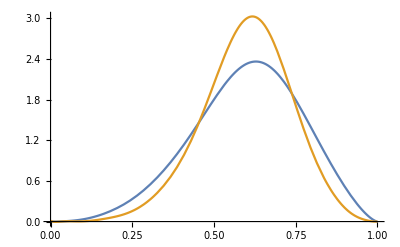

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1}]
```

```mathematica
(* 25 moments *)
```

```mathematica
mnum:=25
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.00001814760961302041272342114836565640637106266670454105031340371431641227667587703772570945060455712779079010857750825887209795093548044337013776351175028379115898356835195893652-0.01371654445107342248935965653498306419825620313820269705321396678805917318281989630982817747158122903563941172154068955242432712408662555684203895821740235611068998220719732763 x+2.51911831178389702454233743055513032802842822757876323868764602462637210701068013822108376182145348627540204349737779305697483596179767949383347023881605909823104906030496006 x^2-195.5722302053506374921818860599131480506922908894237443625007716809843540310587354551731918973278656668729689842528885979414194746912230501272169176899661342309829612539285821 x^3+8798.662224477528260295316560039913895061749337850437297170609904156360035252647421218511084107508656604712756422474829406788480308165947857563850096524034570565294513938974892 x^4-238665.0171016576431815281648442560885191139262626187713773449031376277424599551662376777392088911560487247743751527438280376967691264189385934585680972263414421846838754003427 x^5+4.3763024887146646254989061620453811626305342783896790885310981997793592766717436014834395947489875409036432872271065375474955797775253521333454258261031938419881084875228897225×10^6 x^6-5.7140619360045010025226174885200696597436909602979611998018942556440338922677018193785328359074400176136449794177621118626790793577068935805777036037838852491067075352914476707×10^7 x^7+5.5183360872083250970702743172268505779879415284080952606198444618897354316383797787627074682618888637050817309528550364247660308620828979117623490647687109328560218544679167328×10^8 x^8-4.0526166856166633982596867225929978487023965272952463132942785720725221834748450295608047662670294958405641222565028740678410228288926643682845096420179292706972415735882306137×10^9 x^9+2.3101829731425955846977007670681944474402876816154361177937946644991993856537427832556784281353570914495722511723674692615652909421748913940166693508267699639127373750891332639×10^10 x^10-1.0378546337990049440052563146833140386027416102174218636073850691583172306966170449908885180297344391680622578680868348806544873524925871724852120155478071142370180250551442369×10^11 x^11+3.7151548367702851909058722498376476888265462941652082369032711020861313183836722839397662732946105874513071501815915583868567213303077429104699330714838324569755578262448364264×10^11 x^12-1.0676300200197080955674022247213378608732515707501566772983163408398054444348141647252591008829189749133746777875517973727302698680874930229399710435503219386431300164330444068×10^12 x^13+2.4738678818985516618097564484061955941160538577613792276451990447411172750546755499181563748323008525724511964483372031380347481892492173931000728108197793323612259778098272868×10^12 x^14-4.6288444590514665874963663887646937773170836375353609302622088552268723466449909064569659887105278648205143577395503326010163209578227226355605190169346290509988116386704435885×10^12 x^15+6.9826242766813114364750180489841895892350670755063821700309394612705774080550629799335717188502619755496843853887052251135955923755563451698650032467163691008465341859511624558×10^12 x^16-8.4497715229928154255530251631955945454254620377085558152854356775627548645018025218760832615043131517951940877294620819417907634827527128602519139557742222724226712950559186209×10^12 x^17+8.1277657300905759608312853171121253467267101897665371425789577775691744550370819067541187915374263262361413128740144691148786243565578720567710259510930482405128463113885247505×10^12 x^18-6.1234907985637012702020562448544961881972357199109026719658950924280239742954259435178824676760802294979487021731788112795312512841268082931443709907005253949903808945767874644×10^12 x^19+3.5318069716246601064475585283895786636472804901704989871949879850971726304541551150320618704845030813307041992117111609501195168553569324336728855864983601942927714764318635251×10^12 x^20-1.5042587395395167676133570973059927602208255714361546109421849587623394563455987618461156080294886591933924415610761556734340348770062508134309305407827588019295695020082042994×10^12 x^21+4.4549876519547410313960596851227744306494572946828056433500575320857103615765429916416525553550278229977664125492734572679427504919895731494428718654212458626929582645986941109×10^11 x^22-8.1875109884950184711899216863376525253595205571497512885088786415000115578946952049263927384007186026641622919504808775332532331783096762832888795892376135500864418738982853893×10^10 x^23+7.0289519862200579722591162946644231345911067539098797693176543239512108797670084113937726936844998250949764798332824243011891267485934235178548592350098508237599125881449605399×10^9 x^24

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.000030741469047657371843816885589992394415532736683358035512058021899483158296091508102895624911112773695594749911155796988219448150801916626048632162112145734796263882878090385917-0.020187381207139724996378404183867614184565626375570288357561473261659590722409584188235191262702419281449057427686581056921936787796460107741426793127080214762909528149766633028 x+3.7614399730945103618989316442090080881969427028546950476772554363254789478370566071208505775073541504981480029567795618206126605595738517042973448750116441648786333621106121832 x^2-148.76679979432994541346513342656762374821797207961400159518226597831092763121064090573555551644716941688906043253836101501744466517913489477572028791637257827390009839350587325 x^3+7106.2468431510120816383980047499891625812922268229083641064731857333411613668608393023001587259261936647301955190264867453584294406861055123162153236290402587657578414407364168 x^4-180514.17810779581547355065838570012587309014063625523431717044149851457203894902349376917874956661002404371216488299531454684572198828151281349659768188070732639777295263516398 x^5+3.0550811979370512675741667242741333222359324955446158245007445653157300462898736058750001022929877807326658279389668229559844233311753147889394087156714874281544272348687713971×10^6 x^6-3.6873029987786991666571432801829126525317337560248669588962872429085034586039508409034329562579627777678321991392931829935983292762951245878237174972268739746492014875074735114×10^7 x^7+3.3075032058894630162692971959375856030071270029419553515487002898141080464921925659060764826517669592485538678914839132853335297838418242579811235055364779180431131495665436476×10^8 x^8-2.2688594212181059097497566216318942674368748960370638323408466964865876035967995863123870846908824871820416884671721202470901625629419285266579289235763947542499068171254562271×10^9 x^9+1.2150941552888999250621720331780684927363301943637908503852961014298499092224357099576219597042089298226527954010944018510296976884842959208820320658045647250296189543440384881×10^10 x^10-5.157751216391766289655967057658981692746736292678199931193761592367200333206296355005937780857545730813140994447066170928593925442201060061868845487155443289238840722891046841×10^10 x^11+1.7540864240549555423157714821617345023027731859781300813359490387244944391642375713150479065546546183218277989228125602054810016751368488891639633668583090164039070912563135313×10^11 x^12-4.8144136816048964506622035323816915566289785468977877069550319308271493076559596951794435017589303489342409015598025512534026956187574592410797772391957114481278213757478640678×10^11 x^13+1.07090196788026594787323733161794903520069179312064349931102858492485398765725002680953805683916087830584519251983242801069472603950110658368000548883354242266632248549122579882×10^12 x^14-1.93285455839783694078681392238808094549952083830159893571333738755128673930229628379479333341980564874510187026372639266957894564144246528765758316036399588546324663872446959171×10^12 x^15+2.82552421095774652122083683693518772432355226285267761381408927099855535933776314937044107507987683431793378070851970398894323656730852902580610069035983394440816102649707645657×10^12 x^16-3.32792382882701809123145119217974034615664023525943052168797001149258158737079421819494071972046066774143610989901987122443491863479260717219047792607103017644033966741009146783×10^12 x^17+3.12847032052604970430754922967217140416591375065664004544883107107013021738615366679942752226510030774138428149573986701135012261360040661324334009301088583114847481524363571431×10^12 x^18-2.31240507904901129360660923010596927206293848827724005525728748526120843312443727510243138469467511047474534911092361909188648297434353968552057849410276489758227362049600391124×10^12 x^19+1.31317606977918867024820771242671419979308854937256311385683342067587708732805591489876510363875515550999605343749943823478236375260762541250101379437193453901917999087127764193×10^12 x^20-5.52526192764778638464054041992307965783148777106726424537999667881436598035341765834151788576737420355541051975982485768320769317070810513581979332110419313338707986391327408769×10^11 x^21+1.62148359684553431081211646236127409755666567298632871329369987657324957181838828405484577678818323951598035553390059760895423456106852454336149377651210046280425262148246587534×10^11 x^22-2.96126429836304370607223046693910400152497598291545057166019922569334624588087360797566937400275799029594535152490436085480287512534926474082412195993873225234580088124140469004×10^10 x^23+2.53277016286923358201265235681216066463506658223187504768056671191526074484753160961348949623392288624044539121739614268249972507640765889242381531362133192593557279342995756011×10^9 x^24

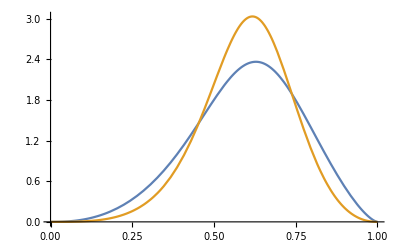

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1},WorkingPrecision->100]
```

```mathematica
(* 26 moments *)
```

```mathematica
mnum:=27
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

-0.0000268668266035893285714067119461872967592219125084771651019780185897180921641771723515613374185380847652667354591154079692185378328627014109137941132452482084561309425568175388+0.0205791195588091020328588358866395735544194643136594300658603813567198180009382244882110595867893076050962476880149133517962243025467764516014335966295081618690438445939951191 x-3.92064648014169876349891559666893947891239616369965174049027529296971559207850161655249360164401625764069852374979339219428281427823125745738208095065092786383492965317881429 x^2+333.973945531018524542025561493102707435424074981356757494398691789149453450906751202386640778046854417995407164257411806400774985572232894866551202199364725559556975597956892 x^3-15307.4089685418461347303224569533284370220632780399406866272397747619571855246319534969848251883398075750057393082099575131606701691696204728079612301680177805469363122498149 x^4+451343.498183104243599078568848515506859666013397305704848570855387203644972808068406322970951045994670562470829184401811336816262833952628987281565607910944954062376245025198 x^5-9.07076709320344094354779730646395098089852806315152301884109496348643792761412021131874167560423468664451447113459131246763225044049475257323850628220315222358851452374330577×10^6 x^6+1.31156329918040654438152570184614307753585946767943097374398925545318269871827590883226041854553868400810983121566147911706595434773496378798842024191099938720746084074847536×10^8 x^7-1.41693369469407639841469106372260446860350441098382797982171282767115412706935678569030494002944299357483213866026600100796815280580119002532166767592306590148687361564930709×10^9 x^8+1.17597476885203274806132674606694457490326663117654901700551881766982611449057603688350598135301320041551152592099362927727438730948847828006655004713293229869290839600547945×10^10 x^9-7.65582784361739973642725578593451185183810377549519213205269391094016993760417095929055016735894666436878965570273804170573131038593098702864438285251185457727432657524071595×10^10 x^10+3.97175771545990835841508343025173801673027179671526254651627244717840227185752803705458638545898848432303995626740367534638718967145862377723626292015444509874959634179597041×10^11 x^11-1.66158599037474555817268883135138402919152703142034946575306071256192771906922138184368348829730933489633246761243288648220178132099814226796048363142967199646018133426961983×10^12 x^12+5.65450431693369192311714547985187923560814485814890144129335841369065177861923780822422480261244672171598672159461033080254337874315967269876504694090195506422492859247560724×10^12 x^13-1.57476334705714289077511761359118893758112014902386205187849603223614359194774534226913902251879811276846774744449663602578382312963348398193129631190987549249064423429574361×10^13 x^14+3.6021021351374204964011877277456457137462955621938679172863161173151457342260480734115049555624711624373588602841878759821497617681052242331639110549441000754659096029618872×10^13 x^15-6.77621613733740470301924709476547608250836261532300152921581742100665978490812250315868433289005403030246208433442579502893665820640345825167667815169497727922952630918200079×10^13 x^16+1.04726335802605605576089023368671153546289729833208159068137188310176796357682898708662936897724053223927551554482395921842546332842316724121343365606237771603462536534806624×10^14 x^17-1.32490087271680221969464430074248573671813637661904425328148695402643188187436697687224938424445112000480618371921852877893812006332048782376139301365557814235564633174084013×10^14 x^18+1.36288428714872848627040215554184474018765324436641380829314253070150944286082215808126209326089762944507135893929297281157259226878061253556213368626303623519160829813873241×10^14 x^19-1.12791152267326368069581672445719553517749819832623195735394083427599420040322814290757536000346673257988008237363222123444448636314128698195678455329187276621482428842637353×10^14 x^20+7.39085367109265454387415810482430339736746096398007630032662667797228768767061170596414460094848045957588164655284703166500698429484007624846281068281574220502635028985464308×10^13 x^21-3.74384566365948644681668355732842989790836784028412567109683928900342926129729603007318898153968141981997110535793154743696289476335622055365248040208418303684864181958041896×10^13 x^22+1.41283729975300869145944295418462284571765812149455846048081383995982663993858474097309639744772615147196171810113201406091459765788579624745955027168361908317229890964263994×10^13 x^23-3.73701868077770999896878228930356681622791430987020839034920303468903419257195053203036434778678822614714400312379453907974521505513976484759254864111752362921402025844745168×10^12 x^24+6.17843444765010269999458158810791793146769529481936993298786510388613613076820509835336625894416133697310905645985550781428643557686431394560336466676394229117115636195471151×10^11 x^25-4.80304773412387252593281572914485147748113133247111956099246970965867272805764450786976177190973198124145596188238508228294422851476434892794281465060880742201738294323780899×10^10 x^26

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.0000182912775607517103027453274094614220687171411532699379990640787843043300285290100900311210177228187772113738525308739458453380023333375702741542625243258163974278648815487432-0.0138557343864672910597610134642855074490596894057929395213165537751430579073638360279807316702048454723672724342848849772567323231699052432065420826858293299771432129897821763 x+3.044764764986327248588300275794117735426678035649639539239379170490173957381308563852488746677882097247629191571345230992432768934664740711247321496570027741029720748571345923 x^2-121.5220519906472680937899721433452092685665875961869743384787291436803625260620265968663796447154394592420755158415382151241571034872989462864641482955190072797847191207796 x^3+7065.48702612370683080870667218073572672993519963744941250977865893604379601702019731365354584882988619702771499515747956210352164909637612472485745203631183243177008965373949 x^4-208346.266964097068753911454776293972715718820794098616520230047946969939574948745074394609095290280394637410443293400067693544216612293854258523746521515043973536900316880626 x^5+4.08113381488878212129331016923583903998644093936495625100366229896122893439321079219299972611751963632088574654357152555740924519978203128083733817993663115429113809391209462×10^6 x^6-5.710236280413982815900261632544498770753423993568938392692868577131867655520212379802619088150939981979907902006825703374698971617862527876202429425843232981435799580459690328×10^7 x^7+5.958259551881892334297067033940987821704753772792414302006469864015710631374395751704249383017362080070336863574928611670127369623653697442637954488436003048419241117291398247×10^8 x^8-4.777054715651770739124886701988275228876830609228989481585520689065756580826404418245846621642834279500478012717639307893684760354298831918831814461129998655892003727189008799×10^9 x^9+3.008184313899920069714092743850854572755366614082742715925109741796873874521955005542949080357120689476599354533015105187713282838879139968111007171403189070483512748718025859×10^10 x^10-1.512495098012391171375157100439708649503787954467072712617500657555793435096593321875851290885739225030051239174336811880973929352650703040767004606747977483297525558323693704×10^11 x^11+6.147334463323169110198889901000799022133110005992832762592625973640801054742442913130308417983353853320537718272984186567083537754825273660320990962046513440672370771855373618×10^11 x^12-2.038083180128616223899771756630085769230766816544813813645892632129588787619882917300687698670863916119501552050232739475605703609904689091873711171033721851208062981263530803×10^12 x^13+5.546781612107171384113418063213299794348127358664821997388218648092647635636665294656406310665079631660173984522305017622211998316965778923668740749964722984766159077719679004×10^12 x^14-1.24398196943881145520797694082729873346901078100873426578402604805037772381627839297280883300218183239372173890074896096723565855915428992601022891704488761271038295655637648×10^13 x^15+2.302431151941237069439151376548692764352481571241713815447223053558438830776054354101405531070736955487513426050628843127388182901951913330613408116635025889158843324032380237×10^13 x^16-3.513639440017763440107561666822114367639775598999945564628038087423961833767736219946600023222293138700140947731992923744803805392857699489630991873931041930476655234662992066×10^13 x^17+4.405288677474151540955595978444808599749904265003903403644592337636566158451456838550639023163686969674795265988208917240883583434993197708542146913721164542835570028118163693×10^13 x^18-4.507443955486263351336764558397470570226494608770801668052656853842147303114400711708384921518719023730327044087306217163370095069047672139178486337768484071977943944813999961×10^13 x^19+3.72388700060041281719262460479309615419819061115264528795302059629824592171091649533447888707701327555208212599747900201053616482079796820710922559180013755369690710193883716×10^13 x^20-2.444516759747696869619923751066571991540632551763431792374304140586068790247892154830023785206647046432333149486506091388078423975077563643577205491668385979160126094580859135×10^13 x^21+1.244680979430509117019748528761809463387079341990565204187833860676563674357273315796329157550202167886671301747656718657047794218241711497760271579449090319672011632766799689×10^13 x^22-4.736536885715983100889959895422810688963613590640154624908503242297437831043584848538262428100713295143304191353517058277920370197098445723987373675942262448634289427614190997×10^12 x^23+1.267126656178352532934460596214299103366135187561054258304433164341373655020666976411066762625624790939648508453188095649072785927998264026814638764432433350755696017708284142×10^12 x^24-2.124706369467169220197561404119645193324218489551073244418248635314394244510505310777427299150104110714431700514346799097121876425629917871081275417506857783759977261050141135×10^11 x^25+1.679425866668458923564963180494569159683844320448780539303407527152432070520187500051760316951957462421803779683529059588535266882482664840648481549372846645074101010681394887×10^10 x^26

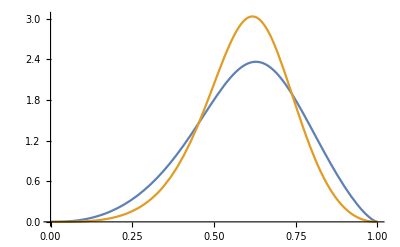

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1},WorkingPrecision->100]
```

### Evolving moments and restoring T(x) from the moments: NLO

```mathematica
?evoNLO
```

#### μ=100 GeV

```mathematica
(* Specify the final scale mu1: E.g., if Subscript[μ, 1]=91.2 GeV, then write it as 912/10 in order to ensure the working precision you set can be definitely achieved. *)
```

```mathematica
mu1=100;
```

```mathematica
(* evolving... *)
(* Fewer steps such as 100 and 1000 steps are okay. *)
```

```mathematica
TmulistNLO[mu1]=evoNLO[initialT,μ0,mu1,30000,200]
```

{{0.6,0.385677700574104985878453943374317079539486843875759016364488490828751292579474676673635460846622687130271881989629240303469991691773189604239418501647370494447064315184705029988975406031955768007256,0.261084127606450308350810634629855326133462722979443891792699268089459357770393486626161364282545571561864774205353786690380835323842471094290103848245628304061154251299285374187108923166941533947439,0.18410418011072252436439541340160892590661669838050817087328174061455547528830716951902643616240921552622812623929316425143003662088963961650921912619698313355595687339766544555454062385552952428476,0.134207824273301217117986054333106981063234760955650349198257179066261668455264031284514229232238708954845821725663554554267394723478543520899485919385369037096350884545786795027130615417865691579,0.1005795850764054489629801547135141725899171725988151933987118372328242547229542976705179166051347285096401871616733838537034385430358019663344780801049768603797621619683574735297899677075739997386,0.0771654248376000609620930568120640356018521664253737632180068308939993821441813658161307648666998208884460402596014498483247294187976584062411208890095795704032783079146421771421265472339691075021,0.060405595235843545642227668987092266615370872540866845612357641040386790771753883389037325133695334346283386553369570708653105135985368094773776493294433766368716172892236500944962127773269533558,0.04811933660936382729838475349982833904789927181385852467493566916849155598694265884574586112469292197121874564760066902798294703557362857901885620046464125497487821562105506132238926115567270066,0.0389232600778848187176592714851989773015821560269886933189275848441701221395915249563140480793524060685861297405630537525966958390492278799634712655137939281892488532133344528149208116646859787,0.031912960151639447511805738193638864891135362161497732960611137866882412512764557862233742071748042852300647082701870498601681296016073088657538360749763570531037926534427001925803258010616381,0.02648139091025256734073419420437274647505188973740743939290389562298906027161024868164549075092587257921222752877373452800105053003294180129246356101015778606378726391342288589377099532300382,0.0222115058364732242518448642566894166815239266627752716919349681002120226235627079623377735504232924753212964656958253122803935099908470450331261411983818619863228443574578025879288494130138,0.018810789573627626163271867619861777877890536309859318239276237388590826969276169132585326149701904238984478881666347764679693786696759439669793419278086491712630575351261024208413644741516,0.01607022163644615600347647216264589987255804099119775101316180249161288113314910161885087652531844651753885012415531105803888335703977080193024880812247996397290026072177503169653658537569,0.0138379153021319127970547344735117919000182434483458421916575400742631536608625287912772724708742590821011704521881297753910664459368547698803815372582599226473893381435717085291682197159,0.012001806029963489179722441492586826558884674471815961981356499105118734159796928583301999280954321311151452755074139748757419693289840687208113669970532400882618577403967807558460844553,0.01047805377419825242863768215819658356465142112336093830143974556511345977429484315228811065276129806332669285353587807640120144910225302513408121575185171685247782980511982532679239861,0.00920313104088307160373414671509462286083945481108250528225593675515843807441551405034511400584886595578063220955935210948483728994781835426875921297602365962041335627044927909104032148,0.0081283351463032239776593428846332861080661656423630900597523893882678403798261521524220404046496204142309826013370872240014042264130200526465414786593907397498371545657524058939051345,0.007215923555699425829440485808148135483586774512990383126572322898430126413939359952072467337149705839813234119410897755721136634353399266496243717344414425704780311030725347671988916,0.00643635383171983805517366516422663720004273841883771275315392611168537566518115657845850708371878506771223271003491790749910423818809789160225335817495238329930801566088505841761785,0.0057662867543772651902976864294507952145941113608131566528895683027320724413350241415732071643492987187576756002943662440339645529124350030741593775410616148366105063197746494078955,0.005187124117342605873134443315486631926469662211806775864397930952883832088785754878136160854565962367875283359768296373070775506256325486629494492647737755450224048562087520673205,0.004683925997144145893221880016636102600762644933210513143470000090039430791933490919228092780334021813086865250552051943417300767712502756625039333257557209783969602760254233961,0.004244600608214347807550772178755829233892574926680546183678272623801573882943643834031201369520338870494835270371294932545350981504066158931422975775150717769261819896489246409,0.00385929217836179571989144915430772920046227001013986906653342666499214368449939575929725144898078754195427591942499595252967627940794580149968031855786658376221003487641454709,0.0035199141981818610460512862392458553265668393589452169877135487370027802615313857831692507920757470427523509090331035581260614837922492068996943179877251261925476214886360961},{0.6,0.3922823545964936332942117109824475132078875708464949006866358201705255772922547584597353216985531578972791514634951818275362375121976005835654711668713388280938439274816914763821570324620583558050233,0.2724671968367563524569462268401888724460667554125539197999616734529696878685974320706944342241408063751329308565423747144063815347316791944063338171284198410161386189669836723074335405667829525414197,0.198025228063996867475256940264422064225306977552457433986740687177124822628468581151073719814522039295854283353054661196941149099827409928535416252917749945036546266376549363185416854347457349524907,0.149110847215677012794847758778354768806279165452767720465782366381933543618480416379552531114112776866901681855387429432187723053472041603459291670024297571054124536523647552301484372677147657028201,0.11552452753475837741525570010046055214401945639190606455570649501322198571254386740394565418139853378461629593430674374785838187821860438715876100481533163333745987822369360917487644199109224938453,0.091626508028809674317747879181156555596845666684721739118083770998320588989878716487470912162255219989450382999379072603574933620801672124192899550818152852254872687311234682150575924722402180214499,0.07411281785771023435797618277209877673447278916410070760802133163730778875137528281464948263840533585428220904574295979963305330176475377000364243394065442451096281219144538928577510561210249597127,0.0609546089552803777134157265203358379554270538854031082483513058033733934252333955539204479644930222911721966389149319877057735686596283503142180218754826567505452264142686617463924456062493626679,0.050856213815548427109382684278616852688324006689044782183279689623802003705691721960460538156041750086518941507891032791421944237653475265298192389865131965177191602440220735127726182849949161974,0.04296220184512456926955171310073731123333758110317110856189559595022781792835741199263544535905356435566330046652194139530877818587816967621994704953944446211944886408280311132563249499046553401,0.03669139648944791795569181874607622996086692398861395948445339605582077582853385088339216266664567374290922728684000990495466402336821778321851800533352554511518133373178270917669262418037700669,0.0316389835124169609535064583612894717782230796005087094532516922917593304778029246409031624946982424685324202991025090759116394756563365773711898452791661928568745862889378165058949826564425137,0.027516744927615775781116213532999829444717088969663810269190889089713332654616930205469293014715713493012125335358195444535950809414616955064359924834536525886118956121691231349874923703294242,0.02411545011741722374752487441848882299758048993903551134827467281225236781196145979332447294004290032555962370242926803217335113534148741173152682235513886362456476327351117263684471430055672,0.0212805501692513072812191469220213427303125072210628252862725854362844332895310934770563476542620097618828754851344399620247017010622955149765136989620940301115289220231348188955340273508467,0.018896092618727461304250910602181473988480610028801670166834742311007714452457345393335504784340272047924580341274879098013904933830072201094611919311828584245962872027914977313561054782533,0.01687384765300631398642234649912279829847321391011695693393319810399782403889878255330785330719813796902812922643515021758450703353816092973137052550852043720867528546002291213317983175173,0.0151458150442347965416419311761607518230128651580704905596709303933992932943667992361170593659916572395593737880062308472488247820363826430046366608983982242358074537203329004116675891102,0.013658970194972043020478355710935045171231469871385649095607745667782129633790981062576529760240037389539869186104066752007699517037739701718125448906984833117562724067806448510176637809,0.01237152139032004640878171541466999220097032288238340592703693511121885355628079197901691905745195665355215891010417840167866740876087959105850890328127990323982890328166027839289384238,0.0112502046647399586170191723583135862448753912534588047474014075654003653854773215283353609964899988558943793961473727779123537238857861051759800817416756821563794454457011294963101112,0.01026830241586661087376510876791297848296366736049884203986658984367643064527003038600291530586975429962171375837589831078757755301320137223901050912601595013619526215983176806863274,0.00940417420369065481079100705630408720947293111677911272699923101919724540650977455387687550191389742892238775569392137865531210138419354089916372753543831762031729809434861240148037,0.0086401548939281715096686132786247713903030494990715834681575074268083395593921493782663433803532854558769854624731811845519913761724116166027483414750778946562711104583937051848827,0.007961719545773469061618329545575826439413012748725425192963573516366407914551596103606538648482859707071393890067209126568471978844128960040394204304807362932786976922029124618472,0.00735684423397095017536111698349706536550349155207315348256936037684865923796841681455468742393750976977952047929444585542961171745920211643694594564099509455409898161545554856659,0.0068155123416706492516945200696347594429703327202671373549691806317924504699022162647933488662611942596431246541264738461074779675422505350799860291769697544754277974373111667587}}

```mathematica
(*15 moments*)
```

```mathematica
mnum:=15
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

-0.000155766942623443233892288346011638304511086021941246216933391547580430538242434886419507249782705280458769885890601575862648495463046398948585490652621016984712778692433480201132+0.0365898906787972019464167748411403202216950214761547389557809926948506135747494004407745625376953303939085796357887147319486618844999012006691746208640674695022722778513474138159 x-1.93333235837403944161544684772674819739169363283963993420000085928959581101823867174284160386354790214229992820515116659538306607695125440284675569763735065977606286011034305133 x^2+82.0888952427996301418501900227433247765351655337996565191350816959198980446158849163688974846042840274384917442354610474703268474143211457585486330715783907580976553336471179852 x^3-883.732062828400596355174381744322799622454832663826643481876056027583013405758518902005505977511481402031235483043423801024288232857029676123069674411047445166121398314660270521 x^4+7220.20507124995072474389621098074271148565533364994120920273635500756058373346568030283116195069106724105641805570562468008506221790244023198003623587957168827448252261413169529 x^5-38561.5392027362670178838964154103198199260148545759605198467007422932316630340070788317402475611262254262011415196094525836026936452062334015289302189548474559623295728680749904 x^6+140145.640872596853834630769155059923408522477427247920687820987077060065783184591444399539917431090268851322317714424535338283029587838492627404865467581161545773729346011504615 x^7-352632.945197852956375979124255345981241649286340026894863324462921298822103369151631192154513227786398893271583654512516290997189140653156499040944796428614516276245247189874245 x^8+617167.083344945275877196620351868896324303057576405669547689726830337007696187294191884865532447674203893855737565947565033935056219683676283718617686907030165048973940674362411 x^9-749822.881704260105921946639370179470079570132432871944743699517515996889985077160060198574711848492706445676772657650492365227596174752776427098107914353547399342549695518108357 x^10+621496.089651901930926438917156330317787798900366547817857964655446700698904512527615211707924024890226004896387288307821670685082737440714016071042445826980997839088153606464654 x^11-335553.779978050991408858502241120646922665621936729068425058932201527465033083306848618935632475209310644085771027636388309149511508614453493125073997375020060159638413048008661 x^12+106321.541322326005859794719837586829736266010115087150802813377794477425070209493560303732090574225373514721614361055135308999033696095360906364771078342348567781520832963492169 x^13-14975.8748575089998134150900082032635777612053532006201383229491627869417031072040801879893506195393588142556047412561234415772392969758514791965248411007527131630736004051321843 x^14

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.00029995220333576122296384181174715771642757400764288104632126369581114824614265577568216536545564197454354785139117027297991286030852936143062802161398701061122795545642488330431761-0.073614579673682098407763501395278757002875691492600383361861837720366592683635826812983298820950865660641500675684063760510519673421568146022051574522396857684932692895584632034949 x+6.71836952117499182822772773748231820883041698641580753353581724974857749840730010096871643764441063722523265301210603636801865887234215706104345437942304289850874849011944759327093 x^2-44.54598719462159788102001787109995711322108381136444025487543685833880173819719382375675661861187040252415043893365707287240142462601970070836601635957867647084312452228400669663 x^3+828.63413442751331956535592382336518634292554554270313581158375161300746710149729283098518406022199849858886744019157535548195709911915206319758706468313905247113662551447019316988 x^4-7236.0962453691003123534089980198912386202271902591524681276287449324547405421159137805943855116534320327328830079735340926377180902621343495261876068547068343648148127111124612591 x^5+39665.756673077027614584944683936925152143001807543561318121711802776217238948541688444696145844269514093081295343409797663641709482579870824095067198842919458951283178377490320406 x^6-146821.28915292087819814111017214920581643040646983493969616816557711747750695351879609565715809751097378742272711807248185788803572616256969936051387795863982558924551581351884118 x^7+378695.13987421343565427089023655255381445232623924745453631524817509130295695567492443571099093947766714332310916256212793583002091381880724619694604889785958041501011674285639249 x^8-690403.49394714551604842359181955946326143152269287278576615210140661330558517250593553249155218854713186226104697530519348059680680503505954686003654051419637343562378753216918131 x^9+886609.15001878555819336636787927164511353289662048714805673548844713119191804404056181376872423672185798471278274099112874774274949720682583315214403714529513321188301272767689886 x^10-784174.93966628754708021819774027763453804112403491296044873548270343378609114287486126074136700533756787291382886623538674567527428142068756318237495986482228073503364704028272204 x^11+454431.319598329377695182049191585607568702131643779625793307492418952552591658624620420496418522086076132255790451429138706788317379175526071805525536145167172301214704727642977046 x^12-155252.524209224179796513705453518901662300592239848546209107959251624858570831980006229790461110676686545050506440284211273638973445299769806556910053046554673767184127176770854494 x^13+23696.2402391842979815604687363883875309475329368118477173841833774646106218594326032475865504418082850394866899003732821506487934217122312723570855418791632851485295860689490727388 x^14

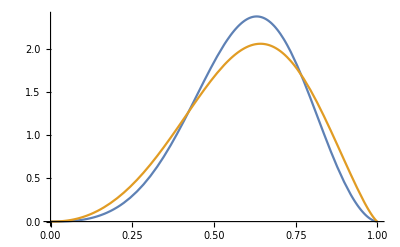

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1}]
```

```mathematica
(*25 moments*)
```

```mathematica
mnum:=25
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

9.78759908101295655331654821190019232272425917768520088849725280235678937143095448363004926794347704125285403836441099166435163611882116554493816526536462563404×10^-6-0.00633088833164134042005891079482881827459918675652823642587901564065937310763910660265511722659327934472768106708289283081583099668029982318635893278689730909103 x+1.10741272665398906944594712806764182620677776412575810852557461344744042091881229430082626225850573285175287359984234659817029698848062076481346168832551983003 x^2-31.7204946766800642683806361801036507826370940524814469875872699950881624337772518653363611477269795430311251024248913157003365476600793604700341912746708552026 x^3+2122.66829209807096283554904140791809204268420802911481487480106552542413678361250143552567263663815256463360390227419586527814869140501232806566435003965369389 x^4-53815.6564369899184782145283057580394930753636934686113576279241242670101555575087125842432231376547103370833905634233600397363024133687321055781796324451584633 x^5+903494.653647683503246822161844806551672172430884270236779954851709963513917368286199806250953673596858145010590420001265890680342577105842117104923474105720929 x^6-1.07902903769133261920624155626664154917909394034362285345438465873303912665227850278122463018154661214929573067198254511063549152780365698649619429148124393645×10^7 x^7+9.57005116864471497393072243103302512401924239272933614595210803892788939032155187375108153519648609027952129047500057362550093176426677246094548219302362238992×10^7 x^8-6.48952928293388893673883122922763136119539045153147656739779597273479079866574487570082306318545112408274034890398608343805660410019851311040981861145976635866×10^8 x^9+3.43575196022673772323719290756662271579934354646727911074261283208196813262497564328107682478887837273759104227448217636944559362660003032064067614516364847851×10^9 x^10-1.44203389258002267955821804566731087603590707855346612936541093103804884325938433240709927036310126205325744468989795444270521854307287317386139311034470450641×10^10 x^11+4.85104020061388456355489086664091789335024599401724993101150870021959698833353646560167759687601827130998965422194787391296758018043646501746527058270750879571×10^10 x^12-1.3177232611913184312535528391001415831274842783079789345682234321823670369232740339509035719246646401234807211898688949671551379107609270190927966141004579182×10^11 x^13+2.90277786788455039914254328825653646717263699451253846664069167883487964899849247247829667030415105323279695457387030606729283651114764290468700186839020193804×10^11 x^14-5.19261978599631152546642522720032349536500358497202258014714567921053073903393083383668126237402225985024763237275595429537648762070084536561453677069317814585×10^11 x^15+7.53004191070591769718165190555388520703490207776997406786991643609523440898334396175963754739511319765431951986748670825814429025407095081121788943906668105062×10^11 x^16-8.80664615873530424688379565415093926874183833820532762982426728882353827746532366369461044283096508105596319871969393949604818809609640791310756177715061139085×10^11 x^17+8.22936063041445436621622152097274226386382997082859301272057680355908974090767917988472447665596092323474389500959050008190327840342726689468325434445360891402×10^11 x^18-6.05301644345795708949178474770769540110272059554687529942024965673930426280754102614189270263062699535958349825272361568526804335571612678212608975021325980614×10^11 x^19+3.4244329984503057633068066059431771174830385613810849787794716881689515846643858462238062683548484167817395073117479679319067377164070714364928902395669526317×10^11 x^20-1.43699575590533107756918347143976985602049038184377410772366803011900712811921779031863495325815039252646511609824603892827746059882269240705924390757070848383×10^11 x^21+4.21032915237803481252953095606682129556448221117216943586252779566394150205975169898836526174178136763672204843358095741101990209358378076151275059221547796×10^10 x^22-7.68460982836799824821460373892606890712544246733959422413152261233288866793457531625768752202177008027630680560142684430254809103938364853428533723387602889386×10^9 x^23+6.57493983059325767556268440581068115971285750993145332219517695213707589071005608880278731971563081086459729135624021994891897238819531438083636498603446181581×10^8 x^24

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.00005311990862741806628292103248371662005938056075226544949587254992564821838690672151518827402581480958760712355950857036743084931809700488074587756461765946415856-0.0348967398682291812723767088320322292041683727102785757554072046436874495051978443712086172588060412959684544345738412589625265644891239871063286627926208456811954 x+7.362111039313217103523527161657822655885049401689389157020943079896733511963231652553981026711605637651795546807288420682318069183473492031101076320045583214781287 x^2-260.103416555251187322063514319441665142766896645111048407151119290787091430643197134607017403579222694794628550919319280360029744200172778860286126358649471525891 x^3+11548.4039314105910433517607474585181341312834228624642947383150232545832638012402090673841553834736391791962457755389821646842607652913136940650887785994943837944 x^4-288912.036589972699342807823606055899660665149724254779054140504358371750284634081038292453987027745193858082347162538631016041106761511764560819775217284891453049 x^5+4.82561381629940943013174764942453864454059593834560304114254046270218964489470812270548962521731853304851958214493069875542845198050943620524242555600672517361×10^6 x^6-5.74889545604799286093560401928197777629251845179686206232808543463742120417577621051657048094157986280287020110931978113003744994733325095344896962743014687907405×10^7 x^7+5.08990397217210164990555177285156966402305951251033684001696044848924902397873184502281421848396475526014399296742011257877242485737108237164793097631508668241529×10^8 x^8-3.446482724929480182383841028763083397433738286525212035830494519490706142664978369669902001685368855709962339431914432056021656074661840805166112411310854412629686×10^9 x^9+1.822281363220185272372319071057130059886560948632385846760947379650978751111924819721808183124874142839869809322800342937088898370645869081876718381923499840518642×10^10 x^10-7.639019007313339524673651244093665518285412620748202463175873890438471158495189285310489586446751980895839423678175327343495989071745527716493585734679520879765339×10^10 x^11+2.566806254611486041085034536901830909229223908513850929842196791023141259648936189175320750177484188047282497307113206825703398982521471664294745592651524371714398×10^11 x^12-6.96468924816925986669255534442796769091430139444499012186517747938340118542754690659096116361579538629824819862370963539060182834646798618399411258812146028994281×10^11 x^13+1.532609747873631943966596313219092261679125378454749618567697853522359782467589175427157930634545233337263595329934536726079964235852214104957467189184559019846208×10^12 x^14-2.738820177974191971571152933213700044083694067135693395134333858670405201901738399593663898360655991175221079547044383166720049029999332893300361045412607782204687×10^12 x^15+3.967801378490212686482764267350922569077608634519362122389741179250082940094543607442188763715539910467781695889007152847189533714168107738896002721829560117528844×10^12 x^16-4.636084495328328979151846887887501445676108108520626450481706636916924425577931536950202273444109014330951648369962402712674729183662338884414293940338757777534193×10^12 x^17+4.328163641939908862390429635051058776082702939114290872400712291184206613005574326840706232353460146869273364998233760732690591793190060622739053454059463537500238×10^12 x^18-3.180610621920437847179155570024701649515022820947789159561143057660132008924919697368346973022202465414265392826668358764428738895156362672616472649824238046480166×10^12 x^19+1.797748898425011761906696483714133857151796529312878980954352505083545431588684419079722793162655329074881813495699900315379073015134446577907275345316614645527934×10^12 x^20-7.536947447846406636400318192970561119980288597784714092593519208994709061191781504886180564704386250702984715497381897829915570567459255195271252657931057257241527×10^11 x^21+2.206236407810376678421510266587285956728944086217136317490308278734842885316453270589044416144712917298193401391894647135037509427349711826024303753952561075015426×10^11 x^22-4.022996362369493654624046219759029892848959761510054827185747842390372223000515025804235664584257386242925766873078208683288897269424553775214472129472760348149232×10^10 x^23+3.438805203064707755901520151860900137291179385009003651860585950289807099642335150829593734418917038985512488222770981872144669658752916657488525304468740037665915×10^9 x^24

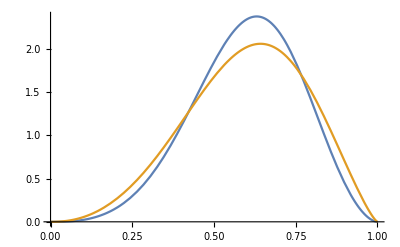

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1},WorkingPrecision->100]
```

```mathematica
(*27 moments*)
```

```mathematica
mnum:=27
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

6.90070405586674176716418351445109689333194966513516032950584490214980712136355421677075306473186410458389454264323950799207974840887771638195261234714063115×10^-6-0.00519132325040981374042302439527343272833247787227240010764730586503923071416061453253908756186054102359519651789856418409694429789370703953321858901570617462 x+1.05213206173190326679916647107920476544969122333355922788931742039175386329625990607864046479257129522005089272452406533046045173851735524514617261469491412 x^2-37.823768738499153903206893370894907592539369235803285088959072338252763986638428640951922501779939702966267944766568928380305395043300783562620687796175363 x^3+2803.59905001638330284440082634281421968484444074442411570379830880477314961321118217539675944310229876750383752041893698176206299003342295262777862070762407 x^4-83051.8421863418109330738651989952373504434750278320935189342415006468357939589509552457305583159763258320102704623323943551472623933444758979117443769722087 x^5+1.63579369441904130257734233735563246284395182904546084806477004621413932244803670379084891940121691188796128321746157859795528937568769201044054882891761164×10^6 x^6-2.30144260731345251267323563587778167794903411953401186481025881355489460868797146120598449859050919937685397939154005210634775694048385634832762505949014432×10^7 x^7+2.4151278302231364592055022371367111281192896908392724647908734056823350201688429189527368102413991507775719237810461721481829767627431928144813765972818867×10^8 x^8-1.94749765079910928426928498233886236149808625738184049758806818051614332587462127890894925999175063818696732380013471880686639025755381893398099331591178102×10^9 x^9+1.23333624933235232207745953058857909875902102419471605969576348761802243886995785024768318567264655829274170808648668015213453377119913317117455817709821029×10^10 x^10-6.23515361254356976262807450043824193709848677065482759049305618914708380448183435762771495066334133493750699568549753328236370767770292719469845428651784063×10^10 x^11+2.5473463069430802030372885619327819838868189745453946814203210370954871876280871100852538200649230866221330241490173524572896451665191597746332583686796671×10^11 x^12-8.48598679567609783151974312177605900339022256697611241847088296651053195548506820319793214072096500592777245767872379981312036009812685677744989540469564571×10^11 x^13+2.31950254908661130734576707581777135775897431270645309672524323990359477883110673695724273662084563633231125824906563247840483845163626102079873845329355598×10^12 x^14-5.22157648877649037692386319743286097017355863507476675749896379612724528821599141356342948505619231697019789601934980776157988785763442825945310093439723081×10^12 x^15+9.69481240805129855467967658750182821639761284100496930812528014627504404532373734301083921424189061859539262186486286630511387904672462887242410017572302289×10^12 x^16-1.48314380866487049591362368128639801028175303992944299592881018857592004640536565281439152806576697318564512025359126694677318841629606961342431899986322277×10^13 x^17+1.86279598465837967767563922596753130684336802656517816752447374180412073384558666008897060878271371117616383221932796766298148967472239713282921402497540778×10^13 x^18-1.90795718441337543586085233738990763463405127766674807496004503348189174268443451850111364889833270333269622899724506120191332842669102315190655979228346446×10^13 x^19+1.57675280257356089634351231874675716600498227283960063449750728778895995275618359385659327039299311657694787239358024866836041054225364805330011636062264495×10^13 x^20-1.03461125932043345979569039730135885391809506200934341121439192688270251735107036783920999319863250572774209524668887582784715008404219928367667806755772059×10^13 x^21+5.26212892278795137512140144691283147649766247933161510026632053338216199513298789527935263982848077564968561203617861290060410785175501589517988030641621004×10^12 x^22-1.99896789955910526627132444307592079703670563558285409406984135300644742327494056997417173111345854399970654399407711545515651278335912319292713970504753755×10^12 x^23+5.33523230901060668974813413906666141291483201436738119519184822360545005531326795780078447605884457765299232734464266461230050050386396622772019145607257438×10^11 x^24-8.92063014830886580487119681095532720175392884672215496627957460851463385117357747395852572596684580305713526765090749622787137174041686378308178095623780985×10^10 x^25+7.02789694973987005975947106534198158088288489890668502402297221097015256950923339591822364271457618120577181254503539030809158083659907099624038878851471817×10^9 x^26

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.0000399874409265296289817401788410890896964294799263039485390424661841746857166424908903315067753850307605754518582842685129719130672950835760572555767945295046728-0.0305327836517647397869970629592682897531161137743736073938599645231801374993868510558080280682705449415131132719587762153213773907174150127856478618764057705352 x+7.38736206923531658734010255888272861730855655604302055664914134203410894936241351713681789899865263771675585374186620250083337584575088603022585927174654548134 x^2-318.860085351070006287788978301853259131935760954322605440457285288360621355472871353024747465858828770632666368766087581803461795290463359170165138690303116839 x^3+16368.6431531244634146593942872300274937206675488582411924808448226893390431393942132031188281872208335499928667868175137570984301541621891061255103640899218467 x^4-478756.015653226759335121715120148514082204837961329020161940976779897307074917314495579611891023776589872591416126784244941940106666474688157572687909578042145 x^5+9.39045552130756192979150247396396963118497601450273753689237382236387820642058367783630876994866609127842601993501987747686327467749197268694067730013153071953×10^6 x^6-1.31894459282623633614528286538820590116656895516963034313189206037704257922715097248467306124664998720091402461702067461469099029267295961115727965449558850453×10^8 x^7+1.38275983719526203446898229239522809190190476409665734890463464416666202396426383260573011062996764921555133696629099687233198795954920198923267964988293185195×10^9 x^8-1.11425523538108073791541634501345563849941598782876817532475866822511854307437409737022115736954914263150738135006550646664736796020316989586057125957554961948×10^10 x^9+7.05252516142096700996265152167212983311526620197039886804585419462532199963941169382408613513887892547343418589682925597010025060483407659461798816762455889314×10^10 x^10-3.56360758033223651844004122594329094559941792646866931984405583931589005857126385358218206955444734866485861792190225852424626028774035216696433627422394580454×10^11 x^11+1.45518863789408382592038579652627740093664596325742428490860028341210684100180167959427717692493272007042703120081326758914583164412716954371047629525715232398×10^12 x^12-4.84532221775859075418323196713857151237643040558810983914835992443393761608929745724310422373704047653415356868359196467175995762974055419086061812884948923175×10^12 x^13+1.32372957233832414350247998009084242561132450126873150687105372539718837075353907084684795542817454691277436773627681483876263255409977877597288192074224885517×10^13 x^14-2.9783917134473162130648483173186057562153677867781733854305371262675253608655273292590735637466438814711259354426083601637984134042293545654470843854014897553×10^13 x^15+5.52693987281976038524630469268544532659040842234507534859633552024006219132187142786395916172636773582579872467263889086848890086778347170287336277408866386579×10^13 x^16-8.45048835408117100993936841641104047757575984189314370993610866984395984574411327926647375892633955403177789573081512545253916965436063521908828551223860712635×10^13 x^17+1.06072904447469365792887038519384995241015345291944871403072438818576152646579726738192490661831851631854422700660155253670446742208437037068769629364712394231×10^14 x^18-1.08576468472251470458022923387172240966469428057309762304213800836900997362004475291920856825319804261207356083418182044204349318932391418508372918773871617131×10^14 x^19+8.9669792460638866070983802588692790308836069374354075539454857500758968084276920634442544525624424917454862820580423600749331535340797770680332609729104000171×10^13 x^20-5.87980900794163813453717089959210939595936720170108197931641673161258455541737472715867803692187675649118432659050714848151344621194967543599741116938859378482×10^13 x^21+2.98840532783624655862459647971556676860896173920280255484466579944795390853350763946999882153250265842591545353497119101847566473741822880079811699455792457668×10^13 x^22-1.13439656149529991267504536897132620165970012426557977490872464239007932853948582403061300564050341042826889903615326589856084144563440257195102685551328089544×10^13 x^23+3.02540160456750738627889835171330003672293282709209432355950981925195120838021923348402160684728028211392170839362250057379847523141359250677978564563314350648×10^12 x^24-5.05458890034008402694020279309437261902607768427105500003819372716225324580553106289657863122615315998485643604771836829383091822512515978084011688623454270099×10^11 x^25+3.9789334823454149139115997550327303786282775938276545547253192712002109575098978330098010667908008125494166108134120655513249272947273873830134981860518268426×10^10 x^26

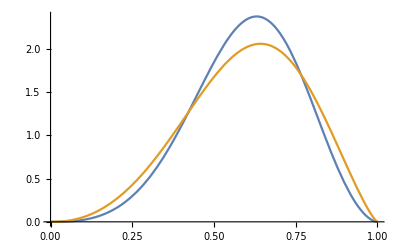

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1},WorkingPrecision->100]
```

#### μ=1000 GeV

```mathematica
(* Specify the final scale mu1: E.g., if Subscript[μ, 1]=91.2 GeV, then write it as 912/10 in order to ensure the working precision you set can be definitely achieved. *)
```

```mathematica
mu1=1000;
```

```mathematica
(* evolving... *)
(* Fewer steps such as 100 and 1000 steps are okay. *)
```

```mathematica
TmulistNLO[mu1]=evoNLO[initialT,μ0,mu1,30000,200]
```

{{0.6,0.379022734323381968487667190397035283797773046632798195988942815772681066145258226935350471381608114752673118380030478828652295220393540396501699090798975822756155172791821704377386310265768438175767,0.24952951771727837701640682358609976321881963741575546907685307883340951485108005666633752711810580105623450929115703299625071171232588601363403371993275565487280351596024401297135954197187073333496,0.17003346269987894524321493952598844593888410728424802644463138288273344079748246904616345784755309661792719041380113754641092445607699043113998077526341873972339474859063699539741091608166722115263,0.1193240052892259305340049998393921331231027116040299668753121868395092053317595114661769921387734208513303358434731558220536782150199499414941611594840649530215607754831617906062592001855977449766,0.085907908817341579615355330263304846424429036852434013976297677273796455317008452656336839874053967306296901831833400390236410190121903420379857112788993229419215736245066255671824440302713406088,0.063258610252210342206491835767739972014665685013106659800434908223781081391734866052025816843896602186127135370695169922585357143077638250344688161978960891802945374145210520449630711411807508938,0.04752212503468635781529752152420699290495230163206815894640154499203056461198319848104092260729902460915926534843947253724775119960760889940820595492849327993617447083510774018569487775440093029,0.0363452144917260052089269573284939305716321764520063275490579883510552510209220060662339051502614565192773487246592627280427058987429766489604458955815357149612575488926363314371210212952481663,0.028248471862671822636863973126476520218642069232469563262330735956128658771718649106656757899949531969250737944313863000510457948196233576901639799660703056686993194025947177966787962289093109,0.02227754748238564213366337507523047521369397885012810405511320861470935315068769058852458801291547378074389983961647282465746801934467832054695739274768454807387789031709265838668486250536015,0.0178024431173940142528845663978146571842464813912169294163902419817648689128025844612920310721499716768233615688017263239609663855750759760207887576370181412268795782140029061053783843378877,0.014398537063319594819102978995034273686395438531949558755648041388344109971094901314906828895041835374829568371815292824894201190157856630318438348017642400041033391749051824074456443664602,0.01177417371979485245870037460923517675578153337981289551631632929761230860914559125547964982873724112690485928088693490764556551035771728232280453228074926878637001493142037298660503688948,0.00972553726691266627325424867450307755486754725283338353312817766207237931411672665194910492957522326221321599369641742772535986220825738732221370670603907863264918334714059515516150991392,0.0081079192507329264608434893184586830994458836868247215029520882355452412976672482676243791383379898123829987948711906022498929189082076417967859110407516107276273652054866950234152513832,0.00681706301571257256092257310001433868518030390651261419385849126873614070552344169445716819567335056312251695652138465911313570933165198646836136671565054283362169001807038609129598989,0.0057768315910462061283101945880147182054452489980665615565764729812851433057760687982845699581543055466448875372345586672180631672279266226828270271947260962478990105815786500211804745,0.00493091965767554606485626239432044510495079417801703803589843938748181334128656389097883993839905454136363367431430050410416825044368430189086047551760128777531272720755240721585744,0.0042371974324695762597333081662576881285942829443467883153558487865597889385479879938987829265576505483041222179933167197748239156574290598134373005081712508954795169069466447569588,0.003663795340000898590097047011289617925505615204029008741775986658738667795318345934815496672202186523162036686983611457663975449649640133627663054001983419030477107435546317147587,0.003186357490731249042128223153494861313150809567927402300967758888888016604671501968727636359520455668086168798735917471943207919279590883036022361558607061262499159321021012225174,0.0027860909903175432443188716379317311365923580171578763338318029742107451131626672215756270189418432590845074173391284810508606543893996086042730420305401922416043047694241842487,0.002448364266429138350751751625867381730511563495094789752006736096201577283923746029644808059810210931737402834273984366196033295843487576149870934229383195146321751804745522131,0.00216168882348152081454613693932393443238884297386061296353943670100365767583376979151548025772505665287872233567259261750644826768098891121743397333885090062860553095286436604,0.0019169718873425867398753925997713919020983835560338471811195406344117467439031887330295077991011816489988506831252025402486508153162462341560787492071302276959045549583566866,0.00170696252403865158468029139557245239487706867105319039700769735056829329369011216109203397092289301286988899251915025812063794674225266033229411332711355502792704681795449,0.001525837365439896428197088956857655729229161881206650238512664302895488771173860823083103121034855314396047544172436235142634016062777622183845838740698799280605867929524},{0.6,0.3874635543639959985777007369750862072533759470768088275614909566142783727086551120101039309482804270804929497550506637687406560511973280795814587997244641467026544511191362181662467256179396956844306,0.264143787818683291991434149957770724834790310433774572969307836602849018831731602092651359674610045785470940974335424148996225519857177462990539788263839686348048791041524597831045919450215149551722,0.187842134796491783356449920828681824507053223911727451853759373629820606176326874405584911891586080520235381191044692676916576286651462717005232111378356440141192108337783405909405373104773667834439,0.13821888897598596304941548168521156363997747911285113589527181140400958649116722670175939703341974604173981281054030700977972658825264591591416606219957068189951998930442690146460152740408870256514,0.1046203741635986006415359426208454638129143307912436640244304085799631793868789546780352309381757095832621173628970075828345116467508904178488388246278878693205251053036905315075855244108431104217,0.08109861007865066687156352523390272353303205363338419044327544536300719616873421651959617494321047776381119228470768169967229319296137227821354439882116933621750180719323831759323629392194114345525,0.0641585997561911990116738244461914105098698150968228241740735119185325313724362339845670326708330904308375688442582130721863909942326009796978441691674463500369796676536594770956870138863363384483,0.051658061965599007229744072557995080362825105156895166029825284523711210562096831921372990765710506364272674267626102898073146774415303894069525938901408328111403675027560986000065897588875484398,0.04223609945002108034563816227999382966276081517997514855828685853586104415016455249814139948471100072137641478168503027579396196949899101382785636571079867683072815181834463611454859680033327099,0.0350011944594744049046413092422931031218722303945423407691183145980015557434107270952799386051207124770584318191134361905904848448934476375423059454363327407539674344924291161324457182691887257,0.029353434765404273572032941246678532143903290662917534955678305052989209875334110531662200413156224633130688509527564387516598482766980215047368957488078353543778788368526083988580040703666156,0.02487946343658550157153983773449170257939423976027631004607106978820277551139202196168308672895801265451452130163700132996356070740051578004904255833957653831488348231945064496174516552062949,0.0212884012245250709086644267172932958231708961011449444023823545321052695218190542896427742910033531354942985435452308272167168322689157086447419812584239268689394363875709928630337017074803,0.018371652367326506459020574643246702792687494125370563627053340326361457073663027392784219247548720752317048410871427441420754179193250480135308300945682539950711833249542682618762217021937,0.01597705613657440546941604492355519044061828986340803165370551552832815311085503379844522268130682287844337711172984198761974776546739459501807450769175828748458374081517314990585541450747,0.0139918882745859804544485835498907692599550044332512803403971084989028491966241400252733741482578205047380660293614817706538766938598041283225000466752085857343464678918198636602161027957,0.012331454228901338605027796858256531753322413118368138372188381829410586216894551160369584030424997522864822218113734107484242368156452808935207939949777500776065758450374632782440651603,0.01093129285225482625850897525716702572190893569115192620123716069648897170531987241914185717540064873613344082877146413537142737163724080435438970418470715813516639634521328665847859323,0.00974175760645177028618078545461199032164509801959924188530171763867904378588809652699243419102360094738839254174264570747530047423908713502864056092808140563210459460514649685395605389,0.008724191779720303193745237217347027023508065640318090617824140512999163572149771021362248553056817424682692185597700628517230218509450381945137963576265538472743392006565078585856507,0.0078481902243622723794181426203869382042975694638756628866540381202991641840130823501005790528763733316947701905491548740280321440674865366721513157142156884816072834860543320426011,0.007089613063484447427121851801647714494913124003212450941395099922832753688339644247947628379175750878220914850962912815689428692898355031585990540968952693653357787415917993649287,0.006429127216748928728157281498228404078456228706703194637792262185400237662218751691670226387192132887877223139693891437951216021918106737502509789918859033747693424839880819941318,0.00585112329183469081248506210821732093514819626890812412403098436548280618652263977444576747902858682038169943095780159125919184156940660459349882950798528468630428895131902213491,0.0053429026955183214342865710312392449963665944143575218494866304334000983088937898961233731399715185453531600589280140975075769691093919420933145830915607455361928611693196211517,0.00489406149710989490060992729896322660044039001550422712494400835181657224251999315543739015331556515562052033841213807590806297202232048100206843739337069871767767789811919874,0.0044960190844354330598946094956328700170121804496685006496084754772009215221392119325967888260404008009762799842517160561445397081593210895123759546063810358358070646087098499}}

```mathematica
mnum:=15
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.00226223862342079014005990196387743464569738928465504424048500749940827799902857709665701262159389348664844818313288391118978641081535705709170257408001396683234831845361700745435-0.537756633845705696455616229158617320200879128533436006972757791789307750438396547836609607781433258018322453067878179541518368639374049375823509089422897196539116832711997748358 x+31.5129151971363231396460926662836082974949771963061244540820301842734530469114685476542389208327637222477948941053385892170666205324528018347680202974303167203531535954940658316 x^2-797.210594273973192773518300128282759810996484557940997668162294831086655828466200476948035931442991667691851088688812302329110434996491475039282789466523090598008451947422436795 x^3+11108.4998477703937247679656883169585465340009755197425353895785017554017306240056704724773198313446479353097100895392961382551233012122139513721777689539455210975698549180361997 x^4-93532.8616916956991456450205899208330888554010690849958355194066150901120065572893145078011463005473173615772566586403600969426417982812754943142465802526236873126140759862172717 x^5+515041.840584333472744808849943937551066886709913047985377217426329896917265102831374125767025255260779601596243391700334172564882752732096069447694572295067359341754129150580701 x^6-1.92580033212448186691340019208553710675068313761914272435747184910294646522345492780352690842298886736837680569130735615501761245941499719246254410791995615907435279309892281185×10^6 x^7+4.99504123406899641311172709285691245115517213180628503579625533040399963885824720046040716236300896224076064537457558454477905843489996254902756107753396120262213862291255260208×10^6 x^8-9.04389879175735016461903881504299155549594725028454098899207716559497716593546074399976180723588200037299423418429555179633075631155785096831537581715739849725209447858313512103×10^6 x^9+1.13467085624104153556831190165700899042649092701232728052290053177778507522935286832712146221768928957891346230410580665206596838364026242798180853638076715908966364188304497408×10^7 x^10-9.63922191776455538265601212904602187095870145810142940447002833852018411456161391525936337513200964078672198632399804919111868611622339103341057446063715521641178307187486974837×10^6 x^11+5.2805353609881246338493504492705192194874971202019936322535640576055087031269321655719494649647623417435438439750239389997654300604124027939086892931585249583031702680380932726×10^6 x^12-1.68161603733702957347351122485485098977935414529531436797377377082792053033552532419090325102791790886930311386968549161906411090288795223030189235841112740470486242418948213741×10^6 x^13+236400.675003710631726963840916341688757431277236723416371031707565322591832646960901669466997721942222718379519692580318945696990517207249006532762251016087757135855310968160313 x^14

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.000349131207820572536739903138869254531655770234789627194578023763127224452733178439180613712494773956000168813283132826870695388235615627431205002369537726030400569443100880865527-0.08377835397055770958405708183395825955871452423306516586324121872872934865308564513798227811990659501273579530274106789398172790842235232896920357096780405136494376905054940615594 x+5.5864269255405602775349227459853371895158908619483112151291207345343525281480475969304974526647094204659889380013215536900800744472065568172660513512620235000811066094254398602 x^2-79.87420770516090107052639555810685894375523830207036909412724399043082951419949554145586900131802378367870128060735876652843889468495329256368367549907503405617978834081985559011 x^3+1362.622441901529304443521604955102688097148146445947568707912586962772262998977858590830932352769571665434870591359072603858409008549622014294312194008358622619930968427660233308 x^4-11823.05769513883678844669174277406420524398902468184018630377754565387353160172753937993876775428874181529836010023994172511873326323303285521734618987493843506621956803140706342 x^5+65976.25750950426834831727191281842298784903595537235245886531289324308912778169496579335639641284417234911771569895729727660745181352528958590700716949764921976569449408070438287 x^6-249243.672132874187378899342387925844493585258066112682166647458487237701302219904264533517779986038952853268541018474172658091827721353003314807549099457518894074908006595183111 x^7+653857.9605372104556205430276102091469475542166772117612637398161335596826643116471311785062204159413133000864564055829434728323025530780999527073398621469050531186175190269827881 x^8-1.200497660176361232917804238960688368999664069497773233846003549501744225456559341088147449924411416845162905658971424331660726864999721243758020210472281276803935993223622223204×10^6 x^9+1.529994390833252541072374700603694072512476732739679839245395902249955816855644930152708901509164883027211674373286995439513055459282387188044227352557469361920624693455556239523×10^6 x^10-1.321308624062603880606968151259180411665531767759653247002276059806002131879953697381567823637549688316923977677135477005960365205056209323583054358577630464062556432176439719314×10^6 x^11+736274.5995925550527214356269194766348985925374480379960029308881763574074123155084905141004782283706248697762685202117329435175350727913577406420213392004273350509806009228341311 x^12-238769.5131240924789313166629872196160931248279229215711974168407237460793984652293166789812780422789754810882277257094157430173952845756860223754281907156841684951827335444627484 x^13+34251.06545665627345440004694946335165127502277506608584855485878437750094267589751111865312181524610659136553730630701875836928190794733232990541604343585252302361823297463155335 x^14

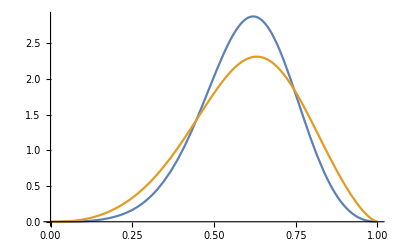

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1}]
```

```mathematica
mnum:=25
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

-2.540551111615130785127453578046163251171144217027451623720404756570855874477330167342341098524842918214301003013615831515876309691218660172372526272740582713×10^-6+0.001778885409365088312194960332744865776575059049275922628494481126885306535223234532328949133461570403961615986426816897224746645148589171519427317513877216213 x-0.3103888003341718576561125428975821502948051960837031756193471767059563831500993847939815858381329549540397035082401719465274926154270253567960476557296025029 x^2+27.22301095984717713631350367267852879764819077487699771933840102015808538132939634501005476634964783342906045953394375102704881783828747523295384500318727471 x^3-915.2068038759139679160947672605921278960484781186714435982173743098922240535952873100523537308750774727811803742923699252167180030702039830664536082748867871 x^4+24767.54784584713862680697250391593000533658827813385467874576376951710733904677108130223929526310258592283206950487294742023159058954908857270723453712027683 x^5-443740.8978056001993048311296218030302881681459882461448110903429838129284702553474860284755329756292231619299313385909692795151128348920727247500409222465566 x^6+5.674200187365728974581082278515755045348703588008492394854430771914162126354740848201700830942002664869104787669668947680417665796079239084148691285177638764×10^6 x^7-5.379404998500258528378640099993616922754782634653944002943870210308985919918826032999035738244065186561335078869141961319064255548000169935105673344507075722×10^7 x^8+3.887634333189097483216696720439827126864363881713561173085379445157854423636390800112263881456074964191206082316771039656774383877129194579042273958338967247×10^8 x^9-2.185531664219469644561571842610317516271438060591117639530943363019625920377294066445968695072679094693420997879693494376830193902365443216001248817512355532×10^9 x^10+9.700869328232682218150796761966883702191092896882349018094165718970602183810406934238774891128709218047355507452697104188200133366573200622384875695527091299×10^9 x^11-3.436329586273506043789805122745714307519698974719194448973836531026227697196129324527392782627674319707168917191859800204886343305983340417627319395933070587×10^10 x^12+9.784970719146990165763178859740152056081420690231347885845899656646155478636001662282799336546117811791275354518481481229428396355261567767812637951035976021×10^10 x^13-2.249221903630681770135548285312214543885424740408301607168986703040077961550881612097236790591996794175068416364828555796281282566802666929789670131727240983×10^11 x^14+4.179105753369884827554132238605993183984047828479879820736101168444893062458225086350516896070797771038858803777903905206670741153129942356421071133666763172×10^11 x^15-6.265929173234024011852885561099055203600186490263709542587541632093562204437475081838821620264086367120365925712232469561200431594036508965728009350790882773×10^11 x^16+7.543098305173188885023400716982402786321921358307912023961175322384061860608950643585244982032196271944776886135707142967859890491380162374275143077240280999×10^11 x^17-7.224177019160672551592139905828038103924918767614807883903277488672403174152647746284774239226834837402941573288717539497397367912311034198175668847599236377×10^11 x^18+5.423753514290398174346094020991941243072984530241763645413986873276284380473751220615867869054897717307392323678679858053593830962685122508869915644717361719×10^11 x^19-3.119952829378495382279935268687423807238560182075231367955490093789384747547900402016718613108540982865555655578063898701331202931319959266243828304979581867×10^11 x^20+1.326417247674781275477059082031499472949135378198116357721863773238808001259835392541104492606105539952079077042147302394179033985119965236140027463442039429×10^11 x^21-3.924189894046931375752860804966638883168872516087749621891570931851086861454829087027963469542230619333002061351839438224501867444541653513414171125704753568×10^10 x^22+7.20969991235813089269880511210704499493778286568137058368914943331526692387772144411321220090321984986466389830256382957977470494442882554975916710707179389×10^9 x^23-6.191631969537239262556322975193540248330043316423975022215611927923023791674688702757976663371354414312369563535087281105275073913451968042583132691367378107×10^8 x^24

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.00002482590077042513258263767751726575845096165507038748650108715953371897614145973030196096869115934272375038180337242355813908017646375562832647305287220425364901-0.01614334336820722093423330162304125574006836926641087599199070321941965316162159326117486340817014608311568542261737577284613259146175741935127198482325193902974 x+2.979029262539704389828802984102693143885028162403595938881043110507271253879184395061043102913104769849812593809429453395273665194154511094439922429425297847789 x^2-106.1224542806399938079958848518629850589457536420392268590499299597334964478375703302753381378856203966093836616435536192771308797086386782046392942301273633473 x^3+5326.355707900263353179720763010462877892296955645023633423786851924046281072517194009167500717216942016856408225213962723992548672694020171228261146637330030302 x^4-134286.4605492768108232660770608101513920324999138908484284219910750706668259776936239577455725496152760770441429859346538339149374142201173843725063003217687637 x^5+2.246172762116844445634498332000642451019570738783999936767015692180486092972904841206191686673333300722638042814122280469010727655512082605333184169219775037144×10^6 x^6-2.67543839240413648953669239334996149915637359120059901908307049396227429849817750872235195224175523146975012161907702788063731372347497702507765584837105560685×10^7 x^7+2.367013754030331055255491225043343469315061822326930937025495609336767340514805766606966531088006125359660107225702313556521273113709691304180049629985114062696×10^8 x^8-1.601180505525368686007265921291795438088389813725057082026703709966301688128446386674376665208427335903239439717431246607974903562773873215668343153498266070208×10^9 x^9+8.456680239008222322939255611506230382734693746802843838657602921182035942968303978308261147456111606195152746228572664000379606480556859557093403999415249127388×10^9 x^10-3.540950776650931508003545811160353179186170154462452517106306834166481760414448286271820262519047337289006066456573892038823821361182928083740142678003272153758×10^10 x^11+1.188423709584865153567347778610269976937758784016712085221933114017155300940270712065205130288506887810423405573762426836328004947300740920641366302273191311041×10^11 x^12-3.22099886392269654632725880689500781546178132936032919253437370874742694000356584874794121639162961364215824240302632067957540523206328658953716831126676081651×10^11 x^13+7.080440889701830185947110466163020038896860305518458592245737489063793962181189865084255745552434762824031200211967246191781069901003101154716150904498579975552×10^11 x^14-1.264079974019592183137419681849395822211040036160867997922384297836432674995892030597178025362263028555410576694102715819830220621849732627673169798133741309744×10^12 x^15+1.829773227337016041393657512406317893802909880585802323838218994771509726238845080076719264442608668965142270380799875553509521096577721191291377434638884851731×10^12 x^16-2.136478879082184599684556276191829241236579371528875790098652541187463391075831154193730333297895046712820158964834590858342960001955744289037228783470676053388×10^12 x^17+1.993525185194049843949715122474551908316528396234787632801762205176434450326657673399463422114057294830801391890275901631780864531763080235879940178058586173502×10^12 x^18-1.464451542826696646007424070358559176858983970380990856825557322583714309759501157885398045119962601396213244730478412472725212357505511887413113128124703150822×10^12 x^19+8.275952181391448916644747406359696959081374784872658245782419288297773639612799581067905341186869670445449633688784330642687794842144715124602763285444742137806×10^11 x^20-3.469660597662279320445858306581971796692828236800694106925201129560057491268307484902116684187102568624443769048050228355853504401252390861883954207448021451037×10^11 x^21+1.015833420331037960855730920389914425624669920814921379871282341077368034920347027559315323248949057419186160384416914379968586954528056592035022546667731774248×10^11 x^22-1.852986049644689721517663262827833666600734144019837404293386901158091371434912309702346662724975058288425291425778964257466859387603413551303311377690261647982×10^10 x^23+1.584713883483151746699661457252025718858355698606322477278468686511657347232500209135673889376299507801985949234519985684120461907441561874866830876362714801667×10^9 x^24

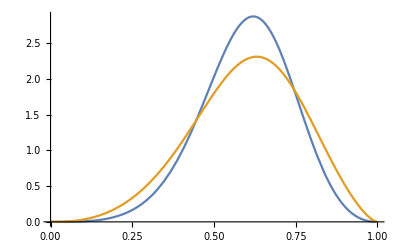

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1},WorkingPrecision->100]
```

```mathematica
mnum:=27
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

1.49266491062929384382146615091789052480158836675441681355142673165190390992973041731651355769584348725327599760927735272703940945614417487654874559957159×10^-6-0.00114445740730334482944118167671797823655146488123599012944102300027076618164470366848881845742178755774535967195307937880453468576377274337237514257357256 x+0.216150282553891588098737367214553269641307160969150738202101289190206836386594321787056131176625555418350734848918281220844345905759705510981588534950686 x^2-14.572705928081373178462026918168526014083719687232419328010551218169105836947509174121039329390646064673351706215025510664867631829837540051795495703202 x^3+930.570439652216762425385608875574216577627159939851253636272927047846629092359766329592549340200269662380129485312730376040739951062488218530333756929471 x^4-26691.2143914283978862969811643169268098219313522816248037754347562805138117850073817912859798226952932570753820672482275311235407064020740999722514312531 x^5+536176.947048868760587405796478546145008332231035974960813680667164349841326281697654954211856496023351518713573544316640974185041732394386894851746785365 x^6-7.76958416204212257814830904709170103979590625012064772736315199103312787134473469671507686990556361759108082008656450829960382015591365640526518022485844×10^6 x^7+8.42306121165642330463964260688545289691409570786530659286842186557763477315156901989582363071742630090297347433717525074425830273584532578320972663745614×10^7 x^8-7.01822451074639605747325116581285932205496920638368802150894422852531933995618465250747267099308099153658806523154633028814574455996703554657443765152527×10^8 x^9+4.58746499491999714703813593847118863678920367270762135640779805988143226672422423505900657936201709725814377033916423807893552884706364000278218151744573×10^9 x^10-2.38928183439581723079451075705072847982405223164024284971956153532386682234829949187520962236927394098962230275916399103698088434051679884634593585436386×10^10 x^11+1.00323149227843964324575911550232806665536727539041847168713978453248789783718426236480744103267855435620333781341300099066092915750719269305077362238037×10^11 x^12-3.4253680451575742208629219101059569952625098539934386883947712862624071442718263907253850930527042535923714744715072104166821691817541419290998334340548×10^11 x^13+9.56671465282668469697825124169370491438361057617595446828087504690055665275868066250588450066150659909296887816708144351690777668679836479980766514101064×10^11 x^14-2.19334114251405382878408591951221648764245651688711474309407385730487479051247642716784940169171108061793248307839198003844066113045624983959102391436659×10^12 x^15+4.13316648482381926282272913463469210817096614694278047892601763177152199668339424356247906655056641740561211422400981623552922964279969893304943566377919×10^12 x^16-6.39474079451504097277134337985938710105859267074067243826660181801726402105231289784616832564214898450254252526208960790025759352455627083317296794445549×10^12 x^17+8.09354245108041955184879533373148278356802140345038795841034969383746621144627796432732338881786072980766862150078535164850472057889628152152487764813984×10^12 x^18-8.32371143350887667814653214858140232216357948952921913052211693458975060262678796351594362371107326624351982499107592366735959672468191209912639831493904×10^12 x^19+6.88260621106616633039368894537031546056790338598241267204819228595050512150807042834042334069644084166003463180031157039750629901073940689628070726968533×10^12 x^20-4.50313165841610602021784422475724073468378458077171683504343737459927233059186143123332791074056139735810860663754185784185531472315113187948849032624365×10^12 x^21+2.27618929721103186251616964961639536538740969917855987182304974600487249072222668075361728475534586040805523138217301464610156021288811093351070000487176×10^12 x^22-8.56616814103991467876001070599163033514591727215638080085773691642978958790109702424943354290485061199696398873382532259037975002264009548993161416551753×10^11 x^23+2.25819453751713896121239501489710427268465582678541284396284677025887346770408747016440572665398493445477161017754812547167480981001318199029502497544318×10^11 x^24-3.7187441434572696465476531220370001808049759514938233971852263552695473511209902609096095374423713100953610621870854717803737936574641053039634202294237×10^10 x^25+2.87778093494864979273823356919222658146118195343284174680047334099188219095098837942632566018381065766286354432263798758833242642800185517757278168309819×10^9 x^26

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.0000185169659326298074430212104806460288299198233933459822765409759671084146749487820845941471189671466302835712429793812716374397742353872222740361262904307419-0.0140121061761106522275948331605842583134200218844118711868070682678447116323842432753218362661587718332943833075584651418107340451179766256670292634375756773 x+2.979428451828614166640068355225852168911557869537441411546672204711828287053815192731766613332090729897349544653883414253501284687329619146439746361575372883 x^2-133.035655168200619515456216233212900372010033587214277989097675084124943336973045937518191016464172644789974970824285725151810407954426147724737957557392799 x^3+7569.00128870735068958469388008115907521978649433537718014096944110946530685928667654663497937120677073427985963298713988658411739776349744594170190874228552 x^4-223078.823979086175563103189940398261313131054263079113173915185887411784513681074622384906709960652555621852611997503688898371211286987117908897594614641443 x^5+4.38685757255097964265887308172286206189515828197553406185956993648303747310090670301925370683361773810314399340796977912642068131789565400668864491009209751×10^6 x^6-6.17024030654297867511931448842072621296706363123575173227482870772915436215427666593103706974147021459583658436485438702826744993755010894548136889508978976×10^7 x^7+6.47543844609264992480637411078521145590932468160021257742941010193073834209759307856520355229003396177421897216342945590539674279629682787266010776962015177×10^8 x^8-5.22258520666912839054212999645733476473998805546477345183769180429294296562366103886353381200889009390600647406727164566054022289522312742334493258082350448×10^9 x^9+3.308174473363658264445650237740770628793272668059469362043698564696328195360140560137809009684450217516885249106051339278862896171920570178836669014795962785×10^10 x^10-1.672838557504099583114898557637619108206863002689043186090269567980592838687538499188650090399084896640522005482237777958519687493040059934810181074229588968×10^11 x^11+6.835750993833545803724605987137593249428418039287281712410693897304914735811996011909164411177106561235856528476790657543689170217115360061292601530225870146×10^11 x^12-2.277592561138246048819536445983548828051032415736111312968185049687477114120428274433115146296178381574052392033784090863013578977739512931235427241299645409×10^12 x^13+6.226187648288196446861688103387750600146895344929889628242063163719574784974370697513739950945004334517480432915415569503320867274968859285092621281950589404×10^12 x^14-1.401703223694695253174087056239715625927079437473559901116296963061157543844159895966400225440911405856099606549125849906326478427050439220258045958437146934×10^13 x^15+2.602498058914160346843940686930362325115562638470355829641236282754850080407483207409896789437668828613361515677042263021906195071508674265809483302111229749×10^13 x^16-3.981047830380588003490639175296842637111965531001093536803864248585248040997133338022512225472644660883774455074234362931678018181797021173527528374138174076×10^13 x^17+4.999276939394951672347271258059068131165408215542994679133996601762855614601205629063729546349965347312667322051788285016947039087787521462826077543682557675×10^13 x^18-5.119199770580612866255968213453250573274361963275230971972895449250806600700853323406764390031648407711241207750930987581777734888479629018644671492523525515×10^13 x^19+4.229144304348267713489833965323405997958386274076946666593145231408742315958281989167186919131058430065042330257012899576999033578023128762826377385780187675×10^13 x^20-2.773871626626520808956717118554694673220323924899383065689414994918993463299534077472538691137327575664368933594020477806350194273308358791301056613627339109×10^13 x^21+1.410124084165484118834564031471416143541541955932704482126725131354963038426925492467237692737805325210902836650542223794666972812819313224633837826176922394×10^13 x^22-5.353734968108125098985505814950045644315502874989513829975275480511048574936926687114473232991705539113699361848602567314590745149645947113033081749481972046×10^12 x^23+1.428007656467400487421269339298669218834845376193422132792978845694684188903911554891739569911804655549003430744651865828066200301827523044712270815373471574×10^12 x^24-2.386011330660433541769071886311146700680947789384106781837868381730536139315487136343873812672951292348428453863811389146216090894138212945925672890811178331×10^11 x^25+1.878358633321250986233734418518895273834203160426063929374281422672304846673885755103175310313770384120971366846193879765912182784979572063385894522600238267×10^10 x^26

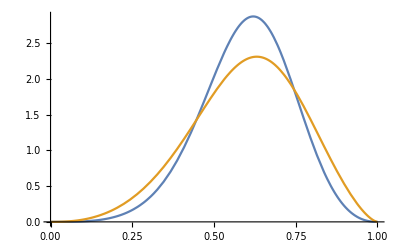

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1},WorkingPrecision->100]
```

### Plots

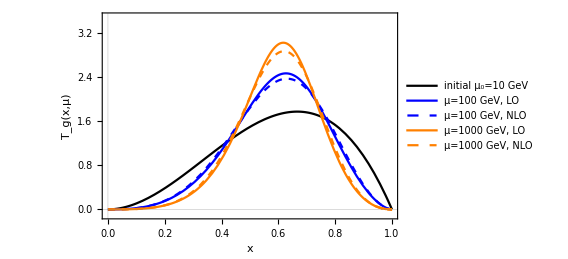

```mathematica
plotT[g]=Plot[{trackfunction["LO","g",μ0],poly["LO",g,100,25],poly["NLO",g,100,25],poly["LO",g,1000,25],poly["NLO",g,1000,25]},{x,0,1},PlotRange->{{0,1},{-0.1,3.5}},PlotStyle->{{Black},{Blue},{Blue,Dashed},{Orange},{Orange,Dashed}},PlotTheme->"Scientific",FrameLabel->{{"T_g(x,μ)",None},{HoldForm[x],None}},LabelStyle->{FontFamily-> "Times",FontSize-> 14,Black},PlotLegends->Placed[{"initial μ_0=10 GeV","μ=100 GeV, LO","μ=100 GeV, NLO","μ=1000 GeV, LO","μ=1000 GeV, NLO"},{Left,Top}]]
```

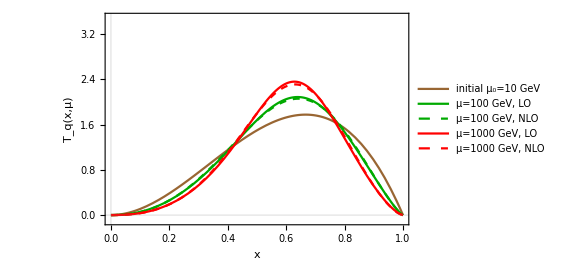

```mathematica
plotT[q]=Plot[{trackfunction["LO","q",μ0],poly["LO",q,100,25],poly["NLO",q,100,25],poly["LO",q,1000,25],poly["NLO",q,1000,25]},{x,0,1},PlotRange->{{0,1},{-0.1,3.5}},PlotStyle->{{Brown},{Darker[Green]},{Darker[Green],Dashed},{Red},{Red,Dashed}},PlotTheme->"Scientific",FrameLabel->{{"T_q(x,μ)",None},{HoldForm[x],None}},LabelStyle->{FontFamily-> "Times",FontSize-> 14,Black},PlotLegends->Placed[{"initial μ_0=10 GeV","μ=100 GeV, LO","μ=100 GeV, NLO","μ=1000 GeV, LO","μ=1000 GeV, NLO"},{Left,Top}]]
```

## Initial condition: NLO track functions (from Pythia), smoothed

### Initial Conditions: μ_0=100 GeV, from Pythia, smoothed

```mathematica
<<"trackfunctions_mu_100GeV_fromPythia.m";
```

#### Fitting

```mathematica
ansatz=x (1-x) Sum[c[i] x^i,{i,0,11}]
samples=RandomReal[{0,1},{100},WorkingPrecision->50];

err=Total[((ansatz/. x->#)-trackNLO[6][#])^2&/@samples]//Simplify;
sol=(err//NMinimize[#,Table[c[i],{i,0,11}]]&)[[2]]
gluonfit$res[x_]=ansatz/. sol

err=Total[((ansatz/. x->#)-Sum[trackNLO[i][#],{i,1,5}]/5)^2&/@samples]//Simplify;
sol=(err//NMinimize[#,Table[c[i],{i,0,11}]]&)[[2]]
quarkfit$res[x_]=ansatz/. sol
```

(1-x) x (c[0]+x c[1]+x^2 c[2]+x^3 c[3]+x^4 c[4]+x^5 c[5]+x^6 c[6]+x^7 c[7]+x^8 c[8]+x^9 c[9]+x^10 c[10]+x^11 c[11])

{c[0]→-27.8131,c[1]→875.928,c[2]→-9238.77,c[3]→45600.,c[4]→-116274.,c[5]→148476.,c[6]→-61352.,c[7]→-58983.4,c[8]→101813.,c[9]→-116114.,c[10]→103881.,c[11]→-38709.5}

(1-x) x (-27.8131+875.928 x-9238.77 x^2+45600. x^3-116274. x^4+148476. x^5-61352. x^6-58983.4 x^7+101813. x^8-116114. x^9+103881. x^10-38709.5 x^11)

{c[0]→1.60222,c[1]→-32.9789,c[2]→406.447,c[3]→-2198.71,c[4]→6930.5,c[5]→-13549.1,c[6]→18381.5,c[7]→-17992.8,c[8]→11898.5,c[9]→-5243.48,c[10]→1983.95,c[11]→-574.426}

(1-x) x (1.60222-32.9789 x+406.447 x^2-2198.71 x^3+6930.5 x^4-13549.1 x^5+18381.5 x^6-17992.8 x^7+11898.5 x^8-5243.48 x^9+1983.95 x^10-574.426 x^11)

```mathematica
(* a approximate polynomial for the initial gluon track function :*)(1-x) x (0.42838948532423066 -9.200391627599718 x+0.7209602286141799 x^2+972.1894603487152 x^3-8392.564057064168 x^4+39180.06898250861 x^5-123131.70345048283 x^6+277361.5510461998 x^7-421491.8390951007 x^8+393353.0970790345 x^9-199953.61057643848 x^10+42105.82649382423 x^11);
```

```mathematica
templistnum=CoefficientList[(0.42838948532423066 -9.200391627599718 x+0.7209602286141799 x^2+972.1894603487152 x^3-8392.564057064168 x^4+39180.06898250861 x^5-123131.70345048283 x^6+277361.5510461998 x^7-421491.8390951007 x^8+393353.0970790345 x^9-199953.61057643848 x^10+42105.82649382423 x^11),x]
```

{0.428389,-9.20039,0.72096,972.189,-8392.56,39180.1,-123132.,277362.,-421492.,393353.,-199954.,42105.8}

```mathematica
82649382423//IntegerLength
```

11

```mathematica
templistana={42838948532423066*10^-17,-9200391627599718*10^-15,7209602286141799*10^-16,9721894603487152*10^-13,-8392564057064168*10^-12,3918006898250861*10^-11,-12313170345048283*10^-11,2773615510461998*10^-10,-4214918390951007*10^-10,3933530970790345*10^-10,-19995361057643848*10^-11,4210582649382423*10^-11};
```

```mathematica
templistana-templistnum
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
gluonfit[x]=x(1-x)*(templistana.(x^#&/@Range[0,11]))
```

(1-x) x (21419474266211533/50000000000000000-(4600195813799859 x)/500000000000000+(7209602286141799 x^2)/10000000000000000+(607618412717947 x^3)/625000000000-(1049070507133021 x^4)/125000000000+(3918006898250861 x^5)/100000000000-(12313170345048283 x^6)/100000000000+(1386807755230999 x^7)/5000000000-(4214918390951007 x^8)/10000000000+(786706194158069 x^9)/2000000000-(2499420132205481 x^10)/12500000000+(4210582649382423 x^11)/100000000000)

```mathematica
(* a approximate polynomial for the initial quark track function :*)(1-x) x (1.0538944600541702 -28.523529244166088 x+700.5012156042144 x^2-8007.546106039996 x^3+54240.07460990269 x^4-230376.26423170482 x^5+638300.4178141191 x^6-1.1680671441913843*^6 x^7+1.399449746199915*^6 x^8-1.0568483030729524*^6 x^9+456904.11986243253 x^10-86259.15422473433 x^11)
```

```mathematica
templistnum=CoefficientList[(1.0538944600541702 -28.523529244166088 x+700.5012156042144 x^2-8007.546106039996 x^3+54240.07460990269 x^4-230376.26423170482 x^5+638300.4178141191 x^6-1.1680671441913843*^6 x^7+1.399449746199915*^6 x^8-1.0568483030729524*^6 x^9+456904.11986243253 x^10-86259.15422473433 x^11),x]
```

{1.05389,-28.5235,700.501,-8007.55,54240.1,-230376.,638300.,-1.16807×10^6,1.39945×10^6,-1.05685×10^6,456904.,-86259.2}

```mathematica
15422473433//IntegerLength
```

11

```mathematica
templistana={10538944600541702*10^-16,-28523529244166088*10^-15,7005012156042144*10^-13,-8007546106039996*10^-12,5424007460990269*10^-11,-23037626423170482*10^-11,6383004178141191*10^-10,-11680671441913843*10^-10,1399449746199915*10^-9,-10568483030729524*10^-10,45690411986243253*10^-11,-8625915422473433*10^-11};
```

```mathematica
templistana-templistnum
```

{0.,0.,0.,0.,0.,2.91038×10^-11,0.,0.,0.,0.,0.,0.}

```mathematica
quarkfit[x]=x(1-x)*(templistana.(x^#&/@Range[0,11]))
```

(1-x) x (5269472300270851/5000000000000000-(3565441155520761 x)/125000000000000+(218906629876317 x^2)/312500000000-(2001886526509999 x^3)/250000000000+(5424007460990269 x^4)/100000000000-(11518813211585241 x^5)/50000000000+(6383004178141191 x^6)/10000000000-(11680671441913843 x^7)/10000000000+(279889949239983 x^8)/200000000-(2642120757682381 x^9)/2500000000+(45690411986243253 x^10)/100000000000-(8625915422473433 x^11)/100000000000)

```mathematica
(*normalize*)
gluonfit[x]=gluonfit[x]/Integrate[gluonfit[x],{x,0,1}]
quarkfit[x]=quarkfit[x]/Integrate[quarkfit[x],{x,0,1}]
```

(200200000000000000000 (1-x) x (21419474266211533/50000000000000000-(4600195813799859 x)/500000000000000+(7209602286141799 x^2)/10000000000000000+(607618412717947 x^3)/625000000000-(1049070507133021 x^4)/125000000000+(3918006898250861 x^5)/100000000000-(12313170345048283 x^6)/100000000000+(1386807755230999 x^7)/5000000000-(4214918390951007 x^8)/10000000000+(786706194158069 x^9)/2000000000-(2499420132205481 x^10)/12500000000+(4210582649382423 x^11)/100000000000))/200431366434915776521

(90090000000000000000 (1-x) x (5269472300270851/5000000000000000-(3565441155520761 x)/125000000000000+(218906629876317 x^2)/312500000000-(2001886526509999 x^3)/250000000000+(5424007460990269 x^4)/100000000000-(11518813211585241 x^5)/50000000000+(6383004178141191 x^6)/10000000000-(11680671441913843 x^7)/10000000000+(279889949239983 x^8)/200000000-(2642120757682381 x^9)/2500000000+(45690411986243253 x^10)/100000000000-(8625915422473433 x^11)/100000000000))/89985178346857411693

```mathematica
Integrate[gluonfit[x],{x,0,1}]
Integrate[quarkfit[x],{x,0,1}]
```

1

1

#### To get the initial moments

```mathematica
(*
We suggest that the expression of the initial track function T(x) be in terms of x and exact numbers (such as integers and fractions), since numbers without sufficiently high precision lead to the uncertainties in the values of the moments T(n) and then with such errors the polynomial restored from those moment values are likely to further degenerate even at the initial scale. Additionally, with the exact numbers it would be convenient to set arbitrarily high working precision for the evolution process. 
*)
```

```mathematica
gluonfit[x]=(200200000000000000000 (1-x) x (21419474266211533/50000000000000000-(4600195813799859 x)/500000000000000+(7209602286141799 x^2)/10000000000000000+(607618412717947 x^3)/625000000000-(1049070507133021 x^4)/125000000000+(3918006898250861 x^5)/100000000000-(12313170345048283 x^6)/100000000000+(1386807755230999 x^7)/5000000000-(4214918390951007 x^8)/10000000000+(786706194158069 x^9)/2000000000-(2499420132205481 x^10)/12500000000+(4210582649382423 x^11)/100000000000))/200431366434915776521;
```

```mathematica
quarkfit[x]=(90090000000000000000 (1-x) x (5269472300270851/5000000000000000-(3565441155520761 x)/125000000000000+(218906629876317 x^2)/312500000000-(2001886526509999 x^3)/250000000000+(5424007460990269 x^4)/100000000000-(11518813211585241 x^5)/50000000000+(6383004178141191 x^6)/10000000000-(11680671441913843 x^7)/10000000000+(279889949239983 x^8)/200000000-(2642120757682381 x^9)/2500000000+(45690411986243253 x^10)/100000000000-(8625915422473433 x^11)/100000000000))/89985178346857411693;
```

```mathematica
μ0:=100
```

```mathematica
trackfunction["NLO","g",μ0]=gluonfit[x];
```

```mathematica
trackfunction["NLO","q",μ0]=quarkfit[x];
```

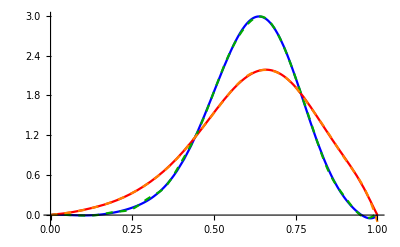

```mathematica
Plot[{trackfunction["NLO","g",μ0],trackfunction["NLO","q",μ0],trackNLO[6][x],(Plus@@(trackNLO[#][x]&/@Range[5]))/5},{x,0,1},PlotStyle->{{Blue},{Red},{Darker[Green],Dashed},{Orange,Dashed}}]
```

```mathematica
tempg=Table[Integrate[trackfunction["NLO","g",μ0]*x^ii,{x,0,1}],{ii,1,nmax}];
```

```mathematica
tempq=Table[Integrate[trackfunction["NLO","q",μ0]*x^ii,{x,0,1}],{ii,1,nmax}];
```

```mathematica
initialT={(*gluon*)tempg,(*quark*)tempq}
```

{{371194384700371004591/601294099304747329563,3592555610942383398947/9019411489571209943445,27234297890058877722919/102219996881807046025710,3754941567568375859497/20443999376361409205142,50464116227190018380747/388435988150866774897698,640279314636609722081/6814666458787136401714,201811461140619686287243/2913269911131500811732735,151323565293660533049617/2913269911131500811732735,176569367370314695080517/4467013863734967911323527,136114598911410408970495/4467013863734967911323527,1273467462489277774248617/53604166364819614935882324,29318547638964865749469/1567373285521041372394220,57699347009810203148059/3884359881508667748976980,1910812898002160910010747/160812499094458844807646972,11149742282101235156749901/1165890618434826624855440547,530521740210306072248095/68581801084401566167967091,66777077124275419651632257/10630179168082242756034899105,30776073465060146020169/6015947463543997032277815,311312139085926886839511/74597748547945563200244906,64790735779999355784291179/19022425879726118616062451030,17611917787517037385217177/6340808626575372872020817010,3114880367265159292956617/1378436657951168015656699350,140061080243307760447998169/76503234516289824868946813925,85689369628893732792385813/58142458232380266900399578583,124025959961505625335523/105521702781089413612340433,17925985388577610522027297/19380819410793422300133192861,2521784309878710699240184221/3531615981522356952468715143560,195802864988049974206083473/365339584295416236462280876920},{111824204874000310161/179970356693714823386,376513707156345091519/899851783468574116930,2277796520810415717301/7648740159482879993905,338110371375696242403/1529748031896575998781,19717159096387040876231/116260850424139775907356,15546703798700218237377/116260850424139775907356,15674477813519918746593/145326063030174719884195,12887222786212006354087/145326063030174719884195,99087327352504433398507/1336999779877607422934594,83986228236793804311069/1336999779877607422934594,36031129225595361691313/668499889938803711467297,156237834075822215582356/3342499449694018557336485,3282559583779654894991911/80219986792656445376075640,25196097764254664388923/697565102544838655444136,1868053161057543741021289/58159490424675922897654839,98360131794321233520655/3421146495569171935156167,27455161389233311832039789/1060555413626443299898411770,1308049454634030371819599/55818705980339121047284830,2087341862213364408777/97927554351472142188219,1847823632176818750135506/94891800166576505780384211,33897286509304312856131957/1897836003331530115607684220,6783683090454621316216177/412573044202506546871235700,19319622843299068107107453/1272100219624395186186310075,40811756777896680782947583/2900388500743621024504786971,75841004822012951726510567/5800777001487242049009573942,23551439812237815088005379/1933592333829080683003191314,2254448057250569575659976483/198193214217480770007827109685,145533221949652316147611071/13668497532240053103988076530}}

```mathematica
Clear[temp1,tempg,tempq,temp2]
```

#### Check the initial condition restored

```mathematica
ll:=15
basischeck=Table[{Sum[(ll+1)^2/(k+m+1)If[m==0,1,Product[1-(ll+1)^2/j^2,{j,1,m}]]If[k==0,1,Product[1-(ll+1)^2/j^2,{j,1,k}]] x^k,{k,0,ll}]},{m,0,ll}];
```

```mathematica
tempplotg=Flatten[basischeck].Join[{1},Table[initialT⟦1,ii⟧,{ii,1,ll}]  ]//Expand;
```

```mathematica
tempplotq=Flatten[basischeck].Join[{1},Table[initialT⟦2,ii⟧,{ii,1,ll}] ]//Expand;
```

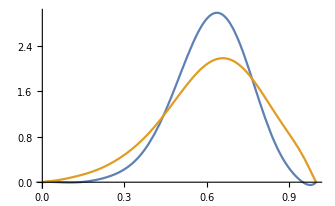

```mathematica
Plot[{tempplotg,tempplotq},{x,0,1}]
```

```mathematica
ll:=26
basischeck=Table[{Sum[(ll+1)^2/(k+m+1)If[m==0,1,Product[1-(ll+1)^2/j^2,{j,1,m}]]If[k==0,1,Product[1-(ll+1)^2/j^2,{j,1,k}]] x^k,{k,0,ll}]},{m,0,ll}];
```

```mathematica
tempplotg=Flatten[basischeck].Join[{1},Table[initialT⟦1,ii⟧,{ii,1,ll}]  ]//Expand;
```

```mathematica
tempplotq=Flatten[basischeck].Join[{1},Table[initialT⟦2,ii⟧,{ii,1,ll}] ]//Expand;
```

```mathematica
Plot[{tempplotg,tempplotq},{x,0,1}]
```

-Graphics-

```mathematica
(* old *)
```

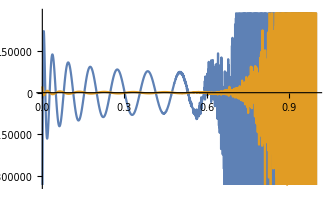

```mathematica
Plot[{tempplotg,tempplotq},{x,0,1}]
```

### Polynomial basis

```mathematica
(* mnum is the number of the moments that we use to restore T(x), including the zeroth moment *)
(* the degree of the polynomial is mnum-1 *)
```

```mathematica
(* the polynomial basis we choose*)
basis[mnum_]:=Table[{Sum[mnum^2/(i+j-1)If[i>1,Product[1-mnum^2/(k-1)^2,{k,2,i}],1]If[j>1,Product[1-mnum^2/(k-1)^2,{k,2,j}],1] x^(j-1),{j,1,mnum}]},{i,1,mnum}];
```

```mathematica
(* check *)
Integrate[basis[mnum].{Table[x^k,{k,0,mnum-1}]},{x,0,1}]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Plot[Flatten[basis[26]]//Last,{x,0,1},WorkingPrecision->100]
```

-Graphics-

### Evolving moments and restoring T(x) from the moments: LO

```mathematica
?evoLO
```

#### μ=10 GeV

```mathematica
(* Specify the final scale mu1: E.g., if Subscript[μ, 1]=91.2 GeV, then write it as 912/10 in order to ensure the working precision you set can be definitely achieved. *)
```

```mathematica
mu1=10;
```

```mathematica
(* evolving... *)
(* Fewer steps such as 100 and 1000 steps are okay. *)
```

```mathematica
TmulistLO[mu1]=evoLO[initialT,μ0,mu1,30000,200]
```

{{0.6164766632389098691966642453374182346598977648353311245857181855243685633981236707663727711744598876029767061453361046746045578713655327891923906074589682440869213629476318116686569688621737177163961,0.4058066129340517123267625392773684911152107638602301586986589763050225207471484701426427753557496578531688770397283209246723158614944083532716039846635326255501374657975663964863395502274790800897032,0.2806637765104811393539732887044474485077543739088179945157401273675681234309674879749127788144421034836619104157162080335640249852760012869930654697166039298950035109794150225592179179790700456532582,0.2016399323097844362998533233367308637369088958566104356868757357056562121148777548852593545076606496472662859594074929302248859067570049437869597983866859495858052430009499359516280044870926103661938,0.1492498437254115871308392349939358004650880052705012555112160439905459971020803013856693057117034081311278061263395430009200912672461191729636498633483526457288013327066880999269688022528096135826193,0.113121511355922520582047231089677459530331283161833061470976134646831047152576685589991437751884798867737689755942151941360312747205766390629088204933822745541805368084865072520124144974321472971249,0.0873865659783076776675386026594654501644640817128870621179140668176293706895557373451219132858169039922168255551814836909154335145605631059240891085181705418600411460638486363487850915187895153000144,0.0685523242934812642295079275454851711544537799531699175379088556254260315048904465318115937027460606048632403411576212442414005901446270014890794342492913612898218640445757730694972682841715715650534,0.0544496269874490178894193636670884273044488240556218170382365946566645643336275455786049138438708504834832693155893252721388367332363870752975804646293701369620816664628448551075789043555885556878406,0.0436815425040179541940482973933054330292217787788522762102206649654680591668070925677239305489001499050726065429984367619207242024030839160044454159367867956725781643191330592473090448947316281627003,0.0353199190314329509682761315920304871212342790293750483769796966678677220896238016848728024611905225404206533860132617293663517248139295411041765569700594136769207375004715355395848372959755268592241,0.0287311211007721848882794452780327497323104232591416137003965264874116644667754546357684382584492252401830976232266174751273010452376784019766764711107663873381933909161404356203310909958848643283827,0.0234721867719384271093656401650065734617678469598100872628383364258712520028433643166077404404473773332494396248137658039701446380324664266004813099643853384489300161300203568859314363998269405825629,0.0192269050805452381835823795551597381259172629371217012327021011022996308598279533902950642248514285252560286591665434131971114044015213749244577018349653611888020659264044470648192884673280130701803,0.0157653192794109840945069386692681469517296075872651465825964161707705381815796394378476729873316168260796875474988124749301737367446767789375986173057037486935856939039987518374692408787371111003047,0.0129174056702116375958292586650594088800324966522244868026069104831433463076829602499031233901264833982185698113278896914784224876289889102189980020107414823807527356185710545766416070763722446945939,0.0105555695483149133206432290280180967152069793646041003556145330802820465955399260253866326454575722346160779379200005726881028067126108622837787049212683387953364961215778053013319999912817422482485,0.00858276251953009509841745030904806819391520415019631271334420127807238541279471995833747499866743429894435808359054749361348584419380985233353677390387984221137814915418535672603560485952862066372335,0.00692426455736163063239467333397763930158730895563252317772827723320644510438290058965038326774566802635231481497851756835545169294132779746590622354447842545078182679878060354647592575994377575940116,0.00552190397497543348015955073486364778303976541090726163516917053009842587704655092528936728410324032542327420728896402332639447266531274945281428866453482883924280849442670057162618329641276961756504,0.00432992925130492040497853924060425409520151554242507308477088974034985222842177083374796492884674840002321918867450554256204271363541489190137889534247025167278049882627351934942964898650020244261906,0.00331201901849288502925191507553006848860531169062432599042251190496055901317315273155781933636804616642486508037391657424261796884876698901395960572835407629803805065384067318426522246789734249679707,0.00243908839146542483597739383580850853456778812714106429829129607957099801032360721169246490008343414337478117241901111377518706663533194499734888828110338693847560480380846592923866563737081311914516,0.00168766038575148059624787448321865673277458674989720719973099856789574119869893814100689807706730453657502147844785258028718078004614977226309967385106154683484916530504496773459551814858429790113741,0.00103864356616890279072471051765538673031714721452069146192971190609764087144169003733094647848911402992430136976586784975535944261748598939351271901273122457649805000803278975731298707270363683676597,0.000476405253670420650328492745720064935808791279430055663979516703544938634674440948730320177079174352078320967774382980200909650991593380625944580193704756091041005704910698581504511705697321776247523,-0.00001193782428472566453655116566960667826974417965676815262384639479496804845627925890994534604798878426047573794257850848263186825611612000590512655364843085022291689582880911011843943880291963316395,-0.000437067245082273956972025063030671177094489368589700918778649006144845549510145399189881546083487890664373247968669523750558969598461486520952040391234586491112742477778572579347581049980739053449707},{0.6222536974549377462083886936730808798639817510372087161058085572147098078382811009688325454637001783506183930876431271658380417586562613958025080348143488355974996124791901827610699298223466191143468,0.4285217262721699259430227506068147908255100501008207571008497405844441912085228405445751658917433729598942332516219868040489666698982292086104135066704935419640458459119766128944280911961553255874757,0.314651761168765003384688246472602672999544677569570923170733918410938521034410354463270740175755610558826162770756975459547668692193728510786991554962929741099601663543205687600877769436929971093319,0.2417832669964733407911395972263024486151213924421807736459673454425765312979261657485422812867244473086762537643573149730579095985926970357882542026803834111231500457781054179342343682887085508723333,0.1922462978116748613721547780074817212036592130786147067166795802183159123184789590378556091836318449465116308297960458637332256689309083882708514921336668962215182162642046949381162637030789616963595,0.1569870807814825207568483691352471509925096954574073233737950826714254872209490983636061156119421112933379244247427645815072204674481761981868174594353407836703085590308240482734742817598557652287771,0.1309613418388800691080306209613188213939648949866074551019899948410923937367877733738142824793781340480140079632760860198131950182365454055071943073079517773801224798385436729010025215811595074921072,0.1111746155865366445802702230441896397832547144330414738981576114496659122701321662228979740354875131312091696270753745903843459535929561064177131764864805976715374943186157701639417994323278065319242,0.09575747264920105477550103749420810492091769201539431366279738431701064757317043403807415733462647597498323451020899549214149589046165281814320570114617062990173471931671862251486899213780025358208313,0.08349370021679962165306896134308106287454897512018910821673571987372022501794354753145588528838008609498343294556107501467848786830553355183497746690900993757051936943684933728013168992323222766996908,0.07356424528861109075137170102191053325141355205288736713565277224225171172824449808157210892458882657918246689427557048805037709241025619163179742167224786297780750397734727777408327219502396378572878,0.06540104618457493103444462657677864218062635867640546133254166162660599706325350670959982720980575418663148559233940176310585215055257021868865627459855629100396359709007749644593310355537552050295051,0.05859997822240344715649959540847849520339356143675399630086063669747088232997569212534885834165529818406366612900979260366134468161762536011104948330603776535608240789341340683015433611334377557807292,0.05286709339697430845602497560720690443573499832327226947563719846117183715269007356296461031546868025726958769617324675756577908418194760622492736790926429144294658969294075755678994043553966263892713,0.04798436201605177353931360558985463328648079619341654356755718259105236467399087461466279831074905169391764232647705983794845841797388065774859264510468001147093061779004508591880581092754910321876178,0.04378723293549734017523056679066639078300566230638422784248473320233640468116104050755576023474041454639568357986669209555512410276013674014689233742304619188555558631286367254180786834313422266358982,0.04014957313144270715193755918315709615240943099290526245334519292429842609449493453549532119016886003276221353641811911515917199924211037726676918530439597185678127708637914909662411049555308714664128,0.03697333824727117262774914635691380398608904573240214433223256494339034958854345553052316273521367149595668316553215101703986443724296634198501138365509816230917279902080655833877652808255708075299237,0.03418134866293010789882852360110030973572953268648477436332830143189040733482255029340586692168260048589017812076196398772148944260790520185352868758781179915282762778226230037979103003908360614763762,0.0317121478117042854465347742276241871643013490773085774905648171323188808309442122780254585417178032517616294061147704197992801842766400798011215019612229551633502321497570266048396577052656963274905,0.02951628367884259623734245013600758287209420348077131023870875386654541139992310730869017898533354994963215022335473413094147762213099169552490704914006163460019915897622604429429406138018731619153708,0.02755358012744248709446765723050125980764260572690962020818755453379757534861764690059688099881919177354301649297995268559951318087268837790996880098728482022462529910258035873900188022565623698043439,0.02579110769770207998807766644092877785193264334451056861203693514074101066046573324720004105808422617778504306069722198922484344226993690708938716809733501321854731785392272293289088967689508913930865,0.02420165596425556481104637243125712839837798537730443247373852470789192955919616198470223701665825228679642566810722868066784016774854784553652743547265916624728241403544414489430276330777211979678041,0.02276257039977177957419238169810863246723603647163556053772377504346834766957424278182008223795400258121250378456003756954299171225827419093324203345051195018537728838045680368356714188453959202667556,0.02145485744969183123809106941175829508872285448837894174026980842287536924556225863789364180286062115477834282936901297142386179227674137091656314224062374529821033971570570461896850330889654196859854,0.02026248924396426698476178683656704521293475445336873572168867266151391386718911733057737239027546657573102897897615522524196776903973934226252938850427921351236581216967119165311149422866842937205136,0.01917185850006389160032390698649030591890089722789996630482783516971662539615349732247613991793940555608426292540804090064128144011029223410095985286880363552224881643301778329945320934673788875206006}}

```mathematica
(* 10 moments *)
```

```mathematica
mnum:=10
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

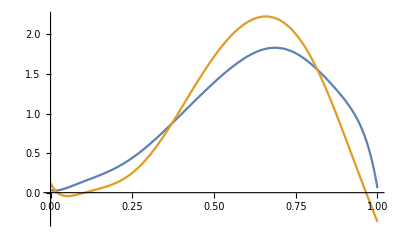

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1}]
```

```mathematica
(* 15 moments *)
```

```mathematica
mnum:=15
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

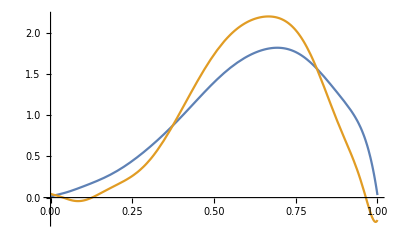

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1}]
```

```mathematica
(* 20 moments *)
```

```mathematica
mnum:=20
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

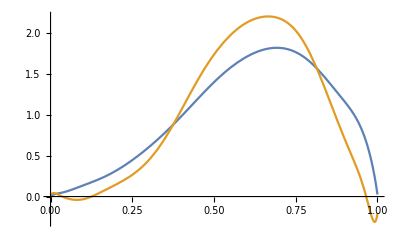

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1}]
```

```mathematica
(* 23 moments *)
```

```mathematica
mnum:=23
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.02461940315707489729253927140106076555208730642217781724521076351207116272796585079493595994672209402319830466892387218789444862262634492704441081538095498437005814668249755326737083+3.30203413787408656968656281079684240422503517631243698167710744625969011162151885304748734968940932746861309200532157123746798676051243503582363004607982717584307136160072658005802 x-192.695895242219386816782876296911857886366515641079260435326194219500355471866904966320899003668127956327916533309155296308093570404218309925830311165583478646303285295137004611972 x^2+1022.4285430903190132518172306424762266079472515697121882260211082769851779230725598439401924638170851812530336417846981809364280327178474223982459430515599217179120919469911785047 x^3+114821.87989594715803679659435409587668511329644871942889020348060997470831938612045984913368413088633143959644626237398540073938216282538097383715749473041096332168346581034086466 x^4-3.84173500771985488525745078414471303412276343242552298594584259614659592393017719708312962635684916975212374202441321984844315901337972054901498320493961653357584355981291886409002×10^6 x^5+6.54538415870665833950223143091674965868283629062857241856151925817329458081545194546813073430982902216380831782711150072187243485768816016920646420320571435974170515970638876378174×10^7 x^6-7.28486097911874764774903899292288487148446969023537814789363987912424544972511402558645883182094082066023310096294683464807705204205282546884416053548948676277187491318827038012182×10^8 x^7+5.76667661796852722172933259202387680614534061975652513862990744942780113648925892642162933884598922745713598983531614476835580988374374234904509652132631736738740350679973931907482×10^9 x^8-3.39471201817444857114392318508723984610811276441018859874771086632401893379629884835063919981584831237224580960049514351946956472690916911357134776254510464739819281565379771789398×10^10 x^9+1.52769980230245561545108528559375515545562815626954901052410654707082640222012737258448837303911301037431426009300990370118073764448113114822223868582185576805847863538247732236246×10^11 x^10-5.35150907625362384997250810703726197847723514554994126618658207008678927195671901904785821869016128810984701259572759715446177341558782674787341444870418277891638658657478143535379×10^11 x^11+1.47627962762571806663568076056028321524897091602734717697125818288103974098191110685289718236999199743370441160224499284799284262003436036829133588002115681188193260971595602803004×10^12 x^12-3.22849797172037381076339806287244522552661181390515858435315375918217387314182904867143544037865272558945622358704383848175678775712777888503058522359173458513329570464507594491638×10^12 x^13+5.60992448049008188984279801821878328307977974022774918933580322389401305385905833989853201536479725003108276991076400820619478088832871716092746076907850838744394288857123618593978×10^12 x^14-7.72929044382132297861768748731003874218307831475585922037378586390441225229007784120750692450513961496206740415287578874155331980256202943310963781347371229692930685544407850143656×10^12 x^15+8.38582282601579419134127487689115810302755359617630837515261609447280112441687152513758378438950877303867013247334094159454097712067679878367698836556873760223533446019873915826135×10^12 x^16-7.07186743602910719028773647330018120099331398254484252759751907863214475743592211987557765475413947457781024196381080906073798768475390673945027643663213287063684508167442417362008×10^12 x^17+4.53692378366191597328230908577367400554056739344224587408275892264285526786601671682083431826635055156806130990991615829762283138350810327539564397204685245235938186395799240076506×10^12 x^18-2.1381733011723450140306049283782604084332769986598822102781185904924796472075837473440384124067068825948645022965970577468603852536817857597184471906227749696859720765583425582679×10^12 x^19+6.97597154340026720659121103963444759306053423433114840754802918345587362002631487222735833608464624107710206958676717786162691601819575836776192720227623174098989204448328718998038×10^11 x^20-1.40704015858234800197383491384586853841150826558546192038185523601990274409809496802789557744827147166705983825567584244233319714543538746414533708623901410266694262398207234499927×10^11 x^21+1.32134257629503077795839499994953576067964163640866460820158044145036140879249282675441692732407388120659429321713749109997359416256006413463987162606709641480370238419345713838453×10^10 x^22

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.00266593006019854742589283036176586466321510385408542378887400770900075858670049164579935777332071011047338144413477130585716917685838060225021497537184232600730419286297600366025366+3.998995587750671721827975920290993430991992808817137161706323677144143998090295991897118749530667936795091235654763637867311259059401764288695149452231041122228501594308012357944493 x-239.032416239793837597495466637360858364132848887115129754500228258660801354434767401828318868164008684472479185599846080073835380533299165687752167446652337800715962589000775709413 x^2+9314.80596099818266380583599567776992657684532047332468724475537904400973676515751310734232495887384368096464065798006591707964091176677526241749015797448351840484394557693212911732 x^3-221921.632675786630465459351807432388769359189875269884854723552712575991003577598116896534682508344752665415432186371319526550999698264227060906265317478713724867332132771894463075 x^4+3.64390644789734583962414122644649695990739993819595757595890430286312708887853869493558658907974373623447139454450996175499702246203642541879210644299884974719050563852815823775386×10^6 x^5-4.34143665182892276963743369201739491401070558471756007048687686434568182102882706019210678396617445462240589151180855148755382303789868664768957275575082582743478957490570365538206×10^7 x^6+3.86225485685832032246269955446769207911404669260503147814686121150353399072471335753839748876021739509300676209182232988446602752880055707075916485459777995609268984973571474046323×10^8 x^7-2.61805348823920295605483111279131935961187364650441280984248827976734028753735007165244274992270863206286606035144834803155086358768594894840552383298144468831261489346784562160449×10^9 x^8+1.3743356017193926893478672053682173537732202029416514345900308307429836322581183969363691061159739948888080387866719852575806469949081674405032553803722669909395061077363881646462×10^10 x^9-5.66023690502573315191879211791908106998898564097482071353088264999914576847582503247769038326502874258438507214078929972174419074327339020387282614480347158962521367032547642065446×10^10 x^10+1.84704040040570335627881056540597945363739015520296816405164096478828322394866725269413055774708344812884800465730552670342518895390818360783084853138443928258206532261217584874589×10^11 x^11-4.80736192147243035730927052876978510511516966786730607459859656807015911629051670991869542083851203906465329665551429818071734317264657599350151753710603795751529809723251470310964×10^11 x^12+1.00142639935074708647127586390018653246617314578380796153053313527672270346522871367615721484160856735195498422461603947926689399896809808190952965548936883328158692626368485301063×10^12 x^13-1.66975084591393102785371406700498586480484724880803426687325060424363298198011194902924250161998679153998836227899976214234328444337683374917788165437765783733149783294912235284427×10^12 x^14+2.22041113816231478199637084485232027601151642274404609634500497131876337961395750788993749333978718660093556016646743288320749957105538034362301041795023205490521122526187977182392×10^12 x^15-2.33596452899411890687469603113038986035398208959597260587406539716646586276486585382092815755978441009038216378065567076705606837841481828003594441326922674922405868770913889120377×10^12 x^16+1.91749766179855632416907488274367349572587564409294767161778338572292837244702053705036095697075032427951818310525385966987529929003389150705710529618028373089749582912744863810358×10^12 x^17-1.20117772550569565391492311171521168046104632054939364060934646193322129783655146062110663856743364320146938407804485959276255340818533818294612180420774243399704435822183565025413×10^12 x^18+5.54208079744915930604827193062820927993169769795998936668823509517354013664384960138358583570409835471019004142825925589534134909748549016091672762761595636306570603916032986749763×10^11 x^19-1.7741037950120487952715430570460432179763200006646522382202150022504798441644006160760721369118167390325984926490282265852900379790796814194072908837438972578538288133887030178906×10^11 x^20+3.51756465270429130902397957543641834527460040558055522316215630751438094346762771643983543395938313475283601624214824049940918894869625884055489354974419426077603988367951630528764×10^10 x^21-3.25246922438817839417967338631774043453369139479661617842861932799539836367672095143336959483626411557970207369473394140227729032501512215388775298883060049248877289844710132808947×10^9 x^22

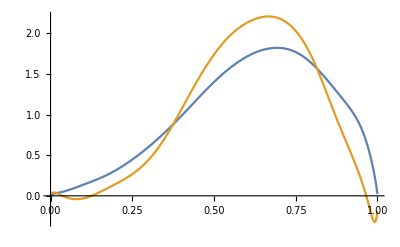

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1}]
```

```mathematica
(* 25 moments *)
```

```mathematica
mnum:=25
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.022706551828578702714933477779405174822001001986786232260067789095724587361142082323653753394361423599041195150116296621002018089516447239960517499141823506443980225569581825920504+4.1132885702023188339471564158821850337074452197180504179106207646311941015512355637991726493397248268684473851604279748064991808124983732602277748502023502576254223271719277475029 x-267.5474545371012438180761971580536096868891404115293166143499972380119107128955640000883491948260782292848940174764222725127195030876680289316478676901566263906595913812066121391 x^2+3125.18278032986847918100455577399759064806647929060171976047902154838680812123042904798926339465250399728422918589061457738778581516454005715730849359014334854018359895398421621 x^3+134373.5977534917538467778099573737165587975220547532615284975305780200262282850491462200657595944331540114463027288247334219693855214955870445608433157424675134495447925915524765 x^4-6.386818281258607160553855953437696769007179340238371130461346925086976068744027040924311261236182800645111817269790045230746884219913409280382577156581843212340772009314620189907×10^6 x^5+1.366584706135873220807341493823707764702613402285368086264651841530848571985787852874324882233505174139491304453203634917098565884177110348798630165301908362661538414260949126118×10^8 x^6-1.868606222255642321172519623081422308178646430188984709473714208017109779384326485250875978547830551333672758932263872069965321772012524590469690098469956087153569210986670077617×10^9 x^7+1.808148229829089565742179665808786247218575572627569289960732191333902441613078569033322343360114560927078914968649157295689760151731732094646392759431226228369440119121575484552×10^10 x^8-1.302880408288652420267264554658615553017628898381081181896951968781817210899470766883872340774911373395039145234957948885225226805640844154465215944252045472700475855614166481991×10^11 x^9+7.212285080168767211656851935329182552079807251989435562719843288386635910658477396680750533214008678017402015308908937945097074662259601714704472113243681776745341737118835487111×10^11 x^10-3.131630587163601541529290333996878458165821259167650310354302445668888631412940691458385488612419256029774244680788473123573581858689198322177757164542777331749246220096026262975×10^12 x^11+1.0818659653218402695755434275184032906798176150109539409443911766013540684691432976575203261937624076763454781669966364034076003682325617396635299986306718738695453834808763237554×10^13 x^12-3.0019158205698971863506065438755987820656886965619551296266690144831134730705502895928042255117729593259091675921538112155038506105136114690479613645206980569574221238491391023758×10^13 x^13+6.728331356778906865134709420365786076872244293196961486032089236230857058228445963171156411977876646026773488678742809834253786093943730724702308389851304226845850886003648656786×10^13 x^14-1.2209265839522556545305028568832102765884398279113919504033752808160683471003835176853531541822837512465015291497175170679599398032499220508525797151145185383680795380840198381192×10^14 x^15+1.7917917927498039913050512439442911166986814018027881359179271373781858532670707475249481726933973120830240501787138168454859558937956016254355109100893712106350007433133917971898×10^14 x^16-2.1167678244868909257011127905705046504093697090802520672993176438447962958750749023879376047449015172139117755425191003639079023958551717102639393882932652563762489758207347658506×10^14 x^17+1.9949857395578807489604276175297313952114839042842697358113342730836071598406808030899023788813476821904879070994891635677584879065399554784629151926123591782047886469610855517308×10^14 x^18-1.4781215634836543403829570005583137526280634492180347044357203023308809652368815274326469054512325471886894410733549055710929239494223441217731067874753559835994833903302185682869×10^14 x^19+8.4146005617567089869226338171532245149227052758421463412287097650586345000808294070032790978818473305829151303821697569340664076052917254248830140001561758240562969183883755002582×10^13 x^20-3.5499164294296919621983917546689714235393912536037957738401747161243224981043870325381796985831399883181138262737201688485627622277375125646111202898416898190229245103208670447503×10^13 x^21+1.0448726629542017329072768564117533896514767247919241644899879443570347652850864959773030299153620210232509318818146210853697531528034460379830286959071731211777292878680918623665×10^13 x^22-1.9145471231293260602250400304058868131287653934758083440404930708558921877407555762801175472041075565583774856268022939572510360694461421198550447584795520622549987390285589204605×10^12 x^23+1.6435495153193979032137570283313694316025543960391452159505441471116522097657536325676406767909290416940188725892737873874229629242268108959687194152494028068727795488827096344379×10^11 x^24

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.002332933519154454733108508644399980803430674601549623967781459863975659472240384702357347420803526157626255751788601696698231506200428672770108842667882811565794461240032082171428+4.2448679188834505263848938189507808814472016672701486412159737535553974244120108246357745553522222940842501379882403040688463251125317321348087750540355395986041394035821881846043 x-282.14859784201686889342114688167348886455737232067839569519665043610853901490186929487838748850765530431096504956385912281492513709693332398870180650685046008955824499985566707874 x^2+12549.03477494822828506774049175978982323927905837319094135121918244324276556264437843366556489085561603584394303159955505171669660730557089963004037599285420146357066027192398353 x^3-354039.1798508892916276983598430243222036347709012015533172417394801731202409354041723558917845834926154209026775124526068572767402117443551928373564271135527145152833563047025216 x^4+6.995441728828398845460442132592333240005473057627947903253378191170669476148618798164914052262553153646987528731103311883372208174909593690412135269433254783756564712694097776905×10^6 x^5-1.007128183330679312320529267346697883757371158943533387492198432816308146676077691101226268591863683765185342462969831513257482646246862323238142954315118538177795137846331506947×10^8 x^6+1.083815054319828904188232486221999696740879233301038238960286697677757335385446588521158751045133016639767732192351305697764511490896783733572209845289002777396549292641782766828×10^9 x^7-8.90686644876907508490991143985756817860561981934188711534111790834902046511430256794401316069131794825450819147737815953496700562017970799779207816168236073836117170615253637362×10^9 x^8+5.69372677483255102000967835776147996622851011487342407344666539448803795735237800142593039714493085755541033092461857195516937834430560614931139208251708496003447972877632193101×10^10 x^9-2.874521252234364516450240374975770448284010339014307030563953406995951972381918693574864920001046930183338364564972883779581723905483360542021228707691585399702759566781508436052×10^11 x^10+1.159873238850275176724437328002800069808057303183174175480254066376905529497673956101300136656010475055264868391709154520893755501086283858173021883412318967230823174195647468536×10^12 x^11-3.773805538390899269446941610041029485350119602567482806673047506011196705582973154027808654680796075123286658339342993068214918932740005403930561705922049437976596963141520264385×10^12 x^12+9.960633256032829203828880390679074182498240267858392902483058927767251291479088685912938483948252750865242018161289479892701492724192180121176193958963436260474685053340446460015×10^12 x^13-2.139809360984288571084478307767116869257259689326891331506480568656857670452215740082987866606588397993707473857041755787090693758238815414293377611601557695420065841677671532048×10^13 x^14+3.743816636855701476629482224050840654440362150407076964011037755780900055436650532109384811181994734199557093239430552090595166803160049468016103823979918299243680610015257953039×10^13 x^15-5.322620898711909958225977900096180877286583771556411969591159981983992797498541379496784914133236946465859005937732366896436451162816318702777306504504190174261731117352225726929×10^13 x^16+6.114921512153666363950974976738795985543045985689175656582254688412838369767920573907395777370711194354133579641243899063985532370820241107962094703226452392931794601621357424431×10^13 x^17-5.622224474558256186866884082616365981062025416443803176406469660663804864316962674569077480858432248915926582524821000046225892775515437232018516418057753356227304335588220816538×10^13 x^18+4.07447404363022589757240080598143668704223092059177182360844556444067360422064668148617240694588064271992940226169306713825935416652961459718121264721040218250685356997490503973×10^13 x^19-2.273790156066901477826822510958381375495214155502241091171708606829882634772509741913259651892407630979377207829054239926371272772821417251506634083894943393103340626353392056879×10^13 x^20+9.421272097413084709662273963358439028465618202538889605294871111872906549857131955051899368051251575018710063287256724671358243719959928083477908077293053405639287825537029347876×10^12 x^21-2.727926078894624088158349836670231319629673103139752891167834788787232521034859027143823878599340212875959387862889255574444039878853165952183919584671646342269808637541553687847×10^12 x^22+4.924042519910789500950065324379675686991670198291691506035059498667950341413308514249914738381735406780068094553578963152083554973121075927705273842941891641686226662468696327839×10^11 x^23-4.169228216989042414475443117987851891488727376663984856964185021539843125193086793634014850728318144476232162033366612670970459417799982119611668572168506182346920400547858082135×10^10 x^24

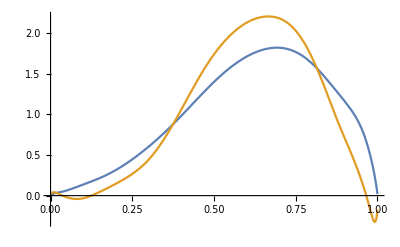

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1},WorkingPrecision->100]
```

```mathematica
(* 26 moments *)
```

```mathematica
mnum:=26
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.01676581132361658145923733794296286534550993318852130689128998622290135846647612898765554950716692666743077815174673620504904532141298432656233637024147460750597945915019194976384+7.974769898427697650149647309569686193426639938590251907616192631966292883084105232198005176016147832415218434100642245175931480079749266969045508635429134567325920499775347249337 x-893.1074297096126120428797219354287975613986848688259579466526397462979133212204502806992185164066051278618039457911340723607519843823128097601207408968956845621402953429605714362 x^2+47887.47433711845971660027899539951103411297166045716138842746810769685188365025562512725591262774798429545422850085443669984699892113689992977247853193902706658835841577282308147 x^3-1.650522778073453321745315758322693631999365572044263305259598659232150018658434830547440691878575249122878082419955357673711091737079152262875969061963419270743721426028059647276×10^6 x^4+3.859257038958040874436690196722000041465853063105684635259867705812930906240131392735593983124569319273250430654185135142900625606962291653761477645645303259173993645536579004385×10^7 x^5-6.379865564953068407262344592511784528039814426104363813595685622245289422822576424996162805916151246942209250203245716729858919387909701319856469623609653581374583599100677080806×10^8 x^6+7.743315746769003617330274541187923230571141569119090790761153502137771650908501026882300581441947211967702623172065119361361517096209478459616637802873369753609618919878368154648×10^9 x^7-7.11291684767190994593072616790370008093357141423023828369475440215359688587745196566528215138039792563701011154693118787651046217283681448621498032400304806758889386483753812477×10^10 x^8+5.063015412446628712753648497052269752750199445327329654612765625089509469704883120839329385101651857758100925537888272731480610853125353282248208305408461370588310616889991130586×10^11 x^9-2.843673151594880713326026115425177516022003147277766512173457523729279350072590437456917913169474541644018238101902990310845561622683110393089070368485515654567186250890444714332×10^12 x^10+1.277784789374837378595437997044421010765394147750527065626171904513019556870901480976059138663611562910005680822589497660280530498437607527172422211725339844850305980705486020019×10^13 x^11-4.641126988228439744060943529218043846191458147208888462324427665227760942408060139586528299763696669057857636698046437873164804760036751955920654215237674691526770256841456445635×10^13 x^12+1.372683281288476746889450917581555438725034814684989189531295529240199194333973668081287637344079972651253070662874132897755394899519669010265965402986369959573950051709306437738×10^14 x^13-3.321582354351080261779750566542737557231094572066397936943599329245398648707774945596077481409255201199562376201196599430019034765846658119141587530694409425000190317502161271324×10^14 x^14+6.59037481877106531102068587100523022369627288591030315022149419146007883509282803094489117447148896410010059987424331574055357968611031672385497620781435938599325903384980905202×10^14 x^15-1.071849561004926474258552445306453937203855380392727042367659037681408111821424462332817750991616055233926842208622345444939897766338290578718205912272640984009995556329938103467×10^15 x^16+1.424616864007382873315922497229917675008431509287809442241254263423367053879598810862410913583092157189206246153757186347507654357166550580520125601795021307295874577815721724261×10^15 x^17-1.537800853145720432094067173564054762259662588544928332733952972586390083746439844316980156790285954821832424584974321779215092386144496138980877375722639559121261319059575238317×10^15 x^18+1.334426690042949303227504466364236751464312163454355627465144344192350258925055450538726671119568110091633588609662729237586579855622683702899609043288568686676217801124182044543×10^15 x^19-9.163652156965703577851887741620137403915779403954859276760964550865845449270936381453113781448481979412600582801521007920790496930784024734280906723728086341588491754222288784231×10^14 x^20+4.863094091801965338032212430807832487450712766372017246886463642436304817840750512381763864573507642592916921325325797698511845475643562516003554339408238960316863858705008662598×10^14 x^21-1.92237248191128993505511054158950476517384934331768899463127072920306216131947393829377669054809699745934623148765983777095312154278257892765491464540468081419875886094578157618×10^14 x^22+5.325895074866013624635354309269769258120310044296103914094226900929198150793211638144710496124715534266292133352653365739370812225967691809361628268184886574295872105709489472567×10^13 x^23-9.222802672487795116006230453528235939903152289512076890780484966980660511967767435106548095217128908545332981277577696317497282728851728460611791407697603026449778538202177747182×10^12 x^24+7.509726099215787925062084925089098306450726183292793129900431505353460586355474238690649730316977450171787894829204060044991663217019527640166930679378034645709645194472358968501×10^11 x^25

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.003154005511504848600293849673732813562874337801284585265457914631278239844820394745194029287763154456090980035189444394177194331106340223317951596433795137331576823836435564531924+3.711171123855694512714422149884439587808820587442423797726278154808720182235004296791931341828463900082179353777692550707520488923689224278710985106192527850845603715919924650282 x-195.6897170475203946788047364929261992951396373885869710498659634391468257822268117841757868976587954759754980074551230782801396745044470513008598349562825569526754635985689745185 x^2+6362.42152698648057459963290394276154738316558101020455561866780177176017424678470766783503372344831276383941246292999808722760350624321983174445930059666202144662496889096509367 x^3-107347.976588414601672782569778820319703872245991352471186156253175897751912215499800568399354283126397449722021086754022898274152806883106360899811045690389536339573912488966788 x^4+778823.40661403665859656422297439237701145742989975103355002393630293019426487720799586924301898392495411377618917570756760534297230709021984730912582139107166653683470994123642 x^5+6.3511638828460842083805261531947487091598199165211628956712577744246951870566693872331448555639905620809581585917700341124588583090235496692465992640257990015487441139828786136×10^6 x^6-2.44652316849063369031839745529462314434984786556343332470198801140237562403042770792970008190953069782038214382594856276652425871219451928709035541953586873912666642100228372344×10^8 x^7+3.42297133989220632591388396108568861262036811495943559449807562755549467998511429819024438596860604134787825017134090629009019427196160424275573058866292446285248868817175451182×10^9 x^8-3.10460191880475843117075836044247364528830596664035929233982085705864075112597131786493486454573095230900863607903527995456279639354337962233877268007498275144884830569212267613×10^10 x^9+2.05254281620252877621080418721844357416540666663341165427647889387018810436595692522801962654572368334073625695707327328986829394771207149010286355935997251872790413252082054395×10^11 x^10-1.03898179995627224314082222867891527905366598859349366734109588607575202541460111344709461965411855907944611972556764284894344254910010729665921764072639283107707632797233405973×10^12 x^11+4.13596467064931992145725596191125211680524612757358623903153079517266866555979411004211137149036253377796536836030548635939389072001381833359096658229914994760320819049052439979×10^12 x^12-1.31602335088539653541987740504122105007251364817847320003457084141548167164766925475222123617828262597691869829607599215110781047223189969577328887296831465589124377034301456353×10^13 x^13+3.3808873971621501295057983649016184530634241468123854310056944905367789763453891666760175394149141412802276141659782033236076999177648738065889951936467079981886961226940820907×10^13 x^14-7.05221257907511198230261438027913064254230846248750870490166013775332272052311017444155909392672134260280485667225292350365946971880272056393164743961669016825789834253394913145×10^13 x^15+1.19678946424272834720949580677760387780372246319075728907768327381294108671245128770887111838924411452879238044676981994849869901418896801765140138785997530744712664238398637443×10^14 x^16-1.65003548703744136244964776040767715913164681198796349912347046479292605410539289381663672850988608426110217917540943503899177922422554252462666911265773211296324720785537630605×10^14 x^17+1.83890566229406929366699174229409032980727673376169093632510427211315100286543837209660289805290146051458433179689949191270541802704661344527182191543265000134088306581779564884×10^14 x^18-1.64116051198868830499326819189815520608068443377204150523320359136561601548795602155354696709137693047898354989906484927104117330859975989177742293369844732685954444302466534365×10^14 x^19+1.15543132793071470617391083283916360293029116438584850500881163908854801526201299135763487506628560835897141005162763129714817111226344518710882892554365975363907105237961599146×10^14 x^20-6.26980882231318396463505172622765723797785753088662580702098851120394163775874739579324528448220058932554622931623130523469226246690389358212121682956378856824249245221817224307×10^13 x^21+2.52853791695815035542598417964276656736552615665796019910530209345506119218568474018666269809464705392635951638158692528541443966028240787050097464444833465266476953322334986559×10^13 x^22-7.13314575893626014349331028262081724610807417570880268879120713928377131704280095533777775824991104969646550706967277516629775953739776618914986563687465577557451641059170794283×10^12 x^23+1.2557103238559415744171466936044286197155114018630845268829308628692465382203693352976032277854812106675610933439944689517409885888108328708667279602410698063967176528177516317×10^12 x^24-1.03792208482066559884952089982744571090431894050377950036205817046771597557784016258715470103421151368985873197146250806276055454639106615365027571677020389457614948545858417001×10^11 x^25

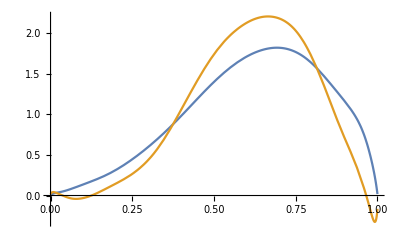

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1},WorkingPrecision->100]
```

```mathematica
(* 29 moments *)
```

```mathematica
mnum:=29
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.01981961019948584298252999769107015832384667689335735610637024779120012238086919308186335751264014891445564632945539580478390618857211533550198335714428270685121087923179781982+5.6895945461005765209067449838849946738882703324799670898161669857576088603789607793448784434137377347939732912500744184846403900253969841150314030854431725564722275312797660305 x-460.6204325263867934804946167872568597539981195137927021544702705072808393699292477238177621074369128234921296385042416470512946138631147134696577187292812123299075816943631563 x^2+11183.96363918877888418524091406318123170972954580486443453225504323847224831250017215927530344833930227568618571509013870864112304014548047180600784764216494255123282424959823 x^3+111770.971793074317556318680716611551921103940219524709722581586810981103194481924307187192591931169344060699961473369105660934852113666330440538862150952786611500621597073291 x^4-1.568557868847106612221286055825849965080387404021175442552944385916944152786808393885049467687896494298285055791730876554871589170141698197933429197205412460175896820646494308×10^7 x^5+5.211778429737625463607946641390308047997490334997481266739925904723575359916812046361723589387371651385424576160738012417535451531399877556045698856770175026609218226570202299×10^8 x^6-1.034237991750038291859709879613260049942814877879560839932501450991383307707285700526923085403844137162639331792500451118300675772907721644180071822574890391996648811305203885×10^10 x^7+1.427907128059121269946917306354215720603838291914639779873763078408988809844807243796343601420902416817698642938579881718926434773509151457102493573111117926341350832515284184×10^11 x^8-1.464567319929810757081094229388136095016054669887774066469777156902087210176599732286091917615232271860167069825273447985553905715650670916486196351600620649005360464212415445×10^12 x^9+1.159019298551836317927866268151613017055219941426721268760020928947670950735801760514950030126148236512578085557506215814507499135410801572580015940796362576526690668934631427×10^13 x^10-7.256048180411075831350613314215578948492117697338600972782795859339332581896769804417142162148420559380186583121626319256600725418653592387668014087708997492198084410521463246×10^13 x^11+3.657594195819163646730316447367727536470524118801999624494088321463838418737995725654025971772425278335851409763722963935185296735334870933914739722852660169795091667012609188×10^14 x^12-1.503606321913785314844130238797305675614782720112545049334859990923009825561660693815476309985961865415977281697097029618280170671516245613675805772995689684785550301261075865×10^15 x^13+5.088026787427555229634754999377211181501715199472655096040436832984245589439769707044127896547242253494611716803017217106734568376442850371048913809913559255640251857100886614×10^15 x^14-1.4265106053499603719787431520133916747245542075243910345145760989891166428802612093243569293980551187294042227052219650640314045708164755687238714495318626384932500995732409157×10^16 x^15+3.3275810829589488596187068080682299315825398592137517770909023912589541779205742402095613454640084701618281831475498573103916370978997287410751477259003621245927824215792149259×10^16 x^16-6.4714859883963907840571689124520254661934975884913151627193810554632345802005926129957983514501495814469974202743171772214662363484493240616589408702999710787442585159265758582×10^16 x^17+1.0492831738848096440975484118855975309671876991564768029332133357751512139532221299777553390392913079617963293792349548459276166487823857485573403336200392419702543242839663909×10^17 x^18-1.4152733874549941618432661567395310286426417127406019489921171303293423802094488159950230275925533946720014777735553111402149311635910222643149691548488393759943973124816298068×10^17 x^19+1.5806209578102020334263566355612214287336660870622646766531715358082705814640050241766824411710100963162644591403766381175770939843696056947788534277175180602105133290939617615×10^17 x^20-1.4506114973054370581396524227407836466437349248846682455716300284664343180367129737306016843974419542624355199678530153214429903209268169051698678354786185994126595061922267684×10^17 x^21+1.0815513634402275376959625474536451075420614609588676291307774500122625269457338690202155408476618045002012871616234683754328660551936978080246719936667907294142592702138878988×10^17 x^22-6.4424841418125309245304830655936539228165379457935795181648105000405521409564894663982924662184981092420745286796019412399725847233772090040062973544278781767096106029719431699×10^16 x^23+2.9913651446050600398082336454221994679602433545527420336269292423141139827209960095447937397701588528108494364230305522046303332577490954922395541496398444908194753960848069373×10^16 x^24-1.0427098370158664094319606878092295829934238499979796252407922909383161665304271089650778602986217154927507102664712421020749125727915686253574415831322437944186112437752632492×10^16 x^25+2.5655693345107510899123904602460575166542329015059544906236291113099650498254453186710376190499249698579836724321041872006033087842925273716902052617278595630436701794976587339×10^15 x^26-3.9714530685736804444263735431085115584491809450109863837597478189291851557865500440646679480762585354584244136449140792014400620654784054321824926282238351758006636281374468297×10^14 x^27+2.9080402068396390123726261508627556125329514117601213112015788001227846161078012728026642924047386927164316254217551280252720971483399438508305757151109568903985996204607316442×10^13 x^28

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.001881575240269194509774567291935173118593852353934102800339971186615529641113042993291393673396863059232020062777499152740006773502203432740234946232892498869450428263718451903+4.665724098517536919472100580604336168210775851291098783143480123787253796613155628314321654790474956701484516234807200585910802781091355320608643953327494436709049827489741587 x-375.70780667867019098142994866077600004706313547895520103456898750789328420244646685272613579930772837848337075471741698779631443147032380213438974086142199504175540253702235899 x^2+21495.42430344277359885335383502235185036033651866350263478000804856382057902884584406716824325448998809229554972215327634820216283077364344915514161476422432038863222970741575 x^3-823075.4892228916143026382403871402565535145067836675993419027078123240240088909841254622606383985030703127211080921182442720474387992624418216403818890397400410453035345174138 x^4+2.238607325034303473314627737599812165697077089167763081964295077800288957678691649767940363699651540337291170890311799392777812134385924848970352301561365559294697979938471535×10^7 x^5-4.440836181222744064666279930758759282269405577584705804604430073417551523615657559589794020070476781415317262643438354557348067692297918135112366688045775118923019308856145198×10^8 x^6+6.59348825084196698232018630813978564147089359442192427259344424862532476459135958515024758807123551215374577281001821194688359522030733409004518443240712733991035013064649526×10^9 x^7-7.509629061600727013548084709075997948420025489156068554069692008741312741586343967081554736451858214970492974963202443711705401147507833604215843480676983815740154229556023047×10^10 x^8+6.702349390259333155994269490316660057148620750507247992449085812136174485006706983647856750246807369318414849307327165772629996701873577256608958495344540619813938241619764574×10^11 x^9-4.770417309286375419852394708977411862659230889219771972129161310659526973872945360010398308570032402826355296678831681093099986329190671697033241989760386077468197077245862515×10^12 x^10+2.746191207155118623297706316803391984209193686215291886883310311589132806815503571378955657179281081281167478293211678059635196037230985786067420774864893563806893553839941221×10^13 x^11-1.293008508365701222562084013548856371641660828831792815075529706057708729556693501648316338450249103181232703915366194694534812574765023434415128843010950708603495131983944835×10^14 x^12+5.022709281139311196150635724681868194407076842103383921728318502641130303721621626420101616778979895516369613710456028069074640431247896931946799167888227993220068833372519961×10^14 x^13-1.620219309053564848487027407085500932187324398328120653244141170743407957238794252820112735225709971012456540663406254444244216559816397831703384730920384815245120830395996564×10^15 x^14+4.360163685267862056513462558694386626417945282691312291138571808503130808801000758162014428452930875080413294474632460051966738478520947674745798606828077622966993342103850652×10^15 x^15-9.81602879850759154647702976010221170565646016066960767357524696017260302740876097374293590874721820448858833292290370197637764914415958973292928450671838221655510440067221217×10^15 x^16+1.850614980139010722842477084299680513706819166152511824561384652505901086019419585334063841763449119677253519930656144626787191964560810543300762113828685090336633292780336773×10^16 x^17-2.919396537314397667730605107631673408177029680707790072982304101513566276181282143123377298655395993313506827546229238452275009147352313523466390696842408871270870165471676775×10^16 x^18+3.842800083750283602928051972177173393674938566377523532103357314689658344469783396680282690780739079781880461702132198260990568924229533795985240095383908707827924595841180177×10^16 x^19-4.199066881504216766621635866374396422110652118232188358236254444845078957592595913362823941138126792947126871922416563888270992565954947571598539019499831895149334459473310109×10^16 x^20+3.77866298240644064026973981493942831812113941945775955687019479653264708289806175725551187892051481053078475788219594613376345800417846504019469848123450412629235552370734894×10^16 x^21-2.767618956645091249330404925723381450608909118490246847420796093836400580545782196645464237568851159327552103001774287746003765124516012652109712470000224421565061099726581636×10^16 x^22+1.622127538358178179980309159939722829556850905710847339457235025635645227121868316127111740612597807182394650499874370148948355412106960756628717913331832703586145268496380588×10^16 x^23-7.421357695217291585568932497383402344961661389835916944596386944148173293704624926896105270389867290727157847178428643232754626358243227545533177045699340042248354981293176364×10^15 x^24+2.552078581295267129148673298670147496195252616998593155531112988189598670624122184806941716156227347456399577023185369044639228894862620671463556472984975036267407906734347902×10^15 x^25-6.201573727989133047013867939228064818346004780461250945713563786147949260392976453330197715760247828298969204679283087235247869251378347966118782928449324340178636340859700653×10^14 x^26+9.490136517663346889721630741325148986697213816258824365921739010849248919384164639632474189447534095460260319221498689553113408280383876357122746119920025347077845175468368655×10^13 x^27-6.875429741266576522011065706001000329270995984710146540678530525572392232771082803297818771617488085085550968639984949775996889514333398888588243896933837117605586891379524173×10^12 x^28

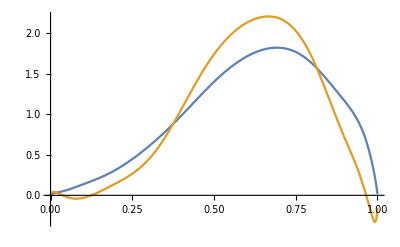

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1},WorkingPrecision->100]
```

#### μ=1000 GeV

```mathematica
(* Specify the final scale mu1: E.g., if Subscript[μ, 1]=91.2 GeV, then write it as 912/10 in order to ensure the working precision you set can be definitely achieved. *)
```

```mathematica
mu1=1000;
```

```mathematica
(* evolving... *)
(* Fewer steps such as 100 and 1000 steps are okay. *)
```

```mathematica
TmulistLO[mu1]=evoLO[initialT,μ0,mu1,30000,200]
```

{{0.6177615584778866663719438815808473207376725120534172446658230420611050943480878634179132934398882077015560305398014763454143119957784122890784205748939484963324239763297151010816186240280448125878159,0.3948710283411916185349012693827020324019253786493359588223402478520326146849358300379529425170173925834131341807073222711288885479708563046375270054928665391745943565779409479526738902335458867886148,0.2597929733924994820651944210131630748603056357051198879032658698468848488817452104621921638173302550832622460687597130546432011589429572865454118481571762956065012733975933397822116721916048811546781,0.1752795052398004470518021345892046435762819746279583008888089999380950911674306448608811593596373286292773715066203152124664166261447506931182389673358117139182078668681456381880537394479254021308188,0.1209334615822030687216197475068048671266017680039848753809605184117647460876141064360055052625916689951075711795508205045690493645079707222489876387078804091039334879988229092502068512895952093445228,0.08513255715075371622183010856168454485268504279438149559384242132862007985191859511174160602039587965459456327881442128440040690877215009065646364779138858181044831901141502655524220849206818758789797,0.06103246079109234085318436224758723205921041362472729549181795421090936454330671954511494700537347283463190301005496822451683480147178672155489220104852539525411197020880820513504177164718338237955329,0.04448715495326339348338788021722948260378406803750235589731889820635203853680277433910717484364493412464445538565558241710118528467657964133475402552731664183355204939249424637156794433196149007580012,0.03292220890417693731716763269739811084642284951212368415115056521913957022761168566914563730858658795982569495688762732100750639960258419668319354519727818079602544987334541249271513496841293592274131,0.0247033342072582468782695033105693015473191722430224327072684586803442201163349108114171387423474486629191309956587146564811080561367429828958193630474090927915243260944159527948174307490838893040391,0.0187720948163177596806573252801401643520174887360112559108498656150341360637971600914045881160455442880065959164956042507552002068527559628749226836059570111023496888065763598719380505124388447936244,0.0144303370584718957682719243193949416207599629704260710996606171601351714718512523560405160634079445372479439090249643143845636841494768974573330842219942801960096484679810762033689630719832878808628,0.0112097074704116776658880702093948120887728217906499161402194739482245404240393717278741975785228936484967173058906425469928311414193491486420405688747047391778030891402046670940872355624606363157501,0.00879104463259858492203027870750101805205354527464009352671708459956864889856913715295287193731113481458824102367538668551980784326612464160433277223888165751530806061896623592233963819830619671773249,0.00695364549799232486990615058375141360073864233519760514949661869587407558351715860750293006119029270051480641587636848382425028235966259480520032729800491780043475903029436923724021040709823266992696,0.00554278206971496057956901294525464055118791155273418440466452330771821375995114493856866127317257019044742404958508808010312706714300116429310132985341699336435922857734373761223100028693117482961174,0.0044485699407146829125901415679156457828272179565330392062929379136272097753693143830026737515845030694728871669469192053667423598778195406326866306227476557453524964972085169023867424244645193447786,0.00359201621900663973952085964228016496075320514089997590166614994171909281439642309714742988844860152228501359798694945529509627185401626092330532862174430617383529401898493995157749411440190175417509,0.00291567872759982209028081262162003921329598792789916362782214233253234231084040072363157576638947777584652924661897359577826376115307594771780559168254860750203724184285065252931484909152479034473529,0.00237733009107491518586917882306399821735633196119635243898122117860417223251935795385298732968123594447007441127220828966739521699859612692163383126334716333511236583616289314022086457716964537552245,0.00194560665700331429247481166679798657723366312246812519619499045802570577301581180140783308090249574991344143393590852099385116245553915281652232164664436605110917984348477746337391149378913543555827,0.00159698533340880056497429254752236077073402722562574724008858007747579010202145586885699619607579805341666133562134982568109945559257300327250036067065271634221067978257197053061810479749627703128747,0.00131365964268420829321570909500216558156227895575369563874214973216450323382484425201650393376614169760485852107437775258200108429919688252096481566690522859560625228270283766378878330995049228986094,0.00108203170764709888372994405700591932173403715913634328047775219701481611184824926178924487853318074246500705344375629801480235909084957601462920429866136526983338271384767453492525672285429904615907,0.000891630747599160415923520601671710400006155960346676271659797773682539584869597797761392088171705456852362165873061243486713028332042479262208955905538655571713873136424115140778712735425750458811452,0.000734329993887184390086602757005848698385734722583422592748318415620636893638726266225070000477578032860851314667333247781630932431989684534640521112014882889232903315064345970719967079496932267293771,0.00060377447733381035248748519964510638729317866892331203700342783129655316600673773448113611711132538194135067917629080255149759455178692497943990144321081766347702723327147807866372179055236117492138,0.000494959237479032979669810319624957080876016026241055293957029063767503727734105442836073567206893611812073441078075949893510693385899259636697299028829373426172637992420947230458450914871895877233439},{0.6208831425333624958880904150134231880476886873379168546870300435755241748249859621405226550472433035788004470668800640503076373592825232625907427362170365665356301582049680073872441643120841179181657,0.4126409707710242706191148160415469653455589187027731188237509667529549109857127016698217660635378495416987494038521440432325565549470949376909107123107961696684818315649422689468373181306415811555366,0.2880687483242609046789376557234533012524977254299320958531150803326365027280277656339272860006176743511061957921611648490084157107520797519040258114115646616726736246273295030235402156182981736582948,0.2090549243496567859999405824128939642030562041305039893632689181110251161972150855921507883896024631808435995399295872367011512350109034936521728328561864040210392487214930927006901897755643884281643,0.1566371854067636915538749190582776313542903484968754706275079420551048067713134459636827015067820804631397949424524418319883013409006760285722124476850828459641694897479781587415620871514194521828661,0.1205698064547809133231661823275406663978253117163179503454481635041885210376847293801135376405858501260290666328114101184727030406154533132851552273356268352048658816817888541557625578217133182213112,0.09497660597523951664568631192252424897439302846743581144404553664220083072462100636232677361768313591590769398300214603057919461550880744037656314283029874740160379999941075550943782186226197920655607,0.07632704628088426054824627672324118537408362137482518441203062312550378537068057018671303719012743090283802083514287833329095434590882463948397977220703670142811268857665178664447046473244255516749867,0.06241761687011477468065273939698333141665030319808921036406964067519334616349574970711173201244359054152589366821387218973487290864297420564170510333473463162620636002824743780615529840938597421281809,0.05182802688768774991710897659374030523663156376180962836229452425385940214487316397289515414058608814328036423702979843169258929233132094137346746006458466550433532513742194628302373131694758599644035,0.04361690514910827720010938605832635659603756824231732345357492039250639550526332181302724083542341328435841560538680033499577099143656643575432062839176684087347133977556281229876798037228615113689541,0.03714476511108075606735431492562495130524051628596983039293365635155752736226582250408324535644269172995054509384476814593883166866151498371228988237189059421236085551497859490298679998598048919974073,0.03196754271041104055582259365506194107470364997317886402170743743493114255329270085797143797882891431554392561359190270532511404115055422064575598376016900737949244901552149484957965159570962306091613,0.02777070545616939145589639907638319170805039211194765827038030544928928619155148932550481643361910133436969683093872022527351000566447135524393628928872184906655544518646173481290433803566281702176479,0.02432742208960058385899503807910597117015638841217270717574087305184004006725250836015655312774530434604918042531322892656739357661746927400529774408696001352196007895592996047206180533554709127140972,0.02147139625238319167747601265494928914024905875058396286474659304859482765475668180437617098740074342878309178580491136275569536432811478333254875357186033473956369495182536551156951413295118930149509,0.01907885724475331941371425409902099342971945991011933018741567276108463095326477372059662346418275226712687236336094105386176062324496923046116639165473698624819900226804273702269871829840131112081598,0.01705639554918330262023102247003060997683083807131518773437675831084945109626652345641857492610033950408044564750105941073908300940165033204805541648538158730680652408139354308421984148960182012722509,0.0153326038526079602580442856096677372955274433312495321006238993198559611855312876558502793680252388889471482701635402675177070668630993466374746108942266232145400050771744009382129642368502611257909,0.01385224131192100866157278048566944789924217216498480810628577123644463058588536996897670656904976427900780691898885074423369846285904211148276543773571585121611797927393182240147037419292554000903386,0.01257209913408053315506825106593273918785062236980422093035388027041977780621256765950236940911844231755396733560632033474548068901826459547504257957728732184094976947368755205822244589311070468832909,0.01145803121191741421381091593594944875901662548822775835712671804873662645460847627083057071708033108071023270377923311452329022220453402129296712851333674568321611678883014095911883710729632957903596,0.01048279417423734511132040230201453586292608946465942909328112111788154120124291984046405051924424095791546949826523130188202582059659412007125975713703589919226449464833939937831536400813173386421926,0.009624457386407810375059832795236559110168038966312423801864161744888354722563748161151077803748378881883640661837789533815790155844099637271869722274546335314140671520370899911511848750824524665247554,0.008865219366432325641931436422828165838865799278745705571308539230620992652472356314573636684666308950854287056333289598005607197185224596611400572006964568604072589668902326274885640455865983748770908,0.008190517447274842617635858687641942092776950782805476775064625370527556023315362504946033449574807594825716382979710734251863507421318358968499558478603251862381056796389293735931564307316238398471831,0.007588351391845195774099934256774561609973727423188869799319769093072173872191268304110909749337924241399085871998252473282308249057171943065073951024349506501673746938847843703833589666750785830702879,0.007048764749839066473826987347951236758876058011273331828906152010635804688941366602788260427366135618718706667937721089416027738621633315897105290924535108269244046166160619387466997837471311811440657}}

```mathematica
(* 10 moments *)
```

```mathematica
mnum:=10
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

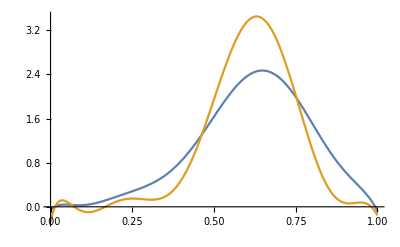

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1}]
```

```mathematica
(* 15 moments *)
```

```mathematica
mnum:=15
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.03906467415864083672360304409823084944820354996211628845154328971746093384447684702995954656966990731152808105921641334980154113574631044679394910972972454614498701276744789089389269935764-8.98364468753390336460970520004089579526280127468881216073016175706368686738390923905172047330281639043692385418098833187752479568595902668377302730250659074600231928209800868953443304356 x+513.3092683318450044619997892804594592184103310346181501138080706344925192799926010152240058200808374723436562863497149819946331436238507455651527383940341738167208196133666877818111274339 x^2-12607.99055875338813647810225274781888561177342642469965805845602665275025487727992634641484147795851846451719619302183118534871873760686954597159324261065212876483076884860730138887559988 x^3+167204.8877248802774769657001194838710204624853800299045165862927897095131058026036840692053881925354266203688545060609612043455505111724439233676575143997646552383898721310919530956155518 x^4-1.348682371563131826001317099531819909931010798936141163619835958250927979855604868368513148123195129765940070190400622334280401679145194785258110693838347635471410205162554986522682615893×10^6 x^5+7.090152192723656841575314789006498429464671033249787384578816694602125696396128491181444763728859727286632986714794149434871218706354163875054352998553357366040126519489799426897504233448×10^6 x^6-2.530526874005868523793052524707614772313532319393415488652527694595451499340424394018720482421617162383680220468875733936810255946270699049941121410178404488575422275249574520730118379582×10^7 x^7+6.272101422801441633080910313746258802228890935333429659125214356724408374809206946784245990191283002852902277904867106200449091187871588033676833595603086711448326603042122380021128701007×10^7 x^8-1.088770558162748327223134905435561024337558364106018439476359742861769192458132236858396133965323777762936433535090477941273150826675045869393157975125688947229855246060209688528577410936×10^8 x^9+1.316959844814035330901423181110771587821586382047917186558598006745133331413350396433833106985673225157920095260442686821102301579061041319438979268756835454323611917528841036654672858598×10^8 x^10-1.086033927668982811522078105015285235163881215752409900779217474483745001230161544802003498175583937056433959295878249389331202125115888380525156219375903095190324246601356482411950479889×10^8 x^11+5.816456596777836494441102381582878652235005976307505216216160252387958223829657719575210267919316401235742296648733301088750897252979988499391153174388933071948747176285954259633978189799×10^7 x^12-1.82292964826364728069763396554227847568195589132679303416138418072147148422561158940708803013518160805446529914797865475324917937408305088509526085258165791000674830529232226431598654798×10^7 x^13+2.536878035272579706614479443603059076188208492687076680460023287921622448200162920265020742361169089304062520749661733242420283111226378203188154549181868359976285856609643400446779180681×10^6 x^14

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.00416146118475535960318160767945679278967791657813617029684024097428109504602402325492529521889132529417220747162716726616628748402740959327088172803443240697779539774206208926763930109628-0.571097587179920446028814369659455297352299382725113850842770259240287151701918902386291047158416519290562596100345556642014489149115349663033451903269545668261241915584603193867241167511 x+49.805809337168772529881887530609232698121845717833496634642302286579337175950551915740228057868051768635124920737917803378319465373498798652156702670415561855865137941081905903257260957 x^2-1212.184284814207413035517290738956079688304723967339924860993127092769079570461759263496378409768985161515566206730799465405121063302528527146825597281914637150000221231448522742892785635 x^3+16838.55380816363648422925975449380482532466521600747416115599993158900042415919729454309884029078383490007971877904390228841127200269473885894490097130737412139707029899757554607205217279 x^4-141908.3672084469612892583681703930933709484699974202844400775128470326798789624095240697478892536389370757264141643842623080426451820092162794081582338581521482721043795370484907596503369 x^5+776651.0592473636635833372622582623173790708142178340895158507068755695795366147677009093878419831774038382303879953172148633768972809478028665842650097921576727172783765912660784678587672 x^6-2.870477942549200440939278020285447821063655296875980790861825773660232628165046282883078413170009474120643708365338239691684684581103023959077392989605245163896670874577136699102224238881×10^6 x^7+7.328635905559805116236004993923966625515544945886725155856688158652653749325638017583162364056575062271438305398777476467061978699904993577655657642219207648392560249641668799729129306523×10^6 x^8-1.303864470334142632686966240613347250680745741336464143966402782990006686695884184848145021999739175681459989353483664964099815630801443175745022378204945705757862872205464856765677914411×10^7 x^9+1.609123110030053427220458209935791730963935085789363587769360917159193297605868901021665446968507250155040150078569159455623623500483106338929967816839294297694725580575267312297537344093×10^7 x^10-1.348822255572278030323674888726374362986059249813905829128158838427466157070736531901495656871933903014648341368199833009260710974979671449593374871607604122360380168076295801701924095581×10^7 x^11+7.322540126694289372772786999581521361493762935757342518831406758916780400930713132726724411472857297242407424118615500398823679203723815413619416715423287854012907156354047116493422532437×10^6 x^12-2.322254265889225880659792345734692922890907665144456636818330132375320001200844739599799270511817481119708770215180398700937666137309866531869395798628291432872244494615704793220135237253×10^6 x^13+326774.0306036400634521351617848121768491354663975071691963559803517255019984496981035135324272866024194103516844695438869563946018148020382880189364798096131501080673977245395335086487723 x^14

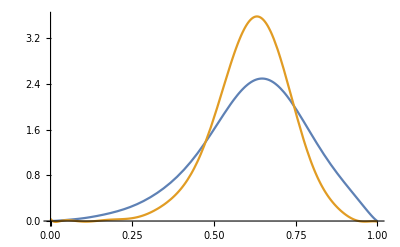

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1}]
```

```mathematica
(* 20 moments *)
```

```mathematica
mnum:=20
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

-0.00460058817178757713442495804211892869411276600163996990283155105544541305583771970901906285748710747969256767072088376958376036030996537776849351881188933017278942166382454517523641005+1.92518809433353005875648201676824437298112312454366614109841321033317665455472130867840165168017692405423467429836742364842117868413012296735286708285762694502420059746482575452820998 x-191.07041694841890799682154796122735559644627412755065778514808760424213064185126820750474679273789715202195242636081562116785132254172295924349247108333547791621725967159848754083253 x^2+8563.75347528108519216518373693604670277828250965520593592967905947091369425233628471031127255173491416593652991518254995988732085985838754909527726256571601170691091510801801272925159 x^3-212129.794462550932531359378817096472110796035740075854434608421569890058389449112320762133608477913407505439136794989445297145328973323194397747673765664436730889358965584987451133033 x^4+3.26911477972774616771249281530924900497926128093890659493297324926069861158252194332270430113885961638751376004024547304053050916452427620282241963613818697426107873696708511511500052×10^6 x^5-3.38075914532948858067707184745325535565619769178482581879574007865329253441341780586731771411036375751179777196958852105333544324248485931279052613332137392481425347158735737677446323×10^7 x^6+2.46689709581376569810729558058740868878656943180559921673087226919614573346097968595866213572834745570166154592222222929581132802360445960336115317382179145958409707907585908104442017×10^8 x^7-1.31395576361800391791382176162859148504324510490590130511269704595799863087531692671509538673223538833192068227057128000078553892297365022178822341215607929617061171643121957296692057×10^9 x^8+5.2279393589272422270486156373342932721945482268022512192605959517438980198307531855038917217350802841051040425791686692518803193536490986469408502131842109191041620094395543903619055×10^9 x^9-1.57755612771900162498069557166217141647382742912703994335508714478844462430816716809916816723014272317072433848467051085888315615176595208368053589843710514758962642514857659537191522×10^10 x^10+3.64215263853144875087618254064946728364191330604975110761485313845990830386800696012035432038831546622593594913553169883957919385204824718927996055651229413892293760475205430445113652×10^10 x^11-6.45321161380857444708098375378257483591251954481314241041003342251291709839642136950715974239292741778203183308044488128835711621277382769515115291486924009848282284337209973758020787×10^10 x^12+8.75048027883205838653889235006645618874788079559082642799179519412562668048050864536313268623376263778670195465738284664638737245117503001876210979995994832697222614120220263387661648×10^10 x^13-8.99447159972522993406139069818066699543540135006986329370450434003800388104342895142744363453443539678144060331512789291699949186224177442025275972749497046248429496191999640263908413×10^10 x^14+6.87907154093600933829416963413136016896730629030806501252876090829850313848594135826395677629867421904186066494008789575924075856607127538634751771503714672225367798831005956692063247×10^10 x^15-3.78969171713566200421451895350019611760709758643710164607650006123371702378168700197687788164004782587268703709024297902770418667042302886119591130202381216246633013806865584187703774×10^10 x^16+1.42030326758639473304167963039125565295215201109113665929418914324618146039104742739767785497508219294020930159977839616586602900195430260759557131539619409419293100680158682386541043×10^10 x^17-3.24013632276732994016065248269081020391700064912771485317416237450403296661604719905964827064134900947529804397461262368595820359321779553600188996697830597521877708407560001966326087×10^9 x^18+3.39438574767381821494365503943785206511232909441376575950928517061694280465888822044692891174671308791901575424598478481267187196625786187147025743800299156490849399035837230925528265×10^8 x^19

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

-0.00069405983807328701170695480473958129844915969904271287027987002801538262471148659163418335252318800193163580693606544846713929030631782215489314172784958572928504713875954011482661545+0.61562839068063066550967591076989484985941153672049186635937250691516310357964838217519926815192994382246451897511660367072577550317766626407672655485951007540700728110018119670596061 x-24.753250315222943137693885335346136501180003880243018156962337501305586765520379268569618220162803075421781415420578242725955451559111250553334016402599289100380354913102621522441766 x^2+960.92922120755930636308923746761532699776242771349771974407217148749932059041534189927034802445714906283752593228843775082891934118455907742756329838624657471482668701242212617263325 x^3-20977.799948286257487819566221741461745609015742193698493965341243981969974266993168144217442930313568470433276100312246089180091759554780137852107032837862116759667344197248079771614 x^4+308739.51873120193248726001614423124761846857913315130846467932863372329593381452656788721807524479636236863381292208542088262147923105727479236314657228729104973361471689259345362523 x^5-3.1746138295139024314874228672785801089767906877174878184523664319789327865008910188259815462899884646104885138754589490196870134290794431560208402962646104041268137088285983916450124×10^6 x^6+2.3406143550828838553707583857255096877215564454759189413066639947879655807671371558830921984005556657601610814347006949584371424293735143086524922436548181888738931581730406956987476×10^7 x^7-1.2648698988734558991574648393311082949544506653551780174503385769004459443472471263649920339413830851574124607286295496777382229537704397286772362772547360367286755704228745781676445×10^8 x^8+5.1030207161336438961760752321213412297180877775245549230463085151909431588394180667265672592696073393424854839816207595296093866358584513724056948604815157230890835366967814824441073×10^8 x^9-1.5583489986638577115219366427898349140903632267751584371770599064402891399125469660242048917152410780321955264685204290483891827600998974881227934934175382553432266107639710206880816×10^9 x^10+3.6336480648705869463598478318958706000993946391826044503333815131532416703912137790959685543186881794403577376786600687574440917972853736556774962142244544038058369375600979226537459×10^9 x^11-6.4912856545152760297592685561859047405212510409153102366617669369740680462037650253848569678799849211255796573613108393642461440350120004466718135584187877408051205987089602661912744×10^9 x^12+8.8631203345198512442530435184480085887772433273661773461898603017825835389410648437346103505682867064730077995805077554899077950173243804890664018270699803236832071058240016639815891×10^9 x^13-9.1643126942815838887949768463962666547275500292390667806408679312103389174750167902595603270052992466702759971031730838842209219263893114172798859807022892714648264114927400179455624×10^9 x^14+7.0453526910482435389278607976057280770073988793376384887774235439735085832055032234170948263212749429570136791245380965802906939501779040061691821997278493452623801744537339048859713×10^9 x^15-3.8993335293170887533760419754742144526555457515032658507478911702345307572826502971864323048894066058225898878887801927717430028099129923708950825418854449635729071000065283789348036×10^9 x^16+1.4676243977239421447566250956428902331848324865882002795017946814193111525350556452138326910254360619872562038658677811510795881607897814400554296488107400721478028765732083178241973×10^9 x^17-3.3615167486724709249968916832336723438709790290836722604368382127706848605804786626511370721044450453786855280604138118694138607488264686996558523888597841830197886912485153574873035×10^8 x^18+3.5351753524005577451411037891762867606865251042155040367288261352368901035201967933084386851285826210387415254443848729375033610306308229172864007356487446864457295364627397273582035×10^7 x^19

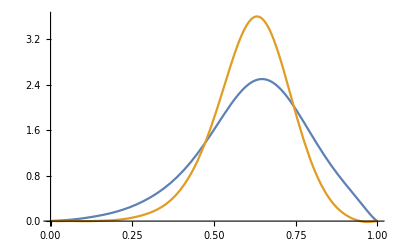

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1}]
```

```mathematica
(* 23 moments *)
```

```mathematica
mnum:=23
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

-0.000493093342972087928834689953852753147899044943171082792475699855028602228043227722065378927302581494949828157677042747484803717186507172668659730379095399263624978806499941763337587+0.309165563895385577197801884298458873189533723208021084895874560440525097777286657493235886733395927838708906402219567052616482813052928907026390865039842306440916708680350152771955 x-37.3482887966296028380121502955628662751443733157634430372910371077444937176629521630729084074419942533998100779978251837388547550186077582953008800278399232822702750342010739211207 x^2+2410.25122631129417291073947305552166061050935789757238171396359332868359332813238802178808719772281345923953576864651665444059999342532911510710924064649739134444602525112696206859 x^3-85883.3415653874456292613231668863379271047789845927115165039447332348969491131273794123208809818057557804753799250306762850046381399276117557285695373336419218023358797034025203059 x^4+1.89145208430551067236780512551630688895160045741275414660450573845604397897451090680844879365143585218009981878670904550156912527250531110119959507606690806880612301862667467070825×10^6 x^5-2.80072465275923748095582822671970176019033872838415118213344317511003487873440979865536951706945364169374175033634522542623032323807960312966487465212467513752900436208443182586482×10^7 x^6+2.94671759272196254056040734104487367291090314472721306284963483030918730967056554008671023384471142413857559756784464155653461153329174725595607017069072534088394823479410585147203×10^8 x^7-2.28674398572622857449504989066026446010411895369667196267809693537421857058888370682369509176537598543038305572798985498649046428273614902457120487425400086185698073225335426063765×10^9 x^8+1.34387965353239404956672926820208175181986542319217909894689925324473130614122441021762665837081578956981280979309638518399325026724022931229739526309911764607857073001072298963725×10^10 x^9-6.09493293096353890979682413828318473247836353123620509180925912546284824854103876537643041031259730964874045285165274957714946615507036780876209094754309755428548300907944738779952×10^10 x^10+2.16182020854462164030443677669243646057838040555707161055814321908801504538733183843745478159973229025893082254021690581968749389070042705442213250017881103198033734205843002062976×10^11 x^11-6.04965367847336256126052145099817224093816054305712195507907696149243294224506849378642450070617048072841345119021747424396250808015823526090013015534201150191733449494391668170366×10^11 x^12+1.34217620691426824078645277239249992294323436690800830227187972920177894052660324309422165322285709348279013830979075775145795838238878072290689930606946647630869779625468006725082×10^12 x^13-2.36338579077299900450365373926306438266477012480213370134847589593796613575314453837258145047399400068178798297666716045309373381370378341612723124017641417782246831268647434383531×10^12 x^14+3.29362795637142816372614728613321438359017175033570985348353838536588316771147868974832773892973767430606519562065070142226218837391829006829921372289049342050346002116676961883176×10^12 x^15-3.60590750497746964266178742426122199153433445965197157887571784025789143630584322996741738153491785382705827279385607441338643472579319013443233319117977445009315724941087179989221×10^12 x^16+3.06048058223351022948337344365310502004551141736673139992754047858754634817656117260754574891987789684525554396792151407575835696136516093026432015785981447186700168259027624801848×10^12 x^17-1.97059784582876927786865891147471035658507480059989976338721036132231613754667854987627931272206827750826196241957048436670178957752621642897766201054137122407764820150939228576553×10^12 x^18+9.29492253626104627815950346969289087196224888789772941335187730026715195405339161075816148780229009475187513547602981288567674798122224434698140042592180004596796647781235441860707×10^11 x^19-3.02681778855207698153806902811865446977328473303807176429215771416198309351898947215361613372047433328872386041233926432342716235404177764613308393367463767467608876687767932777803×10^11 x^20+6.0775915546894123009794431962204135834017438936164756762988411473603458185391655969189723983592015618302059678929307912650452938066664606667326249859210150437741082298287252748778×10^10 x^21-5.66784295954795892317692887412921412454333396585312166251944390561394474741792647180279924353390491597881740330490292861242949043320331981097386698343350708105690493027257658346839×10^9 x^22

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

-0.0001225080785411958734517378985225362364195638751967169366310107520973293879632567100405183810028270400268005883047922588814436122714775920387523201143586082492518083306278560429986+0.37806069043509333271030764868311964774108210443454920393726950566793362237921444721451234520670294762232803172342108095714925939229105149762403082262468240531416151044351476203875 x-0.3007503482571610785993337478460434742266044872241067274062926825542496762943287959290465655739941039384315520474028157940587687138799394924086930008845343763276444739818971673321 x^2-139.9461115543145571635800280609391204286091076401626976369570728816149024108113610175181237455313897017255490725540413392730555694901143096592532913363669660228105129597269534473 x^3+6259.1938750239188022971787983640308619577305180000474841594627364740770769870567532626701137703272662094340315344563193678312121455874665036608415928006988269688053185947770964903 x^4-108955.55974086651680095935791727249776766805809298344968761557437449651411452331679178304071589601878397506178454750148828338056832026667714018732722205362958104232603048472512038 x^5+1.086224606086634433037315164588466434377490461695052328868163485440336955538010835350498725201112831295686110254152964452269523141502776545404664840063128986417463970626601128622×10^6 x^6-6.717382942840789244658532260960338098959019158498220285537881724175031789687642595663029909487468049629771228909066467605792453691359358571745194886965332631426820366509407588822×10^6 x^7+2.372280630644778932003130268745066427757959578916156682736302780624067747943718899889145050575699094918971048101799700992906523076758423049412909141036398034650082512843621955169×10^7 x^8-1.14450137148319457039761628988544452380755959196668050358677534773499141197956097825515308473850818204811603540648564361779181718156981209564847859059202162154854257509355323034×10^7 x^9-3.984899196280390233363449416907406958928103972540234080005587959760834563320230716550753758258060024849386383809682299951273859995650741631682999368400099670782372944281605175592×10^8 x^10+2.676102577590310192482041143661421817410860600549794513348004614644289848638304484937621161803767164270562306672416521657640361080766195938400132171234954693242186152502102971369×10^9 x^11-1.03269028045574164554748826731083698846350056348216063266352628761753355752974286323192468127582133313708540854968868602945240720725845733817272746449716326696522387173207991841×10^10 x^12+2.8023301054940906978823947320547729805634867021130782696607909534029259084296498007597364415123055910594484393853881667030800819425885891942492339338369599401940652861760441090512×10^10 x^13-5.6689562356566751570213682744267055833240618992043446110809799839785151274449114986529481263708667978755724081265327969693400887601586175842740605563065486703494144332984864457718×10^10 x^14+8.7347821815657752104867682281392396376963524464626495770209328402439799976746430248117907403563114283449127400688634894622633931651565758491427988980254060788545284979354562241476×10^10 x^15-1.030311157818368216003201866416222858721681559965781362042801795980521290974456554716015771531328294206816654991346619499637594119718494140387839573408026840564773569987241701475×10^11 x^16+9.2472682384487362285327585565173376778920702105010511130516318036638361296976042925615712006269237485018502859336432439608231692574025768930965092101170417733462629068122620885196×10^10 x^17-6.2079084708575247459623917122110837962201759411301108635121396312023367635290585507928283275776605159257037534656691815080264100317138811068184390681034589089204158731281942076678×10^10 x^18+3.0190878155046427447698691556427212370857134938361013009957232253026413012341930112555033283717974964679653368098434866245059951613888108413693938951184334685005836595060920084688×10^10 x^19-1.0045445950147383595448730611824466007258931088468548884139102798241352467398797495211672481795292107720392912017809084853471300956549074099397808344807899060523845738914415125852×10^10 x^20+2.0454836940400268264869059226413187563520652778031192416009473729293659991476234881063895819379228168007550591197578520496542933301647208625714202875316552768539132989265074327843×10^9 x^21-1.9221195847228467236715307081889376911610427962973389161584941129739472550774246424643485423950227881434990737879196820516027922538074886998609733002750920984792191528519323351525×10^8 x^22

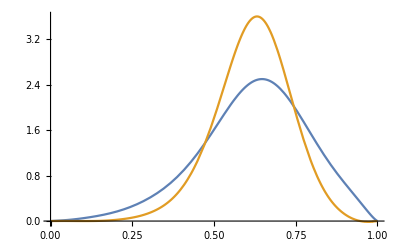

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1}]
```

```mathematica
(* 25 moments *)
```

```mathematica
mnum:=25
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.0004175950768971513821065547291408130879357028414204624890070138603920786227965036238436543726964911085772034609824251504255248712240882341780480255417109921477161597058507905260885-0.2510291406727218264512606509542212059866499409742407260311863920342488389215373454963523159215494855766315816881211421698106044749078938201099327342507977378926312519769444463198 x+48.30268760152826076515826883771537216089131357245687829747029109192063863371919325516574261593160053147236222297118677073372571987282908884898996452544988060457849483213048975328 x^2-3358.938486619813015642904141090998923896504421295490974229300033691163569440797691161114891406333388298248628573607356690288823453599682484257837227941353497680999714975235308287 x^3+130100.5677458537280592375914928223959822684468217214351097586633941009763737343549644479259601874986895531482029747554225618238740937314463685329567786833290337209890273947591054 x^4-3.205044258713381022603063950329136350206652520786665930304296438520248468083079605341101880417049174015752412872320247065722575743314160495191426796125616194292923108619636599917×10^6 x^5+5.395328590917861368280195987962768718002290937682263266292991226215087326147679029977808627961164346311101148493287998081404005345365797259862960461079085628064600490393531146857×10^7 x^6-6.521615622923247196748741354201675876647757983578719408038985892466784677634653595897430101901134602176441670329739381058523519039251597940519199920927520217054279553995942608461×10^8 x^7+5.868812584638874201063289280681239148572563367590642004738811089357207499239906586919733738867552495833123404825100775032547625281099450520453625084297124336421555794788513484388×10^9 x^8-4.038145833304451403423643844807491587922098978418226299705287562314071787262233457760592547823838630330704888306586801488829584132739251674457483757802240225292373181022595701966×10^10 x^9+2.166928905300108727928311067329195337315204247054561265235182035118741813988889027518405574538967411043523565509354056055756186083610310693923352117795815808522868519887274147019×10^11 x^10-9.202155722570542719751911001610352608396933636279170779637778340375953345611069002953704496576067418625652197708833099808196820888114031506817517743151284796361208187523204931147×10^11 x^11+3.125348395045138914229269398287612546872256580910070867402057085802582291704203627464341588954506411116223633150869778108137977729176697801309028082256034484668744759954674667079×10^12 x^12-8.550181050729983901457963450970864658119229479930982704192417778132810532083598751831488218059450648982337429507907184804183251610665449059717711642310447771921078583485557463743×10^12 x^13+1.891947049042138077594077649677887378627920241897497037853879324643893138775746579713971713892549397817039104899664607407102897164400543963688352312967508000187408695712311619051×10^13 x^14-3.390234252388831731871106166750463467624596184533138934561485977708525169097892210487075863713434427308994294415394285003029673832573247382729624300401746656535553449357725463181×10^13 x^15+4.91093037202190654933673627379579541547741767130325453711629632630220766061299831408564421192501175102683557270810837212655058572578974693533928052144507808637697184748359241188×10^13 x^16-5.720942646244406470698489878960525642851623091972375674685562115575066862728543027614036405386319019519995687331186585109614765611853189586217713984446782551801745029033016924678×10^13 x^17+5.3099768264335424077444026986984081240441063898524867206856275887007352626627160780835546363218535610723713830057258256969507924528049128477992769477059686994308503422492650562899×10^13 x^18-3.8687909230814502639753635469833736623468602684006518930052033537759650956822852400504451771279911169072491910385854191401702587715074629182415736252600855187438204815092292216646×10^13 x^19+2.1623196313811132122857172905801959707729215774664257316283016032350949641946186656428255243334833738773259390557076154669560403845506316694700604621207255890340089060247322211885×10^13 x^20-8.9417250100550790504228179815582045313492272025564191216984049286475889247083480509629186395609270585071852687983951819090509788867226136189551787016261417551899199957364429386948×10^12 x^21+2.575659913874444618115298173847008762701609887163814379234931303600630979955619277487239414788673088520122104570698486607231966951983664851566872740778159755477622193943519059902×10^12 x^22-4.6115258485772132093418656974804397826014311586490094045147115439083151829747939381836803237681146052432802843205047608507642201218576206591258258996144440204709562420953709244449×10^11 x^23+3.8626379089492971873224490072742839776201133071221191356231876152008129281021999931386756473476106800091351459766039557910362157244206398723125633849446200472885648320708511941857×10^10 x^24

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

-0.0000365022545840388399358153119329124370649048648713763316735508346064824421045395174337904994956591285659430744091845767147914486674748488681417171728854494924367423330450522288166+0.3219494866941389505766059900392317330411730552632504922832299784185412400334402649492685950798707533637339567551945187309583373548058283279248823888424727874011485656032920514441 x+8.70993850361462140972150294265088141543148109458607078265239023340393313101396505749146300709675867644836285076141774083703217065169458726953855815752318570937611256772597631437 x^2-772.6665914366862344630709493870278190473678118046967538318163093010451794307453645234509678518162794627916582448720010878752189141562013637876061088337276265947670314293374961604 x^3+30808.93392005878932157799341117886829382983042402942641994044252023438073301477442037931775475556587839883682539632561787763497101268115856541215111140234808197993676794186626212 x^4-706530.3968278020786244039592227280057519674745172924922031242068172143640061414562955993633804657631177260294885732496130821917025701241779395595271260026238435219306000574709349 x^5+1.096191235436342896726688250796085866436526132334537339206558982068455636488264103531119527331943642042643837044514293121896085526656182601701435377594542887286755106605014703334×10^7 x^6-1.23590581710502333703784309833462253096847954951058067466406077538964703886381044492775486341020540281114683329572257403454046834721741015413207497306286668137277843454058608261×10^8 x^7+1.052297424976740498690235267589401723324471224020697759218432943165560653753203953052926814408641085806472966905029232446904169333620194801477380619910008365502500873841425162265×10^9 x^8-6.931482094133580871079464827268358282681498731816713043232352688943898039362731214635713213825284842387365915437910437941440462997704391447416293405458723918771980938652086733601×10^9 x^9+3.592692021901152789803105544485741193617433614701555748599738782456668683705162599887829656620516150359266876928226259367895077273636686345890784646056609570379444453689571567882×10^10 x^10-1.483718237290395368419976181704411927606364940882437646986147009870948558257735057877297386016751886203425649013179866601194075645212855842302931761009989008002055690204122580076×10^11 x^11+4.926878950487744851249201879970729888237954136848037939722133502281832583221115310455552532074209004758756578819113295397364045016770585891633581470208602923869321788137556000802×10^11 x^12-1.323600166026295908189203307681148276259745269913503167207984448902609150867119005776382647065859072393926626262559127957235778288697729566688794279168610107700620003563221252567×10^12 x^13+2.886655445937515951362205543679152384960112051914128440449702029354571028231600645523807077359791360891381952177716976149761321852320404669790168336067110156217709835674715136914×10^12 x^14-5.114434196703672714900258683012717707988254658752445557059940057560843647101150406722162936063735487460733940205142837965806082042869554185580302793943589074564300831557138033297×10^12 x^15+7.345547228295654434412416497001589623354721302226882358849209885244958170267778100476092329729807800697282783614025432057880767829778424130676710530995797940529492386985858803504×10^12 x^16-8.505479842128447452419351600451659888324780942796457840616907897908468833126262595779620898145304263415455291328773953191905257237872457598392372594845501637972279248162835776501×10^12 x^17+7.864386349112560936485553946368382361999299407051195870435542514268180679530235655190314613724038148785188910777277354889059225442526427953051685976784494045953164543037168914524×10^12 x^18-5.719627707891794966099123808931433398719334519868298383236258910731918248220819227981753809743874687572394821553113960060275754238928258323440767918158010410971919063332516077512×10^12 x^19+3.196938223770226792818149054061414322674294513348509648853060074489275991630907261022439030729584525322473438545594472175628166118479690145684213947678585168264468647016924296275×10^12 x^20-1.324315998168863633645297701013477592370121136302936895993324366184509047084631712209153091098323822896171996291294823652804466679949357167823141156668714459823491351818775176106×10^12 x^21+3.827275686531159933808379488952589773762684194005679368594322223683393238053942906268374356518247656317488894802872769633831555282116407997504913169569255353608886136148117487093×10^11 x^22-6.884928048168360006892260753387974353814528807367281467132576936846358525749297797809527731154684716714836302369916860317002636371049277904852710712924086295577662795625013026337×10^10 x^23+5.801873916547505063028994438302035458494702775015358032775458626211244583551497295253488971348445139507010254555886289320274277365936393203673448952858663445885462029117946599045×10^9 x^24

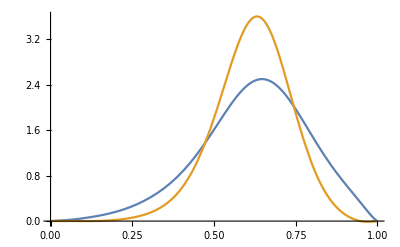

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1},WorkingPrecision->100]
```

```mathematica
(* 26 moments *)
```

```mathematica
mnum:=29
```

```mathematica
poly["LO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.0000823210276398917206117834866439238236383319394460825996746502427828224275735386439075706576957421301647561052959973513995690074085237972055607727115345936446285678980381133244-0.0514530695701093581727134466735773444294136424647810607027960334431392359788070005738320400670262629150115818303042153029073228246682459058976179662286878163837355233259711722 x+19.93104979124983648623530624024117405447351541262023371608603772019206577785813465536079302514353992220159303816540927714554077106675705315848053280012954745444687142185616953 x^2-1700.980324493524753949738341503429303343706859469830753355312155139288118482541533350220263361653595738845797721166587862262242900145714242338859453280398526788477529309304466 x^3+83314.83358775227080139746181583247527650509170396338397128549143449694245362080525577904581393812093610325860540004799647143088356142353794578934008615877952725915751610850156 x^4-2.657006068591068842632794960737415813612462479283956134635650493743305724219529633406480958119445580663230375678571644923696288588282925293626173001830245567989195948992774904×10^6 x^5+5.856383273328728088945409563608150571286168887248361702159462023197192783916191871396347615490830925808996635554915783463750593019305640168040026866499170089268642317946779907×10^7 x^6-9.348112739253726467381043951698913349065527990161126079119153017529281017347990287403401108146493164887319376093951612969796207811104860632824903730459202801006344782168562885×10^8 x^7+1.120471777754659344593238523225821954269471188924684754014393887487538241926229747284957664006826368031085931111466200930829527364683979043582126653555825289541215562759539246×10^10 x^8-1.036626215906299517891089448779048691591920742861675378004597952474815794794059222904234219635321973551139009464796120068113751674185678230202880072290404214943705375316782384×10^11 x^9+7.560490366447384158132206345326463830556968127292612755801427180088496858439515492117737058830688789880708937352830109114285922252884819308794897056156891892799982678242690074×10^11 x^10-4.41832939955017171596917037035228098069107336223632991147289268351547488373813201024205549152104687777848419835750657713909493366227409793916288083627109356078678353987921674×10^12 x^11+2.095147137709785900067703586571236131340674885678794835656514785018769472309461989374368597278698628887570214834220047419315252954438144541184291557623835400017318283457708598×10^13 x^12-8.139647882979809725365987537155619412947366759498599612915838250577006947718749373174306227069064869956764515472416902373129698622893276454779780637192393046012983798346517624×10^13 x^13+2.609474828997631263390003895697190498612364659423868647005815481268067562381547953714735317097453034888173318077217860384554153293371708797970695513691088334821478962847864485×10^14 x^14-6.93833234316984560587920766299989538029757883387736526371643797322214496896722258251516164349232804505560644075250874257326983704956927086493445391185813082034439758504591664×10^14 x^15+1.534859823312931662802559598915617448711372484413900294201352209286483259416963049236878107914939999750179844077960584561472732177494904404924225610705447995466641760018953497×10^15 x^16-2.828417558475214308619687872325715201862437725603569447694771324537310013492793669562155325695058723447861412277773731276940303461430400282446410067104128946756322188290540522×10^15 x^17+4.339175539812482974700419447276683391916518417075071563171051997386866532328971687813327382783466623927909936488542525330259516965843843293075377708441829696420735779643500826×10^15 x^18-5.527113496632564137676550067070356339103059996561868886281841601150033601258573233892315286736077113225870358929673517800273660432857373027152087434916304131065097795974946108×10^15 x^19+5.816097089926981935853988021447592609535883544367220062621511991961510872628045131339535777875119181308662129582027900181046824401239722979150618972230944499368038306540023959×10^15 x^20-5.016100177183431989372495479626518115988034693161672332050831183105356789954504868264357740542173198684074876368605964846584019747894691841900389608822681580040664433282217688×10^15 x^21+3.504465027466574047686218649250129773225509449049366979498130015917778171754617156389470740734543217835709235558501235033243372084153888127197287830564703174442229181682018776×10^15 x^22-1.949984826470339982381186862334042334843452890935836681055793060624682873023752201071643459400367504380804709630238560179790232241323904727769805415669726508157668175197741959×10^15 x^23+8.429379463499529266024865831558176223761635694682066655218100770227026334690112763470525340468837733731792322920452427223385041856566199295845234920669505916512112975266915271×10^14 x^24-2.725734784582593523604080084722474230309669093708975489586166592772188283131072097297848649531529212693681123455337738005171141504251576847093123016471780915632144025952584423×10^14 x^25+6.197796179371866025692626775721824412309543696114750989709225463707752579483138791835561763124601003693164126282038068528814339881608090052277003293116604194391905730183117553×10^13 x^26-8.82990984065883689427321608658922578190585670188053812693921193520151694839576508002333692212944515166531241034355686675541217363413299453800676409140781053786812513703610363×10^12 x^27+5.92434357280116360279547029492940929944891591861368950863223828648686867058759600224490100402595455848727933517183283504178796219855855320012470220981800821370616370411305717×10^11 x^28

```mathematica
poly["LO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

-0.0000417457824795761528998930858969991654025787373462479622451417568326333121889348833629011900972036130585836208852876000697582278027224707589463255887563467817425676317232011416+0.316322412957362018708141844555076516709560345938346791069510465196547548002718777901439542881227077240504312813099488417422000352077517618611794629993978968637412215215766853 x+11.4382270104035339935292748077770196417671982228131133349411082016707268087748643616357157365142196911801928806153697153806783225630960930982238208592247260684536724873386955 x^2-1130.311452274699135918479154134831992158379346674689686255650827427018206398616286580972719262418213308958720081998545740452719568278135693497321915212393767762201657757686 x^3+53217.8608820807924753152063658923683141165594368588227399984955866029659914127265862099967572506262673640371758375676744440939520298159125228748607363404844230793343847168392 x^4-1.53141667265667325679168578605199899741314343705339261057666366964366408178136885678364741018842369597310683613258992899995633985408138665123118487320781132775349164533501022×10^6 x^5+3.08900754508383442611578044252706930051300835160745307275470917176976404871071150396945777158392005037425150532763464105315036084745788704921417184194293615507486352530662353×10^7 x^6-4.62273428644515970133424744961968481952651479491438373730275743359498233368275633602595525799060264028147489598372843619201649009825300936561106338222020698597174426106110451×10^8 x^7+5.29794701001999638677040134423523556247372815343207289136051414595172240141255782698698370798449669735657727859075791721694370299925751374833381979567150909864662891583025798×10^9 x^8-4.75483557298448861332991096602493814400744775491260526405319758548668183704548666103468692762422587672353478716471439570675230504259876361233134501089865328873590846218668766×10^10 x^9+3.40061911302014973231418465706322556530577975847365942085616264928494651329433342863873652162287052370348699267817655437583068633174226482813109308490526089720543930836573882×10^11 x^10-1.96535307256533377964196587345315573514432660915242193778499128956953729812435217416841473477198310847139420731446552498448147775959406017452413840692295401037451883339248441×10^12 x^11+9.28137404919114842484261558299923592290294410127022810293082401447802609456712777917731466393981536811905733408573833009665260393664407527713621480975832799448439011235429931×10^12 x^12-3.6128176032003990108690465565794329632894502250249352875021193330586358235635891074520135923718515143350619344060926167171305603667890597887974211003933125499080998006977638×10^13 x^13+1.16678479295642463509959264613213189363182348481524276944206338533830824624916482469728411320650553822975440545419624554225779766010291677367638905639238934243213147667110579×10^14 x^14-3.14095978101511016455099532958163815265149963470367306890049833074808813990412200558497450313058612687243354040946142761987463428030772504009221577594802200999634359052573258×10^14 x^15+7.06799779450801635490122440328167196409243476172447719656519227579580188819000408648123603379110440584363414603812980766819242022300891363179300036852029977195033047479294332×10^14 x^16-1.3309519377494960730977562702179949844499816600436550185540856543269760023890141641756418937101641564987026980994638131948329838730175124335324456146345321793728606338554845×10^15 x^17+2.09573945007923260317053332588106775320979120724550362542915057188536638408092025164180822455264992145134403688707972086653952077922227480146828159912411275136912316602605402×10^15 x^18-2.75188582288152432099867498218477568603949378841850823022946547208096290429748227833904143247947807647002054484392496519792350572604635214566376778869704359442222120545085027×10^15 x^19+2.99808094106749008522059122054911886746614794629802891742814085154833270724200144898017094651469523699845146944492372581250001315232516984034019987413737750421968689037016702×10^15 x^20-2.6886582260137292124530022969941516808663398483086761674191482159756200593634369413498731261870632289936110860013561927011683719494420548022727683094502060439866903503786054×10^15 x^21+1.96172913202212906626560327291528077468003936478958126932094005216866932034909805742719786797272026488027130740595122689042978252532433996472062822661207010534182529450725445×10^15 x^22-1.14501358697400542050329776378659040457772083943555002697768264804725311853751998535668375885328789623211127460460188863451260847617939989001142917322936838725703774112250507×10^15 x^23+5.21540360375451062799639574918718472656181104751813644853271534256152317923636993603637230036332223975973892047398161146607064633300299048643944874705630557699622016602589256×10^14 x^24-1.78521612268568940121977987105886595718600302299748369226812632778336529138790974151276314397178468966967511134740000117307623462979917147389644573863715776471818993974430466×10^14 x^25+4.31747557163613846513784711502026815209456972509497435682659999516348540807581160207679861326666360631514583971444695095915604343715311854487094357672691858245942615661919637×10^13 x^26-6.57498220301103402334741457490795240005329728854735333613593219693537543053810090695461541187848386432468351184566071642930127151602740807332223813578493743255482186734709723×10^12 x^27+4.74024600204263728611828609829935721740902384281098016036857291548053078200683200858357341540113528673420039340840160944668926332813108523166687196410165717199774188455560116×10^11 x^28

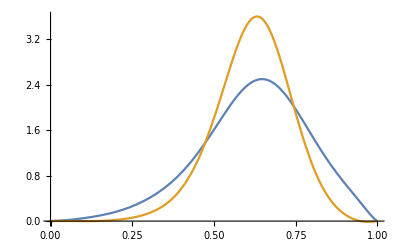

```mathematica
Plot[{poly["LO",q,mu1,mnum],poly["LO",g,mu1,mnum]},{x,0,1},WorkingPrecision->100]
```

### Evolving moments and restoring T(x) from the moments: NLO

```mathematica
?evoNLO
```

#### μ=10 GeV

```mathematica
(* Specify the final scale mu1: E.g., if Subscript[μ, 1]=91.2 GeV, then write it as 912/10 in order to ensure the working precision you set can be definitely achieved. *)
```

```mathematica
mu1=10;
```

```mathematica
(* evolving... *)
(* Fewer steps such as 100 and 1000 steps are okay. *)
```

```mathematica
TmulistNLO[mu1]=evoNLO[initialT,μ0,mu1,30000,200]
```

{{0.6166108849458923467531928000591031974065053963103037399572548988479372843980991664289083568655745584237181732422383375817119667848711424784965118322949550611005011623349350367765232961876093321019204443,0.405191052736639659221617080109135342357164212857739110084482408877973633282866144139252755300656010235454294351805129771240232438901817064199868111698798711964672151610657330573047174043298774374568516,0.27939318192408842372482841299257054498991939304116568632901561059701305359859667836062036227385426030465922604606053441003981475777462052231041762889453806134208675242970353707538265676894736146465027,0.19999225296323502151734560438672974666242370693278381626957108308772395440139257939156779017147966696908091701238839741765396539521273759337812702459640232756672909152598203645949644238880105132972345,0.1474630792587876893277961750414947635509839890535773956118441876155812064371513424444415543008696952030753332416083613294311175504995106497621833294687483439431461186773973999447448651394243687796993,0.111354360413984725530643551773841009646508665161467737970219343742299084818054947896412560730739154115751400508227620914071577729357326507687953570713526174258436316829953366255721490254855243685878,0.085730278455109091898196897679437682319556646127383394695159998281836659868216504959831114221928242030032060710707277591711628080034265786706544440809652333995399888058765656420524858430332527442054,0.06705123480451748355733265564176637705030429196967904323832257123302674794811649119629169192547502687881775351959822340769455429362791983795356377175533115740717667190402661556835993061521294034795,0.0531185502308289750922644772574336283267691630787942361383963798259468932506900435825989001549659831956944788531264926802227326006992513300184243095492458130472397818572978756781588413288567689104,0.0425180892008723228919592007952190077392522749149073098300042140247047937006651739205545470455840727662633830873570616673746493250251046552762773307782543347795135770616909405045247146641401239392,0.034312519978711225675949929795444022062871019148412992547741896178244946557270086460738177047127313236053445445264223956936339127249666009604729637551578510939242495832304939465073469892696682072,0.02786398592209952752955534489529997028236051560772039950849213947440176133124936217723009321979545339285646846129367618832112766147271429312217914381319425740240780744336050441676937929348516805,0.0227282321163841879192706781261686253220925080975034181836631563148235174117114502703604872709812638658589676123958056631662853136081277582327275529762898579465390806882680414933991867340663627,0.018589394805215868168452949729994326987507816556819918248668450378305092829544728981354602689521228737651547158903307715509005930318570416079732262225559897003857160269733977048844531386086776,0.0152187128246631451352918223965172976609845883501852070185609964332746391401340496012451634815993864942974266422093255580537797712734309206668670503455351276380706235743443411061020168663455,0.0124477335809134841653765371389732010444973110299727154805596260298856114917065235300490335866979093339568424686425430745566064028803293321776797595784393368188385922304129952167644635785407,0.010150536063809084158888039584881901146477693511937509465707074912822772806897398305286444891153494942263179233337892351088681298721657079593930056256066786977548484388321072364079164922794,0.008231698096059103235819856645653205125229467824878487760954354412618195282254593946074366680450282074514930682309381808209320697335709664177922003362805086691967720737093682867223411253073,0.0066180023906483390905227620546162055975261169928620712835470569039545198281325268300968346219836123421818278358755101669961322252492760515788341078973446463193296492956102123926861583366,0.005252624162882901593563914313599813894267617215570675729937252460448090793619759306502089011479644149026438487451975407952993546227416008926981303948371954812893753509097993837229689571,0.00409099550392175233500512280608980240602493159735915996748503143341625134790953747799187578377928967802753154300311797483247326310181892165665235885208424173749380165573121299893314558,0.0030978214398084768617737854240621536854016844189150038424906323700990550571144552826841461651963487020195250181453365548428649227174729655391822988924816527672613277871389957656804793,0.002244899048161640008784915458839502364318396748647120036517243264450743218416012032116009935764601890490263676329737839693901405746701648989082719504992345322673795504230051258398359,0.0015095043937199072766235709127368036657910368675514070256325844827108515993230509365337291332023609366621717440581410821946240269436254474561566265924384873769836224045024791569186,0.0008731861680418747942802753628504618082434397572852241617007353269757653045318767475446473276845786745806532589664039806912013109963917154772196423244192674601699054182527185887456,0.000320854148686372591338596332622007444367006141537150380184180535970145450533752559988462106908724298436485068847029863412921345397489910860483405362485690148408561476439623355003,-0.0001599162257537761280250292004501470091027789594249526110344275313625595281020887529871317039678907122590881995015906454616979416662364342395650104185552013500211175110979236695,-0.000579419195970535856484170356730507663738353609465187043073718738967647612433005141643121781324756668991557289467558713586827159640777519257539423030019097292061544009878121744},{0.6223415710752410730128152878706356705377201269060453334465855353369907164673457699124039112951329920587046005292182894988903405577573969263329597577342236134798168875419587774666152895452305864528535136,0.428837888786474383950035420583909678152533982452410973297683785821936756726771419687197954931751000932595246152040611816851061416920142515784653231274435391248737335528635229604948941337761897141369584,0.315089808351881566290432330514425895036871793780195323088432197564702582512258563615081883406608651550244451084585131863440107013037509498545695089247221365456107996182889876642747277272188062920849838,0.24229163818520905462599877752603452782651015432676575207069821756304074191031373626508760244272073355517758588354130463688279742552400109102879520789850984754700905909627502438536321413302123638360173,0.19280503654555871079722020821719858941463542080772677980228739839466749099651227316712138900094862639745361049283626003391309206978880226230474841811534315371077773020905879238725331983938379880778213,0.1575872516993484293780552540652528928887352410675964646771787499561692092344754995275486020629803698505655156413190183974804245344607444543408216610846177286134446601567822669395913880017074738402841,0.1315967920760600427201733783765172938574830244791918000009041332144939378585087509250801075504622843541512601834536378141793527856651997191715867916912240811267405365204026310792907688750414686040618,0.111839506989319348954782616105462853802571654365114165231152964021580938887916482979047691674432438526354482063336714057436196702722685855849522560754916341807088227881575794705761945172800332918035,0.0964458909604160163835082737617514711638897737298141445681800976486892557876000219038906844988053976116232082624939335121280617901171639434825578998592531435005623799435879583950411022135204623143023,0.084199845264326238341556060823194428111257228562839297665940874310630313766646004680902495622604502574401432472029303836661251880901001098824716087219323239431811176630631230769392305997775846510392,0.07428268408106599179873242324091719190175324174509735131066652513883681537578810637996987231365154003063775357348388938706175549747678330450175230757560160563441398833913031577126885040869154970463,0.0661268870357404473158426898683605145518263423703506742590744736514030328986807160040809617949570255938981839003906832932607932207186983034393515169842805722428627982984713009514756932810995914535,0.059328952801081075526543274041776201733194706705239360209606417103205560444528068366169852736427396376971551117638276396230359850141516562772410258160705254600629736500374914050200017865700184622,0.05359556904061705870216650199239393846042119226410331723974704866340639722974553439640466870055927847949532007185157344337922828357060163186128126560025953218448588217218550526364288206273686147,0.0487093101192892527562559282272288093519352762925685522619675318067254974938107255032672282327461644155572079975315503390041376018250889682883725426561200255812515749777184815062937271064884155,0.0445061737316358476106496661906460719108673696927027879964093388185505158024846487167347055305130415139515263013415449125068653130718612768392150653409598241564428647093030831161263803796632614,0.040860510659572189942151285048865024570086635883070899139998946357999133660972990881974500169667948353321737167553188763474505932815723896196543014888935175125738572541797074271805479940359361,0.03767469402186386808489241626812192909386844822694041123155205495734278880627383558712206335801515175798456430790188794552471349392373044434179760643387713157866606097230939354037502461681398,0.0348718988503582775094581455695757027798728979623949581876404724370092462751159056928163544977659357916698350814184369897943862878234959860723348556918169014128459534655319441993516305515994,0.032390966300284447648324587520387083858373353149617059103266260611704924435445069160790586985687816716401577254649102142641449625695812262522093435407425023469873755732163227416796938023073,0.030182691943390102818933613392065721733300776876189858566518217454712688086234917233045733651840973905783347003778876605437957934959231685461617839690713899620792809310783129294253683441,0.028207103928235123479103443752808717626451213358512727019422974996837646207312445275487663403133516875535078374759222551542027321704311293049370407743848367185031186620473927282168508194,0.02643144019170395073248587133006268390988389860465115651633542290940945536040380641744584960179714635000197997900913103460866726672689666254318911128034437536929205847885090929579280722,0.0248286265895997009440578576825845813312394189720311295642497031945606799843102232721519273855188949487487849484389739089048691400565184881232476892795147721981289928931741391896095679,0.023376118822353709545416221788246067541135882161193419685274891595791486375203682693248725858186028477064039087820565655417909588787526214324016475827270000944607399505103134808085849,0.02205501186968939252316245927386876427548410865975515497707619129640520975397265127500729294451155068975359616983556840295568223090975036541629200360736827737151336384858865678144781,0.0208493484110161592339037986980839817036202629039144010296587225570555287754551861318277934947685032303943171113089354038927824617316024263446351720133975400312992321766397635381303,0.019745576855295787683643211205081664039270297211040334754833154448173387512632428851429026948465215603163157918696422877891828453073783290468579712816931704035134255228150874436992}}

```mathematica
(*10 moments*)
```

```mathematica
mnum:=10
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

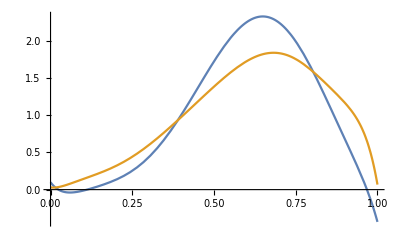

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1}]
```

```mathematica
(*15 moments*)
```

```mathematica
mnum:=15
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.052983438052574514021288617245951826977946162195613065129738449525192752223551373157925172611656319882858869464211675619471086681939366483244859811140699314430610476872666992456887-1.9366501066930206113698086697839595873570874576237136038269103304307676921314158986064774920874374615232882644101641743953397719684764358124111646477163705458263087814957130265973 x+54.48521385143163047532358848428063103255735557433777853349437637339996959436399045007584848363989751100140283680875053124036806894720674161248513148465667771736561527721365500039 x^2-2185.7440356385949433975618924033202790035776067310967765256529639738949866284482459365092626162742125073218611767718327526828538427152167564659180997515281972854000748220700536799 x^3+40342.440573470958078637103224102826877908781824130665851076596579031108685448729351594473192628794318057271641927990105875025061599577971903770868227803447170845687796260639193946 x^4-385099.9873797156283673805641663008545400598207262779332596400191418274568284756089274678558345386073961829671862242002550009900103498508953566641695257711531174302782559366488055 x^5+2.2190462086510721340887956913093894198453237226800154824636006133373261216738329055203809264235682439001839914090902077984786002813040712279416723594692845522258533063449239139788×10^6 x^6-8.3770453815837090713031527656765473052429323663922733702559079879632430630410931504204037353898294380744935380725128436617342380656717456528269165388271173231291433624637379582603×10^6 x^7+2.1649690386682237904458487742691040224239039345845152419699262864407697833344460213362921759205201218525376340688684369800480512939016755181589213204010355023388936343534241682366×10^7 x^8-3.907314179463842625724636112179596289272662871264095906939843931871710929061799711673863901541114206179424373558487063261981000442443239918532647607224273848850422261372825895933×10^7 x^9+4.9281575460142490606186101672029261250172385145746180125673210413801875938666386040608401281152570654532391345986303946963857428841476284122892185682798652356396185005926804796211×10^7 x^10-4.2609471110745843260355903298878073523170430450591028904107244822217891310694334520580797431077166713675492498055556131370911122659513627394199051390738084869728967210311670029892×10^7 x^11+2.4075312684807780864189947580682882292812441627504008309597863601869481985901553945004410726888532048154704981006311815498539799897030256582702997800481602331459232618392222884568×10^7 x^12-8.0081171947402423518702161286605359326198364903008517527088796034127405012518136617353331199036295545535144095900131271558562958716511005688684580394074670888466338117820295811547×10^6 x^13+1.1890410991461952264401287702324261567988641082987193689053774532502627725269143569071908846994448931546869345236593139037300623771182628888902537319977268684830370768995641382226×10^6 x^14

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.01107986351692775245932343414369576437335128789306256498411242307698847484861166879937212926832733272024730422455446377755740285056045422710080634612925107038510162886978188628948894+1.819026281904110916284803620908780345954688158561094349470508327177359038531974669804520619369780489280067039373048841819822305140416581306874248330406312999841470840748200746250338 x-46.2185675794141044457272194689937443769699355026609972926722617778199368784605159624105857103703939075295934305281551782590004124436174345719940922384419624521218505607848978560611 x^2+1175.86873101669151790136655929486881004978330145046404312016864413241217242145672027711599742205678698320929712617708584994287737431213049926421152431567545374111097468897531138658 x^3-14906.570480989565071996099652224458810428972697991078458222321714853480276569521458143800187473467312411633839163153424627643178288995903770783750480207595959401230818215386131416 x^4+112818.577494062824163454151211492225896110787290948673355550145582756919305800441611440966509588208643576409795184470913283444845383782822923409494162879899667925206709277810976522 x^5-549408.299572366239929124945932263265734227996027085390952935178059115578008362472669742089850269207974649120603505169179823050421353551906185240299355112270508958926439778898015475 x^6+1.80547555531654500447744796755393488360718598462628059893674569264889170191016621588634931822534328979956854253366485996112687205142023645880393008315197364942093873280699245680056×10^6 x^7-4.11268241765714309926456160649255695614117262033929168906236429520545867480803049322278116233502178885545634553889721721291284358333306105665139737853162070606695741776791037489964×10^6 x^8+6.56499993364259472167459071260510439552175040577217154402014252564260689087523852521269002311672037213949256374122696203032012052828393434661015777390600832393465560168112884957968×10^6 x^9-7.31601130422538985233565879396771597257372378778697313637633295024111802030539262017944587479085042074037712678398981910271552671916609919050634618762014588366732656026996123777346×10^6 x^10+5.57130025608398221795014682384916328055216008256729176398636150925203110076800119717605490853268612980204842906016168448059724832139987140379018145995027907139292678725777315018281×10^6 x^11-2.76156752921436053106563953178098360742154357304765163413230297519626393545792747090241046497615418539547461341146063108544462808618081865140577806333811504018311946223951235999943×10^6 x^12+802635.697588084100810960463706239357118958389644002609873704058186397286775100370938830270240048892346351018142681798770856968038960686144491752826998710966515113993464552212424493 x^13-103785.343156701336659538646647014791621138963209699277875204675999381430378898721464232281110929337003354109044186098459669412163713214035263256566985243722507643838503942477757236 x^14

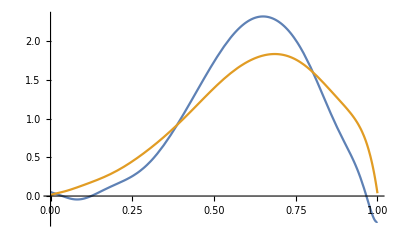

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1}]
```

```mathematica
(*20 moments*)
```

```mathematica
mnum:=20
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.0260139574248726254083521795283554598728442690517732533734148596034859154576145070027476597617404027927865440314215988520013039483024913967710025162301995343434095122677781+5.5325184502711076327783693522846971512086391289654682833125586508590575337856490878192822209243773481534073573542325861089289152064886998298452656201077887954820352039633 x-489.730768716815836575543871024888366754773866338000750488048320271071699716009743368291642835808900012201060496205125255168970119795640009624019953209088523721810951311172 x^2+16324.6235123831812029226021129916231665023310307969673096937881332677478896077736383676028438665310204185500736181738702107123057324766833688961909928384849141121178211974 x^3-328661.80509299147973262856678943210563149712934078039765320088751206021670614303681379038657023013905301055586731832327937080971764965219444832684637099202572188473908686 x^4+4.454081032748487313135453400323832378001688055430566658747584142073786189476412626662492366269440372978585319746847268782790149963351247327068500237819622042745993434558×10^6 x^5-4.232724772529091574213053274077751562036805372598565484125977051862585724230894157582479998289042234262404796641314064517347200931961867928106031078113165436915510049633×10^7 x^6+2.9091641360025779159821892532155849601529697923391389997048145045121543917350834388708143870881784111225383535717483351615867004787051685227643750136625825840899923813771×10^8 x^7-1.4830381404631937692541476410530890767239142218561668806096449793734465803853408980425496533909866412741304977130119239793605288541659819852441145472107402591020175981564×10^9 x^8+5.7154440375097088077337838353067240879762857523780415904465756644843996877343610687558754797894804470033861869563077966548653647536593135651647381959026557240724900354111×10^9 x^9-1.68703733837149884976249561720938454609911055076568504504080799810460528796015149797941656951085044014358455657847331303028641622920630145197535171731609038704776103834979×10^10 x^10+3.84254902273407029274585025488930766516510146365943728791650134172103332768663377560356278603027385836605259434253906348230618083306859645028586153353334899106337557070769×10^10 x^11-6.76790200311142639176646937460971818086194907665413731695715822214452692004657705711263153882579753066250062903652632608652141015041121734656697841377076839405412588055153×10^10 x^12+9.18550583884109980177961465774838916494884497897521452246964805004891558259753765722232694531068539958610021013394908087806886941613636774071123238926219286342917245720979×10^10 x^13-9.50914276929124797894556631565514022830856784190350760543387382644625035288248044551649648433292373906503814919133446079988431956673260383514164527783242640734651820007545×10^10 x^14+7.36613285736578376566706665717764323594473102862326092408505610429496600822044345054838943223419640398442071872535291497165410330220190272560194313308727773731316705917802×10^10 x^15-4.13111951299144257676286822620675566581969226654786251756482839934609400132051699385881078857057402129274401428735914094003701980222397918550143430267187536941743948675252×10^10 x^16+1.58336060446132983930269696493424611414875449661544191841010142686383671005117059857367833499760844806317642983103901263252259763810835902834932381657831522104745298348984×10^10 x^17-3.7090177860438340269055686338684859572648974045297915744490367757944303573080239843326456393594228224920660258530665565274974756049533417748543647662978631939590868641256×10^9 x^18+4.00414466821211920199363952097302757075272524549797676575549469826147131712451019690078482373496721629609586167441136349544635351660114060838001014679327892179514581239402×10^8 x^19

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.0059832935455856618358470097768283164867329409138535852341566237628560664940737635824486964008127673172885436288170929381667325528493215829090888437681682992357191186965494791+3.1054730795879302644311071622427149297891483780667932986849282882249908345607718652520808190098149240703085700450363720845273605259605155713919750825817006784969644357616756 x-125.5907457535015828902158927081037663928079997296421534055787178849658285882809116828718088185287187969787985370443302565476651915096240819536723672193802857146344292673819 x^2+3248.924676221125533713800006729603003579278567034184103605197726330696812997567245888609319596419763561990171278338189938880125498380233453006988664575597375601412645000895 x^3-42522.21621840831933907045819294101282860585782498143742039742168462038510561787606408789673653185205507787396964473987302759974362368894541334001050141163865072097644987518 x^4+300438.4049215171759405278752363369616292035949953877370987165882028962241527901556290848920324793663629877072425073595335734680844506058416755182752367211343165543771903792 x^5-853392.451554810869907963259337872578435813127201090445499419341110602313832503476408182989110374680252440325479848706229735504505467154565669033988107900922455683560733038 x^6-4.11466209668921584498440831790656949062270633226022205896176066251688821853683771174615252098147468851907976661157337456011543772970996023679539866677750282064610453576692×10^6 x^7+5.78238470033900581030183987364861680293498295404908060695783362869214273566168083154363934666890357123786230941607396508932598253048549244161766364713789002869994178688873×10^7 x^8-3.27764006465021179450753406457749657868974751903595813841351625017030457665001337466718673162629822979232722273394590638506160834690551203541722453093560237430705088244148×10^8 x^9+1.202862693806757100251250746269073286055971944004667431648590185698372247253843654204374062530915045113522320265000472932219898801567529355168930235421531700912066990819189×10^9 x^10-3.159940471375871207588066117707468731590568254329487909142829708085007163905948969890127049205891122148226537782174166697628545924346511972572942288390627699580562058059091×10^9 x^11+6.162832118497037610814645025897663974073899889118338381362843294716745196218157700341937563080568470341714871937115506769223602414203353559946018289862406265806310064900681×10^9 x^12-9.035551000007044902285698310045160658020262130682236847577879416698038770510147498445130444834555766513270566892371715349319285002201658039880965813472111597014066630216748×10^9 x^13+9.942063582410583507457654894533622443364965157406062845462387658288392537831451925201767043582158508411459844358945549816763731489107729163065058092625388515814466586181919×10^9 x^14-8.09390569425334306794113131386302978009898466347604726389774913652035308326300719751303185617454755592012533982057002299275612599703918395515789309393799164377313244270411×10^9 x^15+4.73138143115702874512178124495189473707864168403689429221535230322261585344703403892929493758362797402786488865156154813790722426719395698867129664155718781558833016495464×10^9 x^16-1.878326505303864082795291093299323321806305433789393277016567219703898394518005846446587871726093635419012320258999815284724402323580026131069609230600456770015307762279273×10^9 x^17+4.534838970175955268682383932368296171110824290904378666954019463800232184509071008326642686519471445603874332650776313152105260127604474249501049784391364610710159405837171×10^8 x^18-5.025288054268561568200028848385390538949547695166289022877385200452120906234013526845280825186030048351159859074206880007668284443818439790099882651065719463756467216477803×10^7 x^19

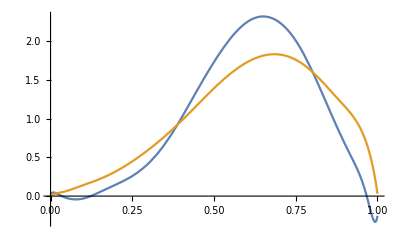

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1}]
```

```mathematica
(*23 moments*)
```

```mathematica
mnum:=23
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.031508584784134868528607697236341415917774036595944175937585983802207209656627036066250068328893167565564062977075324933043541222283617797723227783229812599786347317+3.03846573211663911484829077207722645765130413861502433594105659174231178131548701942631528397471713715764655335238322328032744807087635703627965266997031600257467809 x-201.164637798692472603114862216045207683995629227490398681574197189753350669857648254486503908477904105158806725205609826801515336117185286625681722711921207782137084 x^2+1261.7734281096166947608287520782273989713184723726183944839168556159671247095249361042670135158391760199564796984337636858324817204562716768226079648161083939427604 x^3+117789.78456609774095483435780102453419065737368308163912846955279790274248531498877917109211941314372827632390284271945563869166893434447902467298604817910613891882 x^4-4.03878248181850942928366393608297771700023215748049177132037924555029012167402393645812438273620086136411854067497630949772754018573424228338867483632490863713500649×10^6 x^5+6.93691823730810236758426329937802605852416545439868952557787532423119194221737536488567439617143658869502180228107395491279190634062176232340388782579470370950356679×10^7 x^6-7.75282674800406441009815525118886239656138984087266091093602909703352722746302003831760306913379418446157713222802860896327706706831174327066179217319074767312213057×10^8 x^7+6.15341373480523829719391125739247595789051740755579128998039322908694565167507833869060305522255524040157711767537083575556273649037163304122833615529290635288670496×10^9 x^8-3.62930119947760667428443647416646406949422721187801489957755497650057666487224914690044027717368777886247999165817778634744067746358685202674299734909578071731897347×10^10 x^9+1.63570138331241191376275858688146316927951051629158240630113535615718180297504966538709670217049966771021715640653322006212264636676892431463560213394852081994334797×10^11 x^10-5.73686958369355818868383719670489165990571276008732445511781586414591265305143694727016717681847847671469925323753593478823978644553044248408145863203689266879014712×10^11 x^11+1.58426190478403611671660187669991875516361258800203026991209614113329067788136069566079958847328241884285151699476920899405478518281440845064836880396451308496571698×10^12 x^12-3.46791925531623172487723194705592648191801666452087774841112530179657603542708969518227070494377823463290123326952656076460677176110323874074013865815137626504015285×10^12 x^13+6.03114210765525182543097145265647833456777903372687487609242800302673079095245366734632977714709915675309473826109729380842575142300880837301334346326912125327153052×10^12 x^14-8.316253835723740019370926708603823385421720907804646899528442136273417695760133106504089097022812650932371389375990622097406177262344115771014807173262309956945275×10^12 x^15+9.02931715699146400661866639476438871174774118536701052159781059716693822876148644671528368139967236565114120351242402019600204016503963519722964528534730827774938634×10^12 x^16-7.61977797771723494535535108835565725739302694271100975135298668768884831678829735914108108327172412982186039221336818137843710693329189758790738926135391552653113485×10^12 x^17+4.89156766727893675242259403448956650687889253803660240740352390446367732547617479267936441561647312536525852985025362865262504571334571040870775215723465621459610889×10^12 x^18-2.30668634764545417176759148990449971726551201254069186409455516442231031624451033140375826737627017482776731205967346963187794767559222564722142815068397005299210799×10^12 x^19+7.52993795947544320286159100517863287097046483007731008519254347283871632135352413060782306733748816565178654445657000391740582616670416740679840206329018361218034075×10^11 x^20-1.51955934640361380197095862383145675683008158321758616872913237170750056492245827141383604583990473816922282940000365913647494519181696601194314494203934578800465375×10^11 x^21+1.42769701050893698640461122019637243202089739969283287891966664515577450281384526058077313491223577931659574200071917379547123644285087908107794436061892376354058994×10^10 x^22

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.00327771587940513771714427662456037476723637928513898000380435309991411140790404460335903624884354356189118790226654953642734803190758406911129209042922995238112852977163+4.34097940188884413158048405981276218471313610933832451252500416612366788958903818329492829446449619264032964248293504312014302226712421261193157095195204724427703818059 x-267.827273405897628881722803765870851808578249064065649329494702284432030894607278083130666508593702752235227076957512942088507895402433842485685012338409606268405998562 x^2+10556.738807053458648432107081794800718545313136618793777113533406531388973464468295153199093975721420704993521773533112314282283337840379694575681987698033090947044048 x^3-253634.45975911933324314742792024585459597213978081365639037083659317518187012236128619798784825101388689726304987755930869815863252803900412815233750043571945245921077 x^4+4.1832153638147755891065208599201121133357515555681973370730294923899938389493489698196133979290727342449761174794982735389206228664258158676505364639195417166133828484×10^6 x^5-4.992986027301254365950559771161862838224338680811148022938648950937426044334005568896001124315979092359129841210863997149191232011647636603034871269992548815194087562×10^7 x^6+4.4436826529144253404218478212439704603986745719248533742323574698634325965696757104729006074513080286324461841395785097827737077415915748732506045185251594587750138491×10^8 x^7-3.0115695038112512135301642176419310684749763665161048460146823329257267714029780627440792933385778266074655840714363640953153065692565857958257130361082047083358465978×10^9 x^8+1.5802448727349974113882402453774954799002136658439449990183300474090667888803242825017987747253939650547419262455538732245647361262522258151607514941480520160073658578×10^10 x^9-6.5051266213227821199647894320177296712551385239883175125394492564350740092668822601604731998924715186086572816463689921159492846565201463464740016861948266031157519429×10^10 x^10+2.1216919646873783406760862284770803441274901416268710032510665224433023341233532218104382182200835924019930556828150676614637144931788306016040832391907927594806509631×10^11 x^11-5.5194992511846217054629029885930004004568501393479843107018153781755339053869122648630196446533657366511918778173226153679341284813633164663610101776458116132621482835×10^11 x^12+1.1492210049701716739930266502983998509798837677660000576590022164201324392535408967259565841835941295033181014422539454029464067864085746012834686807740963112688498866×10^12 x^13-1.9152905197788595317525570592539009366657620779602763739505506705261282565961280224274356882687448433952691853494925171434866841210233764228070387192050221453060016206×10^12 x^14+2.5457973272629668288665414842613835998500210732081636617309557117182306769775482409465823800060378599158265190831328746750919518520494696559218730597570435778547874889×10^12 x^15-2.677164585335932917805627985093852388420819227938071054351697718743671123448582736969828099172080516423500072302971035916743901276991132798238960553526367681545639195×10^12 x^16+2.1967188513681623994244300848220158525910502995969799389537001988295656690560084035966818862759601791172770290739552572989719731213663413557607652461406279566866401916×10^12 x^17-1.3755958533429671825888593398689050473669798138620991436688113607392436276429905602579435487870012082748013875844755844425051498587797610962790647107328716429458533644×10^12 x^18+6.3447359418841339289935624937021137749015994628580374224741286197504779786832305370012522286981179242304686962464212431227049068832437872998529146758617866544090192901×10^11 x^19-2.0304362622734252712990909380918162475134024239689933825660160147937803143919520316773707520701172948934612836159096506482931454483296949770722781753808124517814259613×10^11 x^20+4.0246994544606076571212976673513058454329556173335185198085449463777440519463764688452378234913235313461996549107125135963463047919994745132834993306492942321660217656×10^10 x^21-3.7204502889578703583681763092489176187679691961922463149014246198339325309941403762120937279704232039216688775302789574785490341794560109147164871514904237927130383424×10^9 x^22

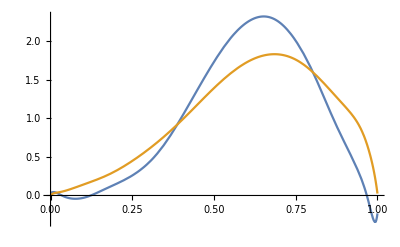

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1}]
```

```mathematica
(*25 moments*)
```

```mathematica
mnum:=25
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.02940619631936922117745809752239150135496552175103937419741744116470178431293484109547308666821560209925914904204415958245407322828957309361428828920239964987578739+3.92676900092152645941817972215111528865251469842355012769579737291119294530976992262362728089185700996647519604535520725224082805727707190828130379459711035687102 x-282.474062697501983491771079047235320796298636014323979725106841390357466860500239343379621518053196927650167678854564189918662179500489312105966315572332332047973 x^2+3481.4674066380854224678946559733363180157741928039054485692262149359510372278818794703500800538735034893100114256318091653256283258674966545014757992463484359538 x^3+143598.12606623624077757202622050662181056602153316010207546964985690950337595121619805947891469591402834206004953341544661020888128587040011965420255279679778911 x^4-6.9569892611806126973961803957877127023096285320423625748789021632219962393315986664683208493827606199522363535317692983948731710744580339357253186227025057684121×10^6 x^5+1.4985048783768458982161584799083587823999149647571948426812426039045456097889760862597753510233688782618839824367936809261924215222972164746604680286910033268515×10^8 x^6-2.0569322843992649701217568242486909827897648667508851511328264975694221476202184983573966464039611998675136502692666317888934270463022397998009995782503955621554×10^9 x^7+1.99572102361527398089130371537559351708020391929871719639767124238294802763006576202218465649585977754203741194122565502360118653280405973871842408666503645516865×10^10 x^8-1.44091195492443399943639925244688411521732785538186517551909675801709553813514605584657619397383973657597781388071650870201849132395905649368773723895199643278278×10^11 x^9+7.98866699982652631653029035177420524295856630617117200691689885019141478751773215652654495661881818333710539354057840639736780125091528858475620812761484011792267×10^11 x^10-3.47292866692257830362668557389002996427290436260155595283952916380614099101407091685241642685647789230953291071248634521984992130254093180978744789539012714238994×10^12 x^11+1.20091342191970663084979043447937335776571103994990254961358151489839634463951668845456475959558829585380977223037804950681839737497453279881370546483873511885511×10^13 x^12-3.33473556309239796183918076951232804285393033268534208724047216310481493869255683282907800270834045977437695547568966497678446841497118065461098267980735326048351×10^13 x^13+7.47864794653867705514142585619580939507616916584639518818810979038081959165734007838695660210137542399656518784458561786388126674071672506491296282944105978960514×10^13 x^14-1.357684402973154121330105222325374220431041932294482720973840126609527535363438423373598537030151556866832924097996873458863780474432520628157269573031143204149×10^14 x^15+1.99315531650640329330884695533074500119612366833217345052312994156313974297596120936503456759690577356935292311465197587275708638100931253338269472407438886354485×10^14 x^16-2.35521267479142590196811704418433874869763877058638599869341173228003881133390593720478326928347982564029957663420558995802661379033974506046032072613139522380106×10^14 x^17+2.22006572028173621380797327176133320780315002825022264877091526962631857739559601067345567037963470991757543400809001664034066090260972146572270628610750575817577×10^14 x^18-1.64504152451878987804926094318580686298075963960484193377011303429229317219823583336008057495510397330146738305230998413402869026597648905870535899907966496107251×10^14 x^19+9.36520362272972493944541047548194272511167002262929564049345647867190493801100024611446501121665757827634464727381764080413560215881417336362703443935275917359631×10^13 x^20-3.95092861894580573085651740998465997908536416353307021461614957515254886374638932436718932656517153337004044055816318666209692143648309972772086193596347075111754×10^13 x^21+1.16285461239453194144122961777393801975322006681508888552671662694539326046841436471477723041937562212395751934740016898895351472890893272820955796761683789907975×10^13 x^22-2.13056879501148175810025709715510342814271377669594912438976497889630224783177888145346852399190180514978586199915430169430162731868811236374479176007439645533249×10^12 x^23+1.82880973270898272391129591766930805757902532209820156095472040988025285793853937585183394412417009088610514588165808771934102996464935466036737420105612429259841×10^11 x^24

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.0028782846794596660480502624728860157028626270044671103353475736727482220374999549337864673271781233138112893287190940926380260751374318234950941398748675360455671925+4.63310977420144680090502305371114591736214576514237796466540163451762801275152956549249662707920434195729565301871976877383309034386946431970846505320061785535865526 x-318.74185209028584211154339275301924441502183626810020827163763787835992643436492582432285542142549913984735321626631082176854444689808777145035176054616558436989218 x^2+14359.611935001943253954833196017373910179384782499598257954348571060293570180789974567511090312965586242853753669573746478648501926801465590533864484865713141159736 x^3-408490.73286055482641270721971946576230517439840232883859252218468773719243297249818958724310972778070539369588825119923058825205191456940549351783833627664133221152 x^4+8.1020557097935786032388595430552853791888866693118949028379708094233274432916189539723711709507274691096628565595602866399229037390250678646073056351135105929674512×10^6 x^5-1.1679830461027597395611288811473721588391274621187163946997350430516346802151394437840299795789903178582114323993879344552991855628781144588686183684268856336120555×10^8 x^6+1.2571989678369465709510030355785984227649030988449202680107201550306665646475581499365937884572614915887874044457915900329970214609552609259002946737763112206313683×10^9 x^7-1.0329819686900114254469043304050157047784965030310616423959506015091360928592810905242579026163899378057087231487310156052686245561805380809566160024924791065761123×10^10 x^8+6.6012250524277760957263074403393601694566064146327279477327315118815881754507674307995261949461177737183520262994350079278360870309899961818731345026881304748236379×10^10 x^9-3.3314838716305470735707339654000674144822395540057996923153553211403673751151414667779335496037520014509358873154124894398383920610071398800600928225733262031497313×10^11 x^10+1.343773528289514232922943654794701220966737120328158539593185514603003957646781330944188578715067593134767057416911993492181893467998681225307608094242918752241978×10^12 x^11-4.3706183434765993533967107015746787493321671721347725191268928089747257077150760828045375717026991891213356506585231913026608597563515166442950811148160975343710934×10^12 x^12+1.1531999706307868369526937356443024141969983293025817202511492696658045152036840978958281859296348244817436697017205122543011416095276209764309688310125985430615501×10^13 x^13-2.4765905748580347020592239564822752495437576843946864989162919432284069168065961621481734727915499103971535196399330857902341444578506120409296364070836351810135087×10^13 x^14+4.3317386681761411395902470650184479639535298510048955509784204534345607049165331057206830858392476934313989852742134466125353874256520242669840575474801027606761535×10^13 x^15-6.156705137918119191263007519281572041896430738178723568808407456059644784593493500062336700981537858110279760698373255465203596193614235162862980831490849488069351×10^13 x^16+7.0712264591073259987315891300715570012230901313609325759906496938822699645159384660012186671465097263901208723028281983049091351553529761395876031276189117281156543×10^13 x^17-6.4997734960416862184300655056287181836218515262417619658135407016840978094800260005533280099284723240253106819237112447904582559825687928461303900908939641882055532×10^13 x^18+4.7092550417401601042542557168712517689436637049239647478574377849796303995170167099446563351405573791106541687975555765627134541269943072576449153437638039161513991×10^13 x^19-2.6273956150092435931987035041135801932116128677914815278119722255301411453022189612282708379823630533942630840035222954531110426039137577101235895881196720395112098×10^13 x^20+1.0883845953557180513880649544676207323947002561531323378792841871907008570071526316345724152079735761599397617168431455802051472256478029753220385596573919195945783×10^13 x^21-3.1506931760746094649266357295953581907265864204999064358924013800437578493379886722686973915766434025851940850512219825551072481185216148523585776270220099877841746×10^12 x^22+5.6858919838081681441081892019424723339089378553311783304912965857726271971959836952863603264407632159269507368757627899481951112845414122616810573192725849576158039×10^11 x^23-4.813247089761650460275937541079211769677253136152645587346379304229652050679775837297130635423780851145286345651312461582469713404751867970893709979854130357836217×10^10 x^24

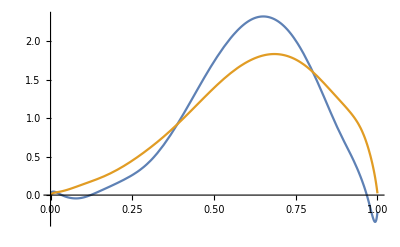

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1},WorkingPrecision->100]
```

```mathematica
(*26 moments*)
```

```mathematica
mnum:=26
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.022796899078305315801548391156179639962000888250844209583878628759554826892293580243748625487650698884984619569642908425020931578595374158069207173669394495820134+8.222812207613064953759488860188825194079526473550407126496025436256715268726589476244527048259044099244919353106168459583782900358506380012584028891050460493046 x-978.4330621815312195750631594093443254754745435848748135307437876523320832540250070299653838315375053907581211227063110676284778922996372250030077811977750541083 x^2+53281.20025860639964887235018410646954172569469007443177866146992523724581027565414504382018337430624240503468007457903019256133044171763619957866511733358321449 x^3-1.842166221406000289000305637963802065484867058295502135336958568091354625699328702891682641455206341435922461112843354991850814740583653914240298721505931689005×10^6 x^4+4.30842722951197478530063367416568662175352850796399258079142889290742598133654552945931805839387762177472295797601253166543446241966539787861454950635774520988×10^7 x^5-7.119712389652660641019830582651540920462264601699199267688695861990920710397738762589705451382006910453024039407921502776728420996616519049661727661723878305835×10^8 x^6+8.636692407359796205093511237050123342394327329995007949081301231541687082325746048786448920662301003272617119693155473703710393875125415707929398339652151443301×10^9 x^7-7.929299393423604672355366954017368528481281650806064837238566056198300226413532583295697010437514829747396458930147361636721734759895983029393851480888264984271×10^10 x^8+5.641386564888494224732212657317476455566053205754633608976884919242116178947816714022233193047753501712037960642312631581520580907128134518619540882092211261039×10^11 x^9-3.167220471112587173881393634290621395342836763619322118626059854246017082814685935473878761070210395107578294378838477919045100324317298108416454935023272296748×10^12 x^10+1.422696449333716958884098584357065298287498351250321456312398206927803771349739967495194686765037991974249990098804267975322623938077118853832594800381457043291×10^13 x^11-5.166131478784841569357330255968288980166654181789174622101070442558273494900026204986171481067295278203796475311895585865440943759716910493077085560014065814483×10^13 x^12+1.527662645435166600799701817179622340648682954624426810700235663561468151534610700953615100846008844900939515272480249995751206720951149973706979108514698792928×10^14 x^13-3.696072666654204711773276345264297671865584932057736792867742019839838622716967358603614124089262829697693147867495689840780637954631334852338602758891930590839×10^14 x^14+7.332682188029298605809736242514210619587663905050608732990974626751739380318288693224696152266453615234650868465824774167599581466142249317998977442114883865681×10^14 x^15-1.192500992689596240250105539070140259414633489929082458121739368686701430167055487581192177072968844737442971341334363165400064172694246745850816963612042011548×10^15 x^16+1.584916954668294860673826041879196502652536932132189516392914166407497236124873447870140875800874375746264103446469523926382259459999164883896786864464243797368×10^15 x^17-1.710804379881451326457163736794190289922374745204745858561846241045431056880325677658497043267136810671023805431913802426186960973403842514354672934212150232804×10^15 x^18+1.484542310673230385973722126464964111752972352918099136316043634372663695807668565826206690354824469019262279535430008954431137443232719281291510131530962725653×10^15 x^19-1.019454326382151577906133444274073311433340913666750791137877518229558734413447198223350304686809459003087640569708003565246598345547356792698110726827749632952×10^15 x^20+5.410223768494835079502446587270135587067092862453950618784343752093450108467042613083322781714559672076731784056714778700144718387897373951420830957897842532104×10^14 x^21-2.138672238168005778348774735979831607064798456987425897327989984839420465337943957242918645350133601378063619315581979598779502204651645110956458303405480768267×10^14 x^22+5.925202264443541654794459516693572056085111358971739854419535359291659188438166094744503375359944933984570552931395864644656395482991784742150050699683896769914×10^13 x^23-1.026068493135721984217900152260963299792507504054800635696241271602180739642301603330379789587222259544187239573941243587703261063298538408075846966006367522202×10^13 x^24+8.354852723702494491656104891501251042946382058206261210446307805607866145773495976711185032227711683624386328262062595719173370903560255637436165664135430121026×10^11 x^25

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.003823574398462356330209865561892008630805368584189971462216136744629676711790066604950538845918311458793073801625003969246766543331652932877789880454390169608680618+4.018671456849698117501281045857250514199363738322518232200835637794682474462956979235850139898082047719135745629878348978151786017625743220956233676510906039334929 x-219.202844679302555400137187480688189102651147923282931612377946409242749231616166850746124498083687473265448219274000814868173146046604953452490277522432270174048 x^2+7237.0429602604725159386558409750183967164155276037842392250995370479088903396565546804650109093959514341041072181240082071108221769842506137979983662785737698127 x^3-124478.294992738680734312147687151836205838499363358254595693379456493353324307303071591280693510441517394803735999640917010687071890607958296175176857614458899748 x^4+944942.27552461173214330372784097444148562201352983618611788491759598269775325603699887291806205052157209077432282101713776826624242123939523427056585122359566938 x^5+6.4630934243562332683105731472870280431990339710415939846501971651963581516467503028072497307392934217703759541383828625627446450425878221967848782390508238144835×10^6 x^6-2.7224858328665306154796562661141668555517776546551332260991679382604311521533373508740275429155691098704205820724765885109153418004234631889270946438078158350779×10^8 x^7+3.8653653969657948346620095919009206763107854915705953389882806664849757876346544026363888862235714208498299687612103726527606614812036614311689096323457265226555×10^9 x^8-3.5281786247012306370116537619565940583549291429565811868151952806506619751411769493906509079674107716744851857297561841607420762663670734664538658206481154092564×10^10 x^9+2.34098218756169669676252430788566695309222035824421342303148368267769270921634738612856562802782398396905295142093457812976537938551281912300302735849497149193506×10^11 x^10-1.1877402501929747224323947481592628769590549066263927680822632970182790551953707191132573352692721028377899449943503341835090458552416310570511397551594620373×10^12 x^11+4.73579927634235397211763160905138654737311248038229399042784666616294513014766531948544147999096721722439023301532323741961626919808238448252319239900635558356462×10^12 x^12-1.50867594900859951973611401669254744176300649220240695177254380768213003740234800431201184456543689429623774244909613614144140377715305781448514188841242621448889×10^13 x^13+3.87931723326050006799364353379142746774849872613763339142599560880645721900780702067462823267627439770537352569977197262408989248585631486799250551480877087272938×10^13 x^14-8.09759215658899352184647158262790401652910490736941890124649742610028471623163311846612913818671984241354279227898755650880939593093041057713035332199838018886549×10^13 x^15+1.37496450111197917899442371898395385518452889920301394210830625853828810852141164683618547515600507735163848049141752260963251584009123206421640053266582833608059×10^14 x^16-1.89654529745823983988335959912010374777885709690506598467739720212224870555092399702075853780462947814122293207820968052599969867710519999652573822280225146278527×10^14 x^17+2.11441083718264162283675384502903327447115170495038793719365514896616935944973239440634269022515423385796537206109004873895655277911451324009889770768240934243041×10^14 x^18-1.88761067735046475234844202344391850341773266588701004378130009821519589423805560959887522879936379562974595042790660675133179181785566317343572040126272258474302×10^14 x^19+1.32927236102810015555249027630209646488950556277695124725155739422836816604786426827767799826332187980062136453231973142982101337023331261094778409774442730509064×10^14 x^20-7.21462543143964789919340770186105344829585247395804367136183966450358314600780922351545408987498294497863086809074304544656099914722472146573993203009251141554385×10^13 x^21+2.91006680850313574505551175635821365607160564154691243438045259777770147243564912609586782893240968034902455513914681809372901799413964552906094073083701765206048×10^13 x^22-8.21060933016220631570141638078412562900559122085542740754889971670854304703277423989431689372587942448455125456903503205036995889163697805660578808791484898478285×10^12 x^23+1.44555061208366173628439176954733382069707387597541353297828426039174682175315452586912832347953938439752307433714643872172490019575965092048523233482737281637538×10^12 x^24-1.19494646638502259270972091596650075071507712586955199108139844274723467380796182739367970386702175432718075023492765067003967786384573568015533554770073129596299×10^11 x^25

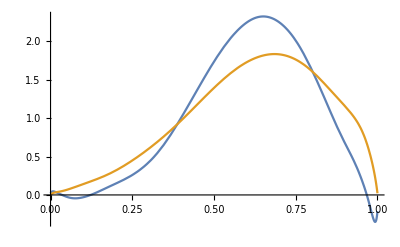

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1},WorkingPrecision->100]
```

```mathematica
mnum:=28
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.02190000426101023931826158888153225927367749193883469386808928616157480803149238451324862646563773795298639131109230115888609915129565832657830118594820665744+9.161515565977612424255147588587657353808545141278911658273775600666931359904805194036166149246844288960990190492998533767636858102245556384414437109928550009 x-1201.122874057150341185956584350854056651465762753251936958346450282857798029514481174843146348461143911746977043534987214314021721749000333798851733997639617 x^2+75396.5690456559204937493831788801591782749451997822824455447728830521650539972289836511508805075330004492895791867292662075067558211834345874621503483157726 x^3-3.025298844191337849199749942080461357261331434683841622931396182259041641573121094591160515073348560021320799319932925201460806642981634499764878063394819693×10^6 x^4+8.2187292797496047234467455702978558940917505004671754634422979425139459841414304169262750278416825144584354053571980788508917603377428385733457835779477082×10^7 x^5-1.581471833866710485446649636152441002087642343174631695897872648593310079923593478247895584724038023624512309294628026570369302334962527431277462481038894343×10^9 x^6+2.241635956420057903705569068170212492464180833857662361757012716778067829728199030199314476487462802160502973094454851833848837086021028747359206575645023801×10^10 x^7-2.414529298368231318024755317940015876933125976639083824488346265276446987112886956647277530775510054075011012649555597612305223428167121489944576447265267697×10^11 x^8+2.024765249024499631829805249175844084121263974106549880823747306474723148407605974793477406095653953472822795104315344536801348214223557733373437524303698892×10^12 x^9-1.347003252035698096094407898782246683100862455589110396400069710144744426727232963237432607170704149564311685079353078967961207457943212064193766255518903696×10^13 x^10+7.214052165781270663680933613236073564562785577347408558117581689222576036308322559249147049862935188424309984646096349976916871056023014651577548204780075337×10^13 x^11-3.145770706037139238613828929504959573529904660612416086763459602099892959432010476278038339030890126723474914043081241094951212340347724927768700388244701634×10^14 x^12+1.12652335394178925207911453404896687819533809948682899857389467437434090638859674530169083534855786271107421375549188552054704314557873829663481445099241455×10^15 x^13-3.33366777493819838863366205057467871390801746324605949128909558619821487927707963791688165366258754421846340679352491013955893269016248586496849034150891475×10^15 x^14+8.185692942451109536357664809460007813707794151483254260327704546822883675382699293097887667874924055874008400625298694907958402670367331653974073764371420496×10^15 x^15-1.671278614659713570108384744798392956915422602725533596382105340688918861542725327173080448422880349659411019774843097222312003717731799980342425407445779766×10^16 x^16+2.837506269851528106308401358930648384792369470035787738236006079961987716788072547681622448429518339045789797785214253261745887866768206122308307762947039625×10^16 x^17-3.997801057561736933244033827413634380466410703563595883718783938607374101509934320472448309507413797344018463864783303534111204336880324777130364273052068571×10^16 x^18+4.653123721214207020182072551749581260771326704190744591306153892303228171157411061846638042246507650157223082242123173715663938169821312169563002983861276297×10^16 x^19-4.440852799070475299133794147708472263377100488264075009072065520438389773818157888371067051774394291289559317649827707214401036140206360083968157938092042186×10^16 x^20+3.436251185156078349565445939612426986560222152008121378464519447388975744501279035781066541866230115416489794956286871150398763446937980628435555073627381833×10^16 x^21-2.120296957650120701957689475218078152216068843999895691783878455866791402790640038336433838815400954642977860256592991191197921707097836602073129065639611076×10^16 x^22+1.018021632698837339632862944385206614904720759082254192702922457952341423185519905014079599669805686606758069879586928241211697784605332240460208155901602299×10^16 x^23-3.663412699731429949035868836021718535265229768978780416007767429249702604270002838283588612344374297564205278140721075049964466657142796644606594540504347861×10^15 x^24+9.29136745849251129381037941321677757233026715793189128964851282671358605366362552489975731806930506651211527657912025755347139865507570231356843567430144438×10^14 x^25-1.480478319893390701164814446430266776896043024767165710469378824206385505275258561996522313892957173866684455882769427667110524926536656330783808048591970802×10^14 x^26+1.11438196539157819296964190830265730558857368986656509023147511739174162540088000777183165394382693465914439784727793886225236622205894836517822258419772187×10^13 x^27

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.00338431879429327456609699825328501147319404235513378162301316899791761707611352367077886064586184662433961594779543971261622039953281505880458281276484306104329+4.28321690507883525795357664373970851181878733944638800143640419757198106740318941431772234849895363800641261531764789862355276086434847085416172653295352257318 x-257.217832784763044225805776338543731358565797313654372128353547469916788719568409800517688201709305032218347655223190444566526723311466355654322350353813418254 x^2+9483.1497223808128619985502524528187839601152440197812056174717676437764369026657178044349492840780761091620213098054401351057172890937086128193009438229530004 x^3-188823.57170127503988665401011042753038008086980070150970059532636517803937115124705982665672158896908694575554893515738287369591439533659522645114482285192787 x^4+1.7325434404742808580596150727740110201958426072276049506335214485206207806062686421345157477935826953313077387873989266142056422320096824497932720505679125209×10^6 x^5+1.15460704556616658427351766866705765671429688906014396240561262387083970562682699383718006879572273709557117488644561375652706224641659924678393564724501881×10^7 x^6-6.3385219864965807262082995012403117471573293453290328899629483388682640543226134814231498399004222674940499114427413616493194895794458967136342568789857928166×10^8 x^7+1.0785634157029022478642822202545539984740650470893773177277369497176552715773114613387636333298725198971567280947667540408543473725865970120619425197562219565×10^10 x^8-1.1736822953201058396434831275954775453708846187472691425921041954126372320184600300388237181605181408363948182241867701870109310365484767749994953950209839342×10^11 x^9+9.29780225694383636637717005716437256938620867893716168294286571357429439062296321690177379681839291915783274481743589183502885866380900269168460329371179141×10^11 x^10-5.6554277610531647292558762219667545414241322218522758312152288652270502818503985741817595599750320293815530676542132225430338782942242919504266301135052779677×10^12 x^11+2.7193708385647328319625261878296318762575096049433658285864546422819329759552204342897585000056119114017984552394369776754666398617642542067113005562452526683×10^13 x^12-1.0526762047270227134960923587528089619607728271600137756342078577985269141878911232343377183886739084050918476593251826540247507502950816375036988170138967539×10^14 x^13+3.3200118895442903020094899056895142117320771298359580993479348383076322248473789069786903613348949869804389932412373845890294972591948845295177965754233453179×10^14 x^14-8.5976337677691304918851613606940944714486923171204569777316895997636964078869724572219427153053020178932884888096597409626999390873570636476924145667002855648×10^14 x^15+1.8365231674845696114778975346469718710311151219718093786653393295980747304442962778596809137848391811555950654039011703630393432114276917134281587249349654337×10^15 x^16-3.2417576234410478307458437902428780620459286188841715093508138345519304711845468453943135999150200720035573127396751575698315885044165694079810536068668811183×10^15 x^17+4.7247630791988828542378522282223331627787548062288699955125973630706255177571345072676217944292672614779509352097467871650899508713662123971858297176738601412×10^15 x^18-5.6655868705243207820665725589392974974919242496576416483305594672567242180156357044754806951942371290102205829664106036706733154158853704577642021660844184442×10^15 x^19+5.5519383046032782730283264559258898969555637438657494946719799947611324534818666654329258519357377141288209905314310680284629477470433033562960086885816596443×10^15 x^20-4.3986397896546471960564633487746458259288174314915822991024823690625206207638051878426245111751586397971579874988977254403075793847960860387387897895302608098×10^15 x^21+2.7723796785535043893173418860298251112974093497719147373166132204165320420589193515405221994764357886549864948018417133625050669193781379274020368077235494228×10^15 x^22-1.3569219869063427967071071741427720246905999646370679528433199166022926622700871262756947651979956039217829968436244215130905540389893089464468447028250689342×10^15 x^23+4.9689902671402073629175103049956313170761486307600145633695040522201549737377977950314793766964828283018436825317318982998433350105517421842834404527472321064×10^14 x^24-1.2805304945217154377835794900404341330027093556454164109389235383181106160369341184857203492040799238421958959951191175854076149195885182850669290061748497808×10^14 x^25+2.0704630563278751874922418563659332173489443216575845617100931194410335713459863621111920211092380311083865130645811471502527455823776895961758599495037432124×10^13 x^26-1.5796163455536158787189905273824208961904941859379886626060943867488224934787965399719281791899380929135968944216688608654916678867661742758049540145102671249×10^12 x^27

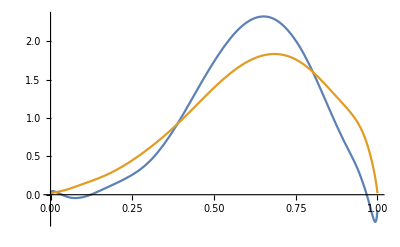

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1},WorkingPrecision->100]
```

#### μ=1000 GeV

```mathematica
(* Specify the final scale mu1: E.g., if Subscript[μ, 1]=91.2 GeV, then write it as 912/10 in order to ensure the working precision you set can be definitely achieved. *)
```

```mathematica
mu1=1000;
```

```mathematica
(* evolving... *)
(* Fewer steps such as 100 and 1000 steps are okay. *)
```

```mathematica
TmulistNLO[mu1]=evoNLO[initialT,μ0,mu1,30000,200]
```

{{0.6177158243355114003620374714952643968946836785535335884302095976289774792819053688711931510260477919925125684326802067860950524833095774929442844883889698750899204606004068760372588479063127548695496419,0.39496092383842149124069484625485397514599446472337357870016797282519509818502942797560819490279469053729613041025957737718756063758216388102380539742032961351836620655413888052648331403465930757277969,0.260009760642330511705945040473996706512747401163100326332205836459696827186506729555560226370818096761152676659928833813816081826755287968160585782411639564643231168720309757837697794601455676912295233,0.17557028618907718864796558779812163294457565076101896479256781981857751436738203390928441088579105857038574320945088288320958232259447941387238464045013551789013800729402135152459864626706342375349528,0.12124961673186823535008637467418850011629776978027386236532058078533622037197878305539251854181380553541870113736883052692736446987603208103593357299992641305716969714193350024884751601875725873159931,0.0854409636647454758551037925676038545662107425305188836567679662183293498178044814560502862988173298060131879426398913058519593888570548275606912136567544666893577246105890055284840897643124111141088,0.0613143812447413414501340996769982100621626651241212708739820515000514899608097122015671703218497259678682348512995265993036935392874541246658086214870416936718692130956979649696413101919158261167144,0.044734200359485767213173517033705871856255108900326023188795692360663873878813683414025070545609890137656725418744003937713481523524171258056430203883097677597055324530769536976386689995284855616416,0.033132513682807910276419279476350883251393277400852748968636606914997900880449963696614016256907961230912672188918331977046235179136564046632666654323995837495815521278299535617312137144700816082985,0.02487871616280048380449066777640779701090547513304031500233849078345604883268565531848818128801012684356751089998618381265137197876537448325999496640564527679037315986981482407459919930819560061271,0.0189161753444690014176309455231041003351068045825841341429599773232597149207980123033170809335670466228037794541386825905246876940011729507441772586139691932284868009471483063947634457193369966121,0.014547391551205326282675247079450797596406531677967409948080229637241031308683240741817193383854943857329078263425502542683504659706274899483846016160607940637986778878005105103096372258472436202,0.01130401330951492184930994806592030263921790530962749259952665970956492445015711935274762848930166938534327851756059003562636557966427222552385659548880840604092662898823289048588289044536248807,0.00886654607950973053600885843948837740219820913012476729570916276786961783238255377792010851030603336038499911988031645778829497090948272025570238268091364884706467962166672769767831231671573931,0.0070138097748058081083242467377365995333821122602845383218417643755112807152237306039636629822139002059531648513819630689413107743394457061431903019718956533821809721079168675982119639174540431,0.005590564548066033906693612390954012165408838451548224749055189042018197489938667760434305588627342093931046606591564160237340471943053134599872704883751493125303935755979452982699652122283144,0.00448643721406397154882300325528468443712012042811501113847040963391663638692913332777008523144450712332873614891995826100244595591891546103672992290365174093322255754572813189700776862634392,0.0036219963407031093415005335963775809393027705415920207386826337465054336749151982175099460050512082183479001907409416789688967744360857866152144255285884273739483405833090546326921301488275,0.002939420970856680720549720539127994811991124846601078684877591154641439408470211723522737522641248396865490993906858306894274776393507208128068169214906295602924048914586583460742594595057,0.00239616465342223566951110876991527004841723926529485164590433259019229013047952515598488898237771621213201844670200458119834614022262450237630707257259565556445912926467835465235976512044,0.0019605995577523932056682504202626120355009282207962856375343367595508462253423127078198238998917105653180493128489612575667405143082634750913527413956535586674767501636382062189702635324,0.001608986542198383743315259646040293463382343941628196461646300020513300830064565379977664868554812494999022812749917321757419696229996116852516207295936524698598205081697187967638465132,0.00132334401836911744957953418851927765911026563792229657621955862079215717440829381565995646286436587710734382196518472469276007804475201826421273674988006464582550915324714945744261421,0.0010899331213307901987616320019934150885876302650276982273738691165085945960447808711387066094661873284233545661024052143224374135811986611641322525842794904199713184095473733230867477,0.0008981701239895825354085432598456036388822735905978048721094193317699102395058939338875455181145238112019404373460157764472480070951509705237186683450985747609827639356916081700519621,0.000739838122235415056076748565648790994042461396240307112586362005731454711384663060834698020370301522054737209283736936342569695433651099816353071898844377993086155639624815845513323,0.00060851043125589387158422660148869143701122735343294474338708893179797692613281699580645369139794002648587030315288910939166657367420789888524139322700754700890616558960651144563301,0.0004991251687731853795883369277564028656369556150216694531727141835858829745468489384222840136126802041377098025307104712191852712566805992513111654882997484765277950577013360861798},{0.6208496531700274935684229505288187025791933823053249157657537407802308885624235769328035446104935825477442889688316771781714230807235966763385030434555070377688922105768779458181474971364236710203480412,0.41252993836271660781485988981078932835997119450491799498176711688172372936259693048251176291734309660761351515732265485260188874592080607039382524299380491519210018376220822805389893020136337741269354,0.287914324179354919383069737083894127615166731121422193798234979421289044076222966328230980588452540254856991496352242306854378786422860843953393796366122736001455839898905860489667501885967861751079995,0.208878198503687533525254467658632901083054201502656263432328956094035897810024749150489525590564325533938091027065768400810557053201747167868494124022581852348483221925043634385253526486801655383126196,0.15644814504390784066825191813131419204285114131603932474383034607064534065503124509443341007268889875418829747634029864547537484481355948210214581561653419475600477547804898795152905781077927626553736,0.12037336704177917332103200479703716599369533703029672115736599436246796301502532092562123073566395406666912042710725228173083427743743404042118170993912847355906148684899777367833377711581801662019425,0.094775733234955734497774830782334895509863021960079732216842174126423127398278311800524840410686626974454361327903535557452020285230845737268711931562026811652458060229177917699758074329579203761937141,0.07612398380549164101982805191873845330070278171671720045926182254912555253834631471280243819393606284438864309125228043331875147432762047447798701072705353144134543329429130276278009757920990573273713,0.06221427393514094022774450424188787605875737255970568352311298112282149877559222298816048862753973881215725498918716168793030471457148110127959353548811720938029974868983892467392828676287989110215764,0.0516260608765957335424898096974950777454390191745717992566754974478440848655504068237797911398275265727823650373113237900487354726741471400685750046853557243076545268090030521595450851962012004369925,0.043417720388741948573770517876834498772622551240504398925586406895049734814656203655464910374915552697730037126757462367989885893801863505064367254846420514681357842521423440777513675984068493011523,0.036949505939002851348136342537549241348749434860898049363191587390781599381915925440851527493142182212551393311266996628203739718475064048175543171896967638095097681143375965474779026174830710614997,0.03177710057804607637073947127521209030501290119545848824319915810576061584118877841666801051381196488882150510230702717684798439111734333131741216843566713789971386468826940594879925692190107751739,0.0275857397251330355578094646797068727496914633574301700037796458629236836927624998155107001672563833130828694672246843642673712320712286991425583240468198512182511977132922661684269679806858718333,0.02414838911274317818393061018616190392323105533724726922979072220867830404331168281762081471875822348657070631402890631580961555503299786682258625660219633272050068364328035119537737458124628951,0.02129858152485097070992552874980223930733420055522416132573261421272441405335458821485060113261265243649436560832743835197824636607917044374880851930677790303597961755074309221836519212336300942,0.0189124069624201080363549709948652980566503149689402056657033092484974626339684805124596413733149765493659339903897302282831501938163287164869905802749114324505785292231255704069886397807497086,0.016896345444601998189949087732787558525821388723106546271125936405375036448435162161908784191452328922016201145150728178249065862260643233668920785459179000656274756711576002678725795202778597,0.01517890431994775160398033866189706371823890054244735116596887306634410311822141246305081090511817209660930214796869648821055458442760317780468399859938894217581206722908225202713890155247044,0.0137047785707292586802617015258037035635673344284596806581299309711513863380126519377062467603957571244117709696125679867353992889351194706942715338229851118683084996254526899880979276461315,0.0124307126082764227984043847811745973890480691096310819046113340655086314641077902600080888847689613183659563072800691487106397700877729117580128722895704452555898625076777164759662359526795,0.011322527514627844338475890076300881144758240763995700406638249594528354934678144921585149555701846165321092846067660291625535259852643144540974774321446088908189550063445270608797392725878,0.01035295817045976512555687675331909545945336231291129253664454692708950422354187697634661658893033525460013810358841179744578150799240583774364677813494799773003007634796616828855493263505,0.00950006081003470419000597117661499018968315724032318403778630002091154834995977275958229216249146587228254512917273603101316414045373522733540140613695445708755683564987425946763980511571,0.0087460274324495872284414003154709819360388221300424643396629831704398238032996675449584522312352543531182635816523854252496828015493776142595277647708811091014813600228409014821687624015,0.008076293846442978649371220757452189826926519222279811746098927428148167002985086278068054456688907019132376450361921456158058623375735053468562692994147610994133706252926764289691933268,0.0074788619969439742409768146014822687323828587088106529850467055240645640533350958758918515831157759428442363056366735608089104873529367725138025508198193840685114550385664220906671574,0.006943780306643166194126212516042777460027375618180806065718972705852810817322820704400261665781742419723806313299583855409616974525741948143135932327931018772584659927905673751227591}}

```mathematica
mnum:=10
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand;
```

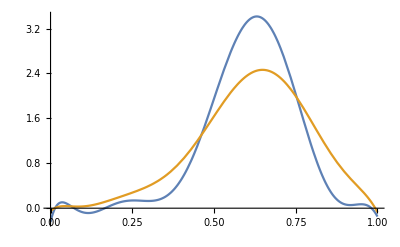

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1}]
```

```mathematica
mnum:=15
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.02486924526473967826089566635129653360854502543457777437184566780578801767921092775017528821963900377923359900455731249023556754480303354649312288277300994031002402931573199430234336-5.733840658985526921922803355946638802657281895831948002066153217153781790436483898818223930883420217625348285512445066671681392674224337458467149556823566544845078442056214064916687 x+330.3593085229931610307414085381136749496445088950429552704557220445857498771745650262145360136278272356939368401292619558239673569433804494670227114841641423796843347442794062491299 x^2-8159.840934359472257349007235761657379138766283833338194415139534716532582615736366397915638591888126804901365946113421086342952217935769238404793238934966716966765393311164469614488 x^3+108729.407662862965411562961453183391982849972641107702574477589610014321076561501421749461967751518770226114719194767854964281793007477982622649036172065742589252337589668426331544 x^4-881138.6778950491470960999915927647248970705229606941845898991457718468850635687388943027377817974098982612034815508759560008562203572362072339380889681124340843654930537093825090695 x^5+4.654219178830386362704401838809821077787344333418489372760201918030324909351274117865958742648727634741309735084121753427213985246041564116505039671717302110127503684940738989275347×10^6 x^6-1.668379521068193171331009996629236323710479420240106854883107338548043774351234839044345615150778434366925618744131732448702516672009285795472107530345459798679885859144014799478211×10^7 x^7+4.149709647463585295343657193210198433684071257541545345653189458826226756598066275335187211547877291005383045917658133703396795315413119914295246781033996394677258892372392980164583×10^7 x^8-7.219157337249201079030418712488053864879677712662673954025648188693016843085420558348438107031472242822387452898930943075534692926583781794833076665294598068959904940299662838064375×10^7 x^9+8.73686524233596734981965128680781668800128636334186859926097985551989552086180083575286348400512798710567075724372833309512197243708121010616032198242123628340816480082209018072054×10^7 x^10-7.196010547001696007260686312269268196264488288530878310720251199729423748949329521459533036197612226364595558198703814077132847266924103210882453700056583554839138685036384850807864×10^7 x^11+3.842478339387842925398938238696039763423166673912399934894076668574444150417953698325288730841862798761696629212424801810954082385329334226849820220082865180259403716110244071248481×10^7 x^12-1.198693573157157502125706695326459343141261325250765524453299380286940168333701642515812514954386586489150107327559546854369841009770839160213040798568308299072808579556577221557141×10^7 x^13+1.65790276514463575687359507628540581275545892669885089240739580073371682013469238697636618138658985706027189497612180956447651377054353229748797509350779291579427244781789586344953×10^6 x^14

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

0.001593327531364213859670423215842140840590283360113340555451632339030920128691593879689551969260915497939567154313198399707280878940211864668290306082414080836378205574205817708550555-0.00408507881385341239232698185232963256584916624289833080781535037909763060867892952503719672661065474030373193692989815288141136907846121027240971393134344762668188445887181376160714 x+17.524624045297950789786057348738949087768051156723886309232137765632886611017874544971032855996870518410790449591069584183000282998800341917816566845894436103994995329517793643201809 x^2-429.45967064019287867979237761890493211509036562313895866831900823196380282188152059493319851458732709013525207012975488550166332299953428726824603419232783731335696538073614254625319 x^3+6569.5131379303109943859250969925794653714816953609397235032306010358609460762517666305788141290967607846859119226906923448485005277429017198274219058073921402026967303750459781465179 x^4-59955.179673696734057133177541911130463722080178048764591552469074691734343710446906687139903716340839881994512652756038938783005445511972912706896638606994083665806996847596847416765 x^5+350597.69336173738421397104049757507405304588413360617816245997538613515489099306841348503295817689301293851801379610731309536571664397560272104030994500267151839472515319807692240961 x^6-1.3667434397115805134590412446588122005960115874131738361833445426390293667037181950405618056466101130872401906950354195193537714364946135962723676830033511773757830663620110637869107×10^6 x^7+3.640285740977400142901062569198282713268046522417441404754039325836961634463561991791290858720993452924024826565573740490683393058220653976908148965781380645970548141704343920019161×10^6 x^8-6.6929487012425043224616216858419512583262236095369179768473890900711128940011264667797258713718725536951918976544479244147441153986370414443354737446109403690969356387803577001874275×10^6 x^9+8.4672788129116942974595626295393284345433036191014329087663351266523785057325314600815104817430670042397243677205152336796106825962145789819769616232803922935508435632266344705523766×10^6 x^10-7.2279994246342376952829093009296995447838354512351248960174426144010955656973835535153575743611502207672272226821099194139951161362124290614597485881063396275879497433518076380117274×10^6 x^11+3.9757750139531998201210557369243219966798683237619160629238825073114286330937882810804806831368088159858646247919351430787238036370357715696224235961727809141141884045613156927329557×10^6 x^12-1.272796391366374590501925487055126589795818008623095435300723256731349588479582119348909510870436948957057275168193564297722711532255006023632781359551604998718686830254100342586489×10^6 x^13+180348.2967300816358643563559739904670353875965984129873111252606536620690037637104133600108073579293422731636461175428095789736158441338063092577948869853272983290124222164126648796 x^14

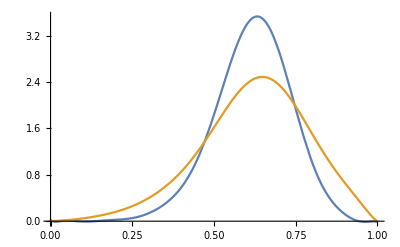

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1}]
```

```mathematica
mnum:=20
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

-0.001382039250569440639254344298069571717268386748074262779415751066225268141280075855240114982341475366965349898304717688676156077428426857193523911782749744083749837828864892+0.5954464944558841372339898343953688047274798278857200345900022241461441231751270785337774740645382407261686387920656383709700324793605660970027651727736364172046426437552224 x-55.76420727600248972455023935981145173643716568706254488140960427190779058513912428244323734237700508163007398762669393017853173774055386759817559482240098958147574784156306 x^2+2527.069961306929402259280343143127457883867646004673697197843128732824185633014453304721490754268612199062332002491405338327972485155028775491028036669997685238449121812403 x^3-63664.04994964829366608853473356314394986277836137483629582350592032649677216387244289149365574409885152387382589558666698472704789419241448533641916956648443958561259817548 x^4+993979.3843967076658460496810187473299818569780537499797849635043156033259254850672619139513482875350023106664062212854590933863690760795623461981523887494408230044264546815 x^5-1.038738652403656567514322383208400072689557536012740244702460295919695006949619751179499661770310745846592877131923122223652064068631780778694166705919177456352817154206855×10^7 x^6+7.652034976096776220520889823020084786162605742210672258020666694604607560795620200504957308218948736250420021684013008695424937863363172891298178248150183300425869358207292×10^7 x^7-4.112655574257171199925192996810582853614438761770988380147346958600213968867017596557132961833089380021379139022723614930287255456486157592674637689291343998820990898981293×10^8 x^8+1.65025064058274618907568268882731876890344774520527445270956175636946393296521959415620142812840280962048681197596968872882320483847725331516738719957593495645577834585423×10^9 x^9-5.018130322778751953789939128698060140712762798896707416678069060129748204474855595095161218388115427349264302162419430523538909994358691155820877785276536640634754751222181×10^9 x^10+1.166234625286453150689405673928412269174013264765562782548991104670398095940600970987139101124676533995708965985372846487016852223968257262351532793452489540905371874260636×10^10 x^11-2.077201089392383252161618155732704539954821245731384223799494177579863310245896769196810610885904862169091216161834171681194544976739925435956962684321140505674762828955782×10^10 x^12+2.826836149509738732587557727699050491768951371085060163259950085085485870460197054045090618849050915088003428351413576241015823362638518037170080668144558308754555302784663×10^10 x^13-2.910844110438023835487116861655987115611540357369836999526839395854186654612392357586966639528781889653431221531295898753694799346327086697466662074893969795482615023003294×10^10 x^14+2.225921502271976700171424229632846543059528670157454301476430565565729803872802860986554501248428276763263376040247246701668948336973361452790534859336112056109124578780372×10^10 x^15-1.223690326630618055274733643269066929814764150496088375843807019685442196556359302325227397643583418336139132186190676682349185011651723320284049823080844702311885690325272×10^10 x^16+4.567770296386132273741669711907432567938506866433162547317200092075620648030133345478221097249081404400556369470451715816471040592543103854027923210726153250037940788322833×10^9 x^17-1.035968887150232811072885263054549413677110114406414601394446549789916205428321845205865354016650350224796860286660740289000879914604941022969744010551127936521448601840393×10^9 x^18+1.077105738431828761531537147787889863654513287736044343839251665929979301061717183202639840660823773896191380604155457455577620569477043370963852505991681238703116350262196×10^8 x^19

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

-0.00028734358647688228396632319932234285754355056156050276316847886563239074167726392457102953042387615766267321835196469490076799250198941595398397225955778747893870937962085082+0.428393483708293422566400833637480476662495761139778043358245662109581015841780913552800021134120332469543754736670993732831416728876374921953084410706991287015087961765553944 x-7.0830718194173130616110955941356397932499488704956310375280985957368871694733854525162167528794859962094733585470541700959060853193984340106259801293121256607883293907085007 x^2+187.50396166129203004695519135104032923331693497600372231950351486845761589654501715648832229235885630869138894138570144002065104256392111010369101979822221683252272158740772 x^3-2183.531982770484392783871313852968924987248833255513195983785589366737569373639696348942612004250055589111556373203361351855019175919021570589784771997752694308895458620489 x^4+22827.896504779332242913436907546845177834814225809429040145303316846074958099824507529833917876525876476348581498458885814327853568716697009359117640347894946640798669893204 x^5-244790.30870823538605786976011789063788852423521958297243912513890774912002142168914353493205149553131879111104486798241780515738326792048270565621422795300319316998042486108 x^6+2.1833858473912669536739155626955684018490834059152158063064202715610295915404030625491305159575978399790114331780230227180338663517891248718546265893607726849735939207096598×10^6 x^7-1.4173845513717499053943826712912052196667030494804926058435991139319889990077908648935810156419622187380829837221679025207905908318522921178351421296066361004615732088884729×10^7 x^8+6.6125592141338450864284531475593630868314941011721379544075173440407328836205313093176237444681686705157984657105381157072540809069513618201352135679267019081258550624733125×10^7 x^9-2.2581688600396735024809826790706044851562047354416659761738801405268674226414444840356621620912401984789785103198500805513300354975262423297079085478716339658348407573314766×10^8 x^10+5.7458696128968150694527545439456086332558507677473245976870033244435698464606606387252070035151514214560756401664664861927378859299414238798740652143088708002940620688629729×10^8 x^11-1.1008728562861431646671964083152988549818055744962424451929918412669693070509478377911269832526841759169919613134608072753788443003564042244600415268042919351277605511849847×10^9 x^12+1.5920479440374629896315556033427768714808470676237002564118007054993516123405845961818510011260461072682373721994993611774716980110252323972715531104482049965774362964931966×10^9 x^13-1.7273594605960709776806358826361673671253058543862687671514929142620606454028300931642088024221709575703058075627440589621277917760133014762842613011951220056665237270794816×10^9 x^14+1.3835260409105830885073339804418169067836253442839007644180306181245719298785573735166028885078581075789178141422798657788031276926333383429220017207622320526945232790529114×10^9 x^15-7.9330734431465145633253518170733773933655557229927382507527427582577815651755762642747967920229384489711902988150233611741692451752931631962999924330672392903471710599595643×10^8 x^16+3.0797474645631852183281085410632234532627058234490140666300640217724451760213386095101008887460983431929835421532149921986236266935563465665057081348001186699756398647092923×10^8 x^17-7.2507405631388085978199676508078387017326969256808390028438342159932476116874973884897989050699835997747556360277686906026532216473595541558128933056746227582087152077333734×10^7 x^18+7.8170927569701376052653012464241134362535379655565576878869850624855798637095707886329974393887897178596236772393340450856261465032522257175348774281891874311067901493088627×10^6 x^19

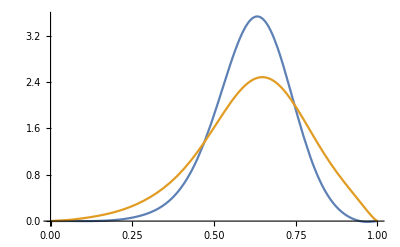

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1}]
```

```mathematica
mnum:=23
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

-0.0001105130775863082985210787843782113426784920291961205908871688419906131374883767152278159470674591816440472127165189346953599692400626167008590731819489222565715581067+0.08046426410822791891746673277742500122652718384262966450194686060625675459689324240506945999529514248046584084267810382496611857735964091748639428318330626143310420162 x-4.587255636695640525189062735778168043944424533580099098735815161396032728812383245858348835013236334548269908956958369051397500943136645918950255114658906998816770372 x^2+332.3884834463879932340596910008139143361818658887168149857791766349493004755159996799805312605507047037139251113338664265789136742007787153135501599528453458082756361 x^3-13018.87691150151374497708159070983049271114540514907162151162179012622559690066122837762456913108212107080161949365574246333063992017163625064497491395776324674302591 x^4+294895.1627815291925885957438695362483983975409717066006747814330857998397257746318273855806689384746447010625232880015073663221597092688278567102077165785414752233507 x^5-4.392332797197520266445211636614777523294586524856132206255657711600169819508534831690465902066998253891576627005046374136608147207287377698818110898732411245171922525×10^6 x^6+4.629672821115893861687482860031598900260451315151737179201809296328537313410012678355315506888921768887374977325738930892338603758313261204290304423041556076158780205×10^7 x^7-3.602085776107080789251058917027935678889499924876042286449704493801186624479388524651900660171469475067704350847869861386076539181377009930050945996216957915039446496×10^8 x^8+2.126423128757875378879101490324540170550753954755002012596036069176676789048150753923001864917084394759107467929363585245442153342224805975100228338558197801726375533×10^9 x^9-9.70632775562338814017603271331268170949326879556217959023577394698763969695710656072663774650672397107045913010599279338222315735472104916725380403675193451983531988×10^9 x^10+3.470576260579545489735420847895869988430026176419080030301032987115040225949138963769667871499419197757993034438775752076214925525901181890678484475046933336923921196×10^10 x^11-9.801570477076804737610011364387497791773395035303799188512242283764405609086133865652418095275739161933431798299225160377776679362778459292721113860031754409266855257×10^10 x^12+2.195874088172135757475503562445303740158198268853012628484569021258501256493813209803288922365658718316389720343300080270675942689441565238320944341880048997877243872×10^11 x^13-3.904612942970511834641360529211279284189607084736347473229127007559159124932745970248893263111481823955993935937830569793988773383701594810917212070843042921478416989×10^11 x^14+5.492359895318989261747466077187414208316557320745839479858943570913101130244393146447412309869455507497054529976182869931603295988516295507904393976936824453472842146×10^11 x^15-6.063911330092073720655131055268863174261219976859999857100409558008454703963540173861139322459240614608074800143226046254061851411614132074659635698040246688121048468×10^11 x^16+5.1838765151140994779578803713305463445685798965310567162596287098277249738054013279599718016222457730138253427000786527361558299638534539971650985632249300993068517643×10^11 x^17-3.3571325667423401897501993783137475396583172537301167486761633120448463873132577166264969109377065589805052419174877934107070770940693448484406115339308505241203782143×10^11 x^18+1.5901890822176991866903110030098798425140404465881798098766751976598772019638389550201321419150225786371937965397276400277875860986221227066978800335320218453531584254×10^11 x^19-5.1919828517899162317370378805918207531228036677105960095255175816688207001547751428394189099987659838688461745145123486623391351924188573074523081894939374244864652323×10^10 x^20+1.0436300685772898643177250091482401596695249281619582589051660338374225453804409553137266361617772446487166105952495634907127720182542551582600697559955460173781838063×10^10 x^21-9.7287749980585373383612478764188989832067437483938080383576344035988026775933077380843751533378168897065550522646499789763723771825323004707443103718811923443491289766×10^8 x^22

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

-0.0000726832595534635844919485667588352958954518712511566140980202623430040958426619586432701643416882904739397198506714604810343028235353419134748687858196457264080184998119+0.3295963820050047510788768378981187330686204264573104386935042039139689927921864372464295479890659748029278045742842578805551719561274121122957348143176707107530037853851 x+4.37929195429852013649019093335267344758665968686874460450208645118289982413366749424699572059667038259220663548114416949041347040865006607981670588714489785252430030229 x^2-405.813508507876777442299688695494601832756348621658057051711534776896569565428251714798407065666705196984819236252708648385867117987651838374624418735304176954290865113 x^3+15076.70040162506010626327346817075536965759320231400953140261913439232094354127608095613449330580248340266320398241033068090262681081776803987243017522280157450182670101 x^4-296652.243809058422433884853680860580997035748612237249120452042292179808285705694938165484341409792324023853535738527821850252331815630846618880256957968072050289238568 x^5+3.816204207857718975640348814713153948856007136472415488921955416030378455861731084072109301206509688191587931364444676105283681456749804745188715363072873625571822975174×10^6 x^6-3.510946735666387436789151055501185659783876599518120739495011580304546670466664607537824384238469206372945270546821010706392068884153676408383127588032307223698920983337×10^7 x^7+2.421015819529643365239532044839009851646786841759107595162816952282178200888972749663968334714191925128619462496111837599899223657932422331795374726857803061740652766929×10^8 x^8-1.285106439733840465360803020171311991330674949677635425231656608285746954201659657841575599714744275327123343265616952615642596946985959560221247642625596872171324381059×10^9 x^9+5.338571132545875001148296000400363970866320627626824714476979895126813869312925629103664150870631256836712175491128137071907901868785820087607553943217042271716829911001×10^9 x^10-1.754414743265915005600833985591940131898637936329091615517017898984048511665307535038303057284847058616131700591044793110534500894616570886112353167647191413759708399876×10^10 x^11+4.592157134868984400408317478647688895987256525881937362135509454809423542189678199471056974122172221422083793432344069405217862875239920444053683785967489694577148899915×10^10 x^12-9.606809889367652485757658769421278535087469796745114419166245953298252006354973554521564596007803643658695199605070302518800672634067035618576238329629764176566474976428×10^10 x^13+1.606515697461279820560652499076342734839369502128988867175294804898636970903244624624892975410004706124607550916533525438807564253697176065452542094585466402020101280487×10^11 x^14-2.14003150703803769490744770031261173212313544143267141364279501862158126133533041272101170908463928174170414676483938471640067553036288466896437623892776332008794092482×10^11 x^15+2.253029384098370278630407782551841975787234619029325910619740717759434844633372567523085856912046126136527793436584057400490635430721246159637524184825248038846253368785×10^11 x^16-1.849269400041615000351767439044106386681079585431687803347662574498469549202684399700964404183098713550010403336494325551842746751277532220338291965703946309481882810481×10^11 x^17+1.157652613220898712439672836897149899829884088935474811860313633096737828695437196675240157277933865252277071498876559590550343495239996208411808229363319744956636302357×10^11 x^18-5.335461400519718176805322573614330190695798679757713455540583117040539279666469999285386335239286566161441068203528408796938868702495869532181143003638965806113463855975×10^10 x^19+1.705678798171183548217859060825654602468876728929601790262271593185488387540290143195796875322095246810044034780600031847151420662151302314713727585908039901784817211755×10^10 x^20-3.376944353037540231498409670813115939944506678154400031661734445820301137038979533103935032602432233845656946107278396098618954129345108602479348397274563269073144412762×10^9 x^21+3.117755491100406010499137316754091551701778619216452261364407751295684334939108707793095523507550172624694340142033285863904859481010111957012240466628075735749384204591×10^8 x^22

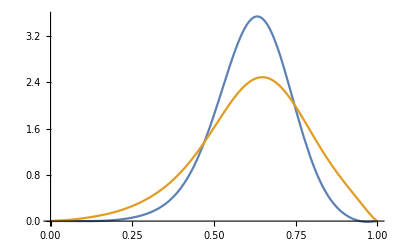

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1}]
```

```mathematica
mnum:=25
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

-0.0000287101889008142264219454403229782066825956811591109842173695987551058352894064374838858991050042858265317934460561562819849068734382696060339681420124869352209057+0.0358425523620904606799426001406764999926355872497979706190690550259055082935247090035968483452190601862953515769957572357128365949764852123368246808028396637917556 x+1.46820730715996954829088450951372240033919186939461746033217660305494596133133110986761904309237195133546903933239822273146590503552467986003230826298839521523693 x^2-29.659223158574831263788958172216880586453760239893153242460269441443854438920840766066330920039296675489283441143132762114933596702952266378971167635448847727007 x^3-997.16212117357134668726976377993315570712044688364549349603550094657749721613081944786436554512203520142525962155180880760832071030967390890100418844354869153233 x^4+43715.8096778568632316044317366286927102053828623061029192596396259924912309876334534043227472398058925645085499739872355751382227508345682141037490531296602300912 x^5-825031.839083539413813204623343539704512662063976572398362173151124147337961064718108447182817759942752124079935418925893233215376387536862167790533050910539452392 x^6+1.0037795938480417826935351466551582951143896192829015086394099037391566098143939414009785271617016080828849115180709387566431116391084266172776439861382586094525×10^7 x^7-8.67881983075581383399025497979250549856416505324659186040492267792114301838399341092379010216201982513426501543170779762027891989262685422670172910829727242777138×10^7 x^8+5.57104487463889014572146101254976944624460361369427721102300593229013636272274131126703471211901811326505608739858604876779690073992324452046680191350674349339662×10^8 x^9-2.72509307478703683006975892601411390988647656488576611639483898892971632953928970715840916690767557179086341706548528090282142710254607965878396294434238742241871×10^9 x^10+1.03379375352225972474275608939790992867950283851093500428530525848424756048530330594791966279682178203049004419724557262518356085857787775229458482585393988384372×10^10 x^11-3.08012068744617807845822997820189168667432371958547470514764110849362530016235821894833173833779085992712611060044323004753213794190130542087702685399212297659859×10^10 x^12+7.27753084558131991622159348057937945338001073269572159185428745605884570960081561385747912001551108573545618276993043078561462797878517429812501648347619711267239×10^10 x^13-1.37519876587950495499183543707438270926081418816148624863983321887582078238619558335125050651436054582870186307650553457686738358523728601400376707013386071099522×10^11 x^14+2.0973045347626499790781907591021053653573443591844692977043819443861990231902614256307235942278613427121756558753227594143702627832985525527045975977097435326911×10^11 x^15-2.6112076623928498996489091854363064627784892349595930839130310271865706817353940853439797432810155755255504687892794966197336114212500176225503901441456857818151×10^11 x^16+2.692008667766662159020726562047130979514624920990540566018769380805830597487016538539003093365101879541680131437886893993823372264740137292127013811990891254868×10^11 x^17-2.3290057257454984689590797204752384954363686043177037446037302052969701227513515864151371840568446648032524126222008207472671980180721708592672741917383893541276×10^11 x^18+1.6956304963633832520138638607799335340507091052912243033704670781759187735153405971586358088146878694951565222221904086679792192253674203507518209633701813317768×10^11 x^19-1.0183089705186275088567922449382392398080023454112128785542535541232883661782453400734944825181601200378895495768483522825920842851850951491656232548134175877931×10^11 x^20+4.8012764055698095736338029337827309234592138480718436246939714823598144633061148630602133782417650701813801538736805706833646453929006170212186939161190495580945×10^10 x^21-1.63789910710002576688243924893231193055775997308470283247924882972928027063913071604848716448815780965480751668317771607273423214278461794485941802915411814399429×10^10 x^22+3.53585892273671627793458064569560457603615655865506919025196633345520655098673854360223899949489161267188158426448448218076697519766920104408083890120267137440338×10^9 x^23-3.58407128590899203888645005138724785992290799583546335702361634950691964430141694638652709884735049967697244021589429639404713514489533376344886839113964358154032×10^8 x^24

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

-0.0000757063983828324335588278044076579867369070537927945254123865318588737817714774060374727073933113145076717354486751831723844833843638592479848081678264287504351228281+0.3276888212096774170332616236392962215204752390810169530510210203418265471808190691465790779646892026943037068257507761967371910244093515314809546219798893762709047943 x+5.17803157802686937734216591008666431935089017200074078354552884408786293230770486719397641727937875381464562969922839243187793871419371836148899201441866590557199862 x^2-489.914502191148054068293953245717329082983197841132698370880237917326036827252353119369631426848737424413016126510799714286074854768141499789934864804984224164955013 x^3+19238.3970113847372594217563268186602225864330306057363406481078400500562753380835947852827458009490884358984338517723438566665014139742819412861516102590308230809697 x^4-416336.883140511219509670638548319917517017700009287639895493819752773440037766699862762688155286063047380289142399073324012889012580689976170741545157479120910809643 x^5+6.05306943860669517237292315052882861519576262932912997957930316494327150118401748318936594596471949039093764073667543810424694746511358817822600492296370751353377496×10^6 x^6-6.42241797063462605850305058764685346245588701582144761736075704584356324703255257762933721447761044891734679265490226455028214056274484457559565652214075983628403731×10^7 x^7+5.18597540704607471888814348580051143589748480555646853135948430160185102708604621131152515977801699086392134328307042851364444106375203082116026895630907196626710966×10^8 x^8-3.26515871745509516069610928287744048104202695389370331036398880264635878796169034492369458692034294132246833611139292851081673077891835782418772849736383852250367848×10^9 x^9+1.62898373503793290495517282036937155065087438404177096702539405574255391584583862445505087693396898445121719421131154184195690132329298767830406675716425532376221325×10^10 x^10-6.51491578674577280802316360653994898683557951173654891051773313382364592700505480859409423011849350378043403586452788190290151236888601318734747877452887857328760541×10^10 x^11+2.10634752106110754727453916237152880384438127084743464748714679307117582007495488538489498399342669864109624958809335073930442680352018299871729047231405186567006393×10^11 x^12-5.53650045230431600963656595312223055888953945975064296009880910871655104268104363768815911353197709768014082840268268600330080300058380480686890219765173029370346184×10^11 x^13+1.18671085414020099837604668581982921855725522363802971163747175334897829160238384559418860187273708098310012811189323095416570373347257605214446363256874483875476947×10^12 x^14-2.07505002559946309920634796085391628833027620882694146381028710460716057795756811860171367266709424117580127519186361185360316624019775663472214747600658259526228618×10^12 x^15+2.95267388523775251765158939055500735138085907956512720568914421933886766240757093630276416626427108565830060651318313539833491711394703151933264683318630021287632733×10^12 x^16-3.39940129851418012478240931102706422578008261658414609655692217003082151598087108610824206816974064270139920413078782454468820801896113128266553240693539035327420772×10^12 x^17+3.13548572865428252153487160549001353441535302290620938121880988185199286456569380539692921335844206920227659168578141607005803207183157686635093621304497551791887853×10^12 x^18-2.28160116789014591817998051916081031977006934449444107738654529923220331874402883442715592869557476932064175115183001057507194195899353790794820684398207470170986647×10^12 x^19+1.27939929241039877842166804769392750201876952399343845628144431906627347250775693843623453381965849594142665570079430689588693614438507269083603487330161767147576271×10^12 x^20-5.32974308437803194313430307485286305554606846636736734084993731327156490261682911297322473631062766058033505916196400367913419368107906127904145897468728791786115968×10^11 x^21+1.55227820208821462179043961689986632581448199448745234457267039799636766448742037011330883758887907223554594300871597253478155351913717673476961081820614614117325241×10^11 x^22-2.8193707179000105205331452468088891009219442688335112927967876491822702891460027062840251929980531178377799949750602175027032100024294355545287300826639966900664575×10^10 x^23+2.40267048044780194725722518265743299802175173866679343106989706813959317817556844772319812211570982736034752539187891338532545331000818721165717777216883067700873748×10^9 x^24

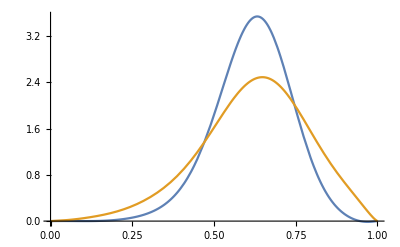

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1}]
```

```mathematica
mnum:=26
```

```mathematica
poly["NLO",g,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦1,ii⟧,{ii,1,mnum-1}] ]//Expand
```

-0.00001834595444432676218464836174876751355763531949389943738412460108102969343486844081578971404401681925324601083209718272154753197371257303727698043199582590346338+0.029105799965373608925699499067439549461411352167410465177459806537756016088075011169334328055577206913659592877922424421428542910154782442644782669292009993149361 x+2.559561195428099532478266883378108386397517952741393341872874858135163698614182159018147330014352181502461948582278138645521481976640528550143114127742801859305 x^2-107.7516569413165767989749858131796111444050933149291163215946779160727680844937380608374661175676598118829982808012067452984659911561307726491221650689863898136 x^3+2116.773675913255756528273088403455725291188959483413534284449036979250434401088460181134650456321444862274119609813891271835033518510819028621266834218760799172 x^4-34755.37240873117976942724813839270709095201417814378458080857072973837264576629239324645245599656980504071580665642840642683430381544185381145748071796053893566 x^5+526416.2968521435489823409745040510698406042183867312196945571383356619843608084492505383901268665275955214506509937879412452003589205570727168750907845317795134 x^6-6.731193176803158527752234727149135228586428290372793072350635982844435289033588866689464286553042979811323999034370816747096980896003919794772064205800045128561×10^6 x^7+6.884898191866755470204160956235973561998042357725086336930034512735395769090150024600200894014566240522395656199163517008214345401951868374429226229056607176155×10^7 x^8-5.534916874837461777518504926986602031539292538826253650778975865486998722660042522971072443177360585438091898036776444880683478692504535310957509425987753310393×10^8 x^9+3.494245504919720246944622000126254117672505280525731166214270817825479318275069240014930840058296499482899454778317715540327585379613477046813651405774530787703×10^9 x^10-1.741778835768359136073579199953989852214588232995022460680743746183360414572344488658364307254107902670197518443790475374238312480567709537806829842793279813236×10^10 x^11+6.904230710140909212533865020994525580708587218192900064660785172185686721225569264427050876150970089204513871677728109283721545319747404414348895356836070100395×10^10 x^12-2.190749631659631985744760728630245563589311354696414311989342013361914327599466472216287006079779015018779915004318579187497306155526490060484306382509852111239×10^11 x^13+5.593470985089441684843463521548422812055421609226685529471354103557494954990684415249526746863509341116238695982952828793109676976974670646500856187219694457029×10^11 x^14-1.153031631157662344993306053776026987632773897793017773504638437503895175212452612718857414571108421398015254850761804006469598898280482936117111010555943101811×10^12 x^15+1.92142788493223927015019229696948413852327770471380838044768681562677723568546953547181767933399519176145064210427741275459584324228999299738911729743713515847×10^12 x^16-2.58548214409819942535571784713077959635589344376008845682766696895946596052363530405042327919038452222124427210068060815585350795452552958962982832772805278612×10^12 x^17+2.797997438971603796908659722851888146881457096159417973131488411636280959865864574442089103980895102347890271466475715329597757797772544956301143629810533958392×10^12 x^18-2.41635547545013071161802317078909499811550786683953688007373811519382423184355712529729339777522513880973747221112806605988334982447313804527435885404300084547×10^12 x^19+1.643664107381503848967422226391460713295590440182723746671854400120377037088862015876531512341452387883706904034824461947250650000713159539319377816025171051808×10^12 x^20-8.623361044696404937562092126204844063517340637562075454793059626651146693182719726240296597242756190807804106342272268336816992121101863070537228852072855734329×10^11 x^21+3.372275942239659713076195775275417619552267928735787662300302128760088688284240374590828497998670473561951312144021858922001059951328318902332055035540652255324×10^11 x^22-9.271999794394596230922597073885740658002401836580110172826309788007114638098568040766005190417959244251719538907708580065770666862981216385984950982047468704528×10^10 x^23+1.60184574077544176390657543623720305843096139618690660775172152624895555830234990297080565063654375844221109910261082920935300383867138932913377072142269750952×10^10 x^24-1.310149162907625347436351949400860429624152380916208993057566151795219803796291257947736737300013810751184658803815817738634780152096274133414607524267275156268×10^9 x^25

```mathematica
poly["NLO",q,mu1,mnum]=Flatten[basis[mnum]].Join[{1},Table[TmulistNLO[mu1]⟦2,ii⟧,{ii,1,mnum-1}] ]//Expand
```

-0.00012916598774060579908071349913792432542128966186103553410628613270216419860842234919436056370588120688969668624266530649786667784939282936804235521701097705061850012+0.36243755429223010462248732521396934166532393432537360870205576088996531812483328219855618456785963274261992484184435635830061742667818210951836020394984577139010003 x-0.45126318134666601211239774501038114411459845758503743192209912471061796062259764722631485243423091401258168890793159374139713845335683528057071226471427010373763 x^2-87.10718829819729953398962059210652036389712256855034606408552548330140404423959542085101168289711230433141688395401848144283599966785743918032935860924969194324383 x^3+3176.455369903325922366371062255929224912875779111515042414668681743324043115449881556852783510878036772644664054820692197042352066850455024478132050704116350740236 x^4-11575.9537751796538158749298813390963756440572716332631800111529634437877857563302894062531055762725454662941435158917021903604490331695378671794522566952762078232 x^5-917813.233796237347909114054291396637794561217819362063854009429761850287600605548351772657669171346030914495355201578716029933351538152703668675565883125367462103 x^6+2.227167059612277966663232311395385218805576043497497612042210418606873584765510285997218440643625527704053408863181870606306315634243437988061416410958983820135338×10^7 x^7-2.841920699151833079469312829873066340148310596373927509680144876341210657426530883991871807631380149937815718750901409428564219844077718933233951859724127614847123×10^8 x^8+2.463389368202177317637976828800742178901762851434406457192684857663628438764568372465643002169325635694079839019021543502265498856545340148700987097287012536612404×10^9 x^9-1.579003192930139682911915402170410738917647906941970502806343194031038931120866257282978172956245418678049783861720562485369147272566683186513613975840221269342793×10^10 x^10+7.801720090136534608904337551902054619503280299265272525094978559380818018135611605773969298317174080432823552229995558896735398720074501415971096397557215313296719×10^10 x^11-3.043664551317389148536881393234691937880291911165720563379092552123207737968701505339172313041070390680061688351464386992787184268758668782198696985422473574087353×10^11 x^12+9.517380990032828178119894132495953147690274456903195348587121284928570126985028889043729908568860548027859297882178393521274675518385146552731676524962728684048987×10^11 x^13-2.407787367805606899516822355031859544034251364624213313089576932480571048909719186298935919730932316053299902041838904360885992157791438864331592919565728019198366×10^12 x^14+4.954190941761227901117484830144941736293114452663667117878163658792847021266100032655952058468970357473158783775434786095831261280496316979719918670389719882512735×10^12 x^15-8.30509485155085416255454906377910120368004002672842560092126520641895700822408508719584110625833237311542448792663070506755615821216457075379722472940152797418523×10^12 x^16+1.132529275860032965071212472266945146215424216604202331831759258061436092519132952594183680038923550752859417198772301177402053410308103362821021655727983128931842×10^13 x^17-1.249814006038087600553339909695320065277417699321540259012944034722807738161713647406364835079059433721475341258819305212017594104539837600198627873661563017668564×10^13 x^18+1.10567831618129810245818681687962810089124105584569619341792748408139507971127903513730044307446003364312841250708407268282301736091694135697467023097449794643239×10^13 x^19-7.724010130139211907942579816677109144841904410498758576525484275464880555695596011978873708802459700441123310749508440851341991864124919556608028805464143890597032×10^12 x^20+4.162681399467889453903751118377159111175449853892073509782565399607458989300156495948652346784100919130144481121376461268963345806398439035161919059710693338093119×10^12 x^21-1.668704562200827748285481054967326876396342419764924860268148490398106436356269964150328757228820301072679830416202158919523563352233375075813163323034202246248989×10^12 x^22+4.683020642141747271328379282477015537786857542242707351636386194410223277397719732533771172613804933861926294628365828701757041823900371300837824804570908986810921×10^11 x^23-8.207056840241874938805631528634858017769822968049184044562704147599029050561043160607767371947002004647281581216635743111097342807298571138495538918235482353655403×10^10 x^24+6.757859110629324106825083237520481054057598513532690710135755083530390694702880004304069747326858389906653067004658907559703910510639511887729005356361892337085022×10^9 x^25

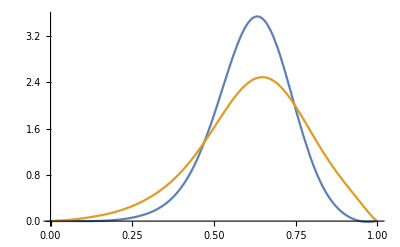

```mathematica
Plot[{poly["NLO",g,mu1,mnum],poly["NLO",q,mu1,mnum]},{x,0,1},WorkingPrecision->100]
```

### Plots

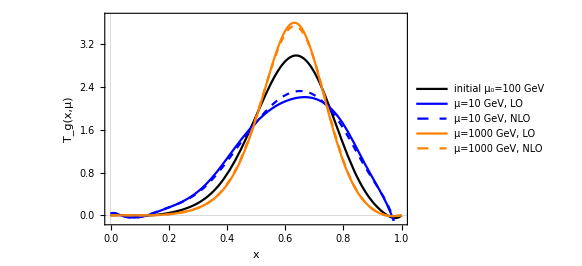

```mathematica
plotT[g]=Plot[{trackfunction["NLO","g",μ0],poly["LO",g,10,23],poly["NLO",g,10,23],poly["LO",g,1000,23],poly["NLO",g,1000,23]},{x,0,1},PlotRange->{{0,1},{-0.1,3.7}},PlotStyle->{{Black},{Blue},{Blue,Dashed},{Orange},{Orange,Dashed}},PlotTheme->"Scientific",FrameLabel->{{Style["T_g(x,μ)",Italic],None},{HoldForm[x],None}},LabelStyle->{FontFamily-> "Times",FontSize-> 14,Black},PlotLegends->Placed[{"initial μ_0=100 GeV","μ=10 GeV, LO","μ=10 GeV, NLO","μ=1000 GeV, LO","μ=1000 GeV, NLO"},{Left,Top}]]
```

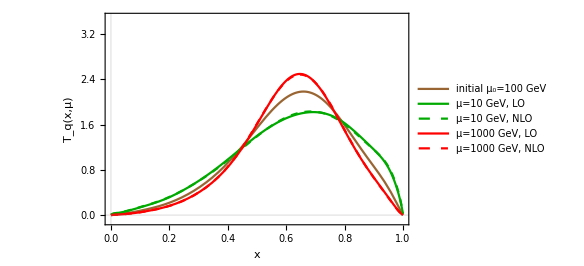

```mathematica
plotT[q]=Plot[{trackfunction["NLO","q",μ0],poly["LO",q,10,23],poly["NLO",q,10,23],poly["LO",q,1000,23],poly["NLO",q,1000,23]},{x,0,1},PlotRange->{{0,1},{-0.1,3.5}},PlotStyle->{{Brown},{Darker[Green]},{Darker[Green],Dashed},{Red},{Red,Dashed}},PlotTheme->"Scientific",FrameLabel->{{Style["T_q(x,μ)",Italic],None},{HoldForm[x],None}},LabelStyle->{FontFamily-> "Times",FontSize-> 14,Black},PlotLegends->Placed[{"initial μ_0=100 GeV","μ=10 GeV, LO","μ=10 GeV, NLO","μ=1000 GeV, LO","μ=1000 GeV, NLO"},{Left,Top}]]
```